# Singular Spectrum Analysis

## make test data

```mathematica
len=200
```

200

## line

```mathematica
a1=Table[N[2*i/len],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph1.csv",a1,"CSV"]
```

~/ssa_20211008/graph1.csv

## line

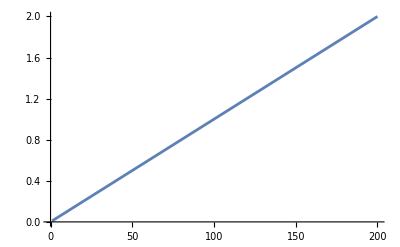

```mathematica
ListPlot[a1,Joined->True]
```

## sine wave

```mathematica
a2=Table[0.5*Sin[2Pi(20*i/len)],{i,len}];
```

```mathematica
Export["~/ssa_20211008/graph2.csv",a2,"CSV"]
```

~/ssa_20211008/graph2.csv

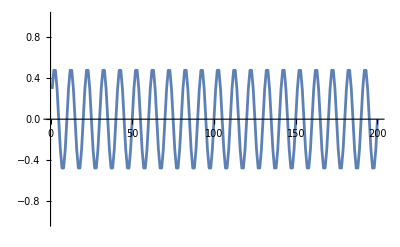

```mathematica
ListPlot[a2,Joined->True,PlotRange->{-1,1}]
```

## superposition of curves

```mathematica
c=a1+a2;
```

```mathematica
Export["~/ssa_20211008/graph3.csv",c,"CSV"]
```

~/ssa_20211008/graph3.csv

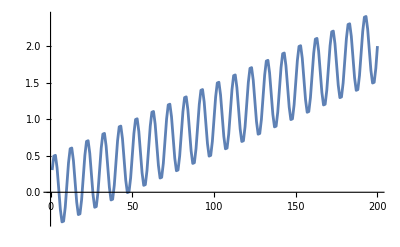

```mathematica
ListPlot[c,Joined->True]
```

## decomposition of curve by singular spectral analysis

```mathematica
c[[1]]
```

0.303893

```mathematica
Length[c]
```

200

200

200

«1 more identical outputs»

0

```mathematica
Dimensions[c]
```

{200}

{200}

{200}

«1 more identical outputs»

```mathematica
m=Length[c]
```

200

```mathematica
n=Floor[m/2]
```

100

```mathematica
m-n+1
```

101

```mathematica
%+n
```

201

```mathematica
x=N[Table[c[[i+j-1]],{i,m-n+1},{j,n}]];
```

```mathematica
Dimensions[x]
```

{101,100}

```mathematica
?SingularValueDecomposition
```

```mathematica
uu=SingularValueDecomposition[x];
```

```mathematica
Dimensions[uu]
```

{3}

```mathematica
u=uu[[1]];
```

```mathematica
w=uu[[2]];
```

```mathematica
v=uu[[3]];
```

```mathematica
Dimensions[u]
```

{101,101}

```mathematica
Dimensions[w]
```

{101,100}

```mathematica
Dimensions[v]
```

{100,100}

```mathematica
Print[n]
```

100

## distribution of singular values

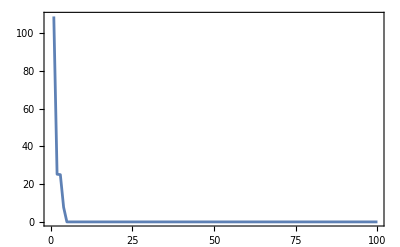

```mathematica
ListPlot[Table[{i,w[[i,i]]},{i,n}],Joined->True,PlotRange->All,Axes->False,Frame->True]
```

```mathematica
sn[xx_]:=Module[{i,j,k,n,n1,x,sum},x={};
{n1,n}=Dimensions[xx];
j=0;sum=0;
Do[Do[If[k≤n,sum=sum+xx[[i-k+1,k]];j=j+1],{k,i}];
x=Append[x,sum/j];sum=0;j=0,{i,n1}];
j=0;sum=0;
     Do[Do[If[k≤n1,sum=sum+xx[[n1-k+1,k+i-1]];j=j+1],{k,n-i+1}];
x=Append[x,sum/j];sum=0;j=0,{i,2,n}];
Return[x]]
```

## 0

## trend

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,1}];
```

List(List(0.2901819684889691,0.29747473075569103,0.304542929302919,0.31058129217544145,0.31517790964296377,0.31847156971677554,
     -   0.321098745846671,0.32395048569606383,0.3278320612201605,0.33315538214925744,0.3397816604720648,0.34707442273878863,0.35414262128601476,
     -   0.3601809841585373,0.36477760162605977,0.36807126169987137,0.3706984378297667,0.37355017767915977,0.3774317532032565,0.3827550741323532,
     -   0.3893813524551607,0.39667411472188463,0.40374231326911075,0.4097806761416332,0.4143772936091556,0.41767095368296725,0.42029812981286263,
     -   0.42314986966225565,0.4270314451863523,0.43235476611544915,0.4389810444382564,0.44627380670498046,0.45334200525220675,0.45938036812472893,
     -   0.4639769855922515,0.46727064566606336,0.4698978217959587,0.47274956164535153,0.4766311371694482,0.481954458098545,0.48858073642135247,
     -   0.4958734986880763,0.5029416972353025,0.5089800601078251,0.5135766775753474,0.5168703376491591,0.5194975137790544,0.5223492536284475,
     -   0.5262308291525439,0.5315541500816408,0.5381804284044482,0.5454731906711723,0.5525413892183983,0.5585797520909208,0.5631763695584433,
     -   0.5664700296322549,0.5690972057621503,0.5719489456115433,0.5758305211356399,0.5811538420647366,0.5877801203875441,0.5950728826542679,
     -   0.602141081201494,0.6081794440740166,0.612776061541539,0.6160697216153509,0.6186968977452462,0.6215486375946389,0.6254302131187357,
     -   0.6307535340478326,0.6373798123706399,0.6446725746373638,0.6517407731845901,0.6577791360571127,0.6623757535246348,0.6656694135984464,
     -   0.668296589728342,0.6711483295777351,0.6750299051018316,0.6803532260309284,0.6869795043537361,0.6942722666204599,0.7013404651676861,
     -   0.7073788280402084,0.7119754455077305,0.7152691055815426,0.7178962817114378,0.7207480215608307,0.7246295970849275,0.7299529180140241,
     -   0.7365791963368318,0.7438719586035557,0.750940157150782,0.7569785200233043,0.7615751374908264,0.7648687975646384,0.7674959736945339,
     -   0.7703477135439268,0.7742292890680235,0.7795526099971203),
     -  List(0.29604400343431553,0.3034840885256714,0.3106950734324387,0.31685541870915984,0.3215448935391341,0.3249050896232684,0.32758533796285766,
     -   0.3304946864870391,0.3344546746412649,0.33988553324223764,0.3466456705890504,0.35408575568040823,0.3612967405871736,0.36745708586389486,
     -   0.37214656069386925,0.3755067567780034,0.3781870051175926,0.38109635364177413,0.38505634179600007,0.39048720039697254,0.3972473377437854,
     -   0.40468742283514336,0.4118984077419088,0.41805875301863,0.4227482278486043,0.4261084239327385,0.4287886722723277,0.4316980207965092,
     -   0.435658008950735,0.4410888675517076,0.44784900489852025,0.4552890899898782,0.4625000748966439,0.4686604201733649,0.47334989500333935,
     -   0.4767100910874737,0.47939033942706283,0.4822996879512443,0.4862596761054701,0.4916905347064427,0.4984506720532556,0.5058907571446133,
     -   0.5131017420513788,0.5192620873281002,0.5239515621580744,0.5273117582422087,0.5299920065817978,0.5329013551059795,0.5368613432602048,
     -   0.5422922018611777,0.5490523392079906,0.5564924242993485,0.5637034092061138,0.569863754482835,0.5745532293128094,0.5779134253969436,
     -   0.5805936737365328,0.5835030222607145,0.5874630104149402,0.5928938690159127,0.5996540063627255,0.6070940914540832,0.6143050763608486,
     -   0.62046542163757,0.6251548964675443,0.6285150925516787,0.6311953408912678,0.6341046894154491,0.6380646775696751,0.6434955361706479,
     -   0.6502556735174604,0.6576957586088183,0.6649067435155841,0.6710670887923053,0.6757565636222794,0.6791167597064135,0.681797008046003,
     -   0.6847063565701845,0.68866634472441,0.6940972033253827,0.7008573406721958,0.7082974257635536,0.715508410670319,0.7216687559470402,
     -   0.7263582307770142,0.7297184268611487,0.732398675200738,0.7353080237249193,0.7392680118791451,0.7446988704801176,0.7514590078269308,
     -   0.7588990929182887,0.766110077825054,0.7722704231017753,0.7769598979317494,0.7803200940158838,0.7830003423554731,0.7859096908796546,
     -   0.7898696790338804,0.795300537634853),List(0.3028057218935271,0.31041574037355735,0.31779142596396476,0.3240924750546106,0.32888905865272067,
     -   0.33232600244876626,0.3350674683251502,0.3380432670911606,0.3420937023569308,0.3476486031152369,0.3545631436756073,0.36217316215563955,
     -   0.369548847746045,0.3758498968366909,0.3806464804348012,0.3840834242308467,0.3868248901072305,0.38980068887324104,0.39385112413901135,
     -   0.39940602489731714,0.4063205654576877,0.41393058393772003,0.42130626952812555,0.4276073186187713,0.4324039022168816,0.435840846012927,
     -   0.4385823118893109,0.4415581106553215,0.44560854592109156,0.4511634466793976,0.45807798723976795,0.46568800571980035,0.47306369131020615,
     -   0.4793647404008517,0.4841613239989619,0.4875982677950076,0.49033973367139144,0.49331553243740184,0.4973659677031721,0.502920868461478,
     -   0.5098354090218485,0.5174454275018807,0.5248211130922862,0.5311221621829323,0.5359187457810424,0.5393556895770879,0.5420971554534718,
     -   0.5450729542194824,0.5491233894852522,0.5546782902435583,0.561592830803929,0.5692028492839614,0.5765785348743667,0.5828795839650125,
     -   0.5876761675631227,0.5911131113591682,0.5938545772355521,0.5968303760015627,0.6008808112673328,0.6064357120256386,0.6133502525860093,
     -   0.6209602710660413,0.6283359566564469,0.6346370057470929,0.6394335893452029,0.6428705331412488,0.6456119990176324,0.6485877977836427,
     -   0.6526382330494132,0.6581931338077193,0.6651076743680895,0.6727176928481219,0.6800933784385276,0.6863944275291735,0.6911910111272833,
     -   0.6946279549233287,0.6973694207997129,0.7003452195657235,0.7043956548314936,0.7099505555897995,0.7168650961501704,0.7244751146302024,
     -   0.7318508002206079,0.7381518493112535,0.7429484329093636,0.7463853767054094,0.7491268425817933,0.7521026413478037,0.7561530766135739,
     -   0.7617079773718797,0.7686225179322503,0.7762325364122827,0.7836082220026883,0.7899092710933341,0.794705854691444,0.7981427984874897,
     -   0.8008842643638737,0.8038600631298843,0.8079104983956544,0.8134653991539603),
     -  List(0.30981028159537727,0.3175963364740668,0.32514263783004504,0.3315894439898232,0.3364969830744009,0.3400134309097387,0.3428183128975542,
     -   0.3458629484080847,0.35000707911481344,0.3556904768967427,0.3627649659279119,0.3705510208066034,0.3780973221625797,0.38454412832235796,
     -   0.3894516674069358,0.39296811524227343,0.39577299723008885,0.3988176327406195,0.4029617634473483,0.40864516122927735,0.41571965026044666,
     -   0.4235057051391383,0.4310520064951146,0.4374988126548928,0.4424063517394705,0.44592279957480824,0.4487276815626237,0.4517723170731543,
     -   0.4559164477798829,0.46159984556181216,0.46867433459298125,0.47646038947167296,0.4840066908276495,0.4904534969874274,0.4953610360720053,
     -   0.4988774839073432,0.5016823658951586,0.5047270014056892,0.5088711321124177,0.5145545298943469,0.5216290189255162,0.5294150738042077,
     -   0.536961375160184,0.5434081813199624,0.5483157204045401,0.5518321682398778,0.5546370502276932,0.557681685738224,0.5618258164449523,
     -   0.5675092142268816,0.574583703258051,0.5823697581367427,0.5899160594927189,0.5963628656524971,0.6012704047370749,0.6047868525724125,
     -   0.607591734560228,0.6106363700707587,0.6147805007774872,0.6204638985594163,0.6275383875905857,0.6353244424692771,0.6428707438252534,
     -   0.6493175499850318,0.6542250890696094,0.6577415369049474,0.6605464188927627,0.663591054403293,0.6677351851100221,0.6734185828919513,
     -   0.6804930719231204,0.688279126801812,0.6958254281577885,0.7022722343175667,0.7071797734021443,0.7106962212374819,0.7135011032252975,
     -   0.7165457387358283,0.7206898694425568,0.7263732672244859,0.7334477562556555,0.741233811134347,0.7487801124903233,0.7552269186501013,
     -   0.7601344577346789,0.7636509055700168,0.7664557875578323,0.7695004230683627,0.7736445537750916,0.7793279515570205,0.7864024405881901,
     -   0.7941884954668817,0.801734796822858,0.8081816029826362,0.8130891420672137,0.8166055899025516,0.8194104718903671,0.8224551074008979,
     -   0.8265992381076264,0.8322826358895555),List(0.31630808316782005,0.32425743875871754,0.3319620123597758,0.3385440305176405,0.343554497804008,
     -   0.34714469780843515,0.3500084079490708,0.3531169000795494,0.35734794765321976,0.36315054609838743,0.3703734118254953,0.37832276741639487,
     -   0.3860273410174512,0.3926093591753159,0.39761982646168353,0.40121002646611065,0.40407373660674617,0.4071822287372249,0.4114132763108954,
     -   0.4172158747560628,0.4244387404831708,0.43238809607407047,0.4400926696751268,0.44667468783299147,0.451685155119359,0.4552753551237861,
     -   0.4581390652644217,0.4612475573949005,0.46547860496857074,0.4712812034137383,0.47850406914084614,0.48645342473174585,0.49415799833280244,
     -   0.5007400164906668,0.5057504837770345,0.5093406837814618,0.5122043939220973,0.515312886052576,0.5195439336262463,0.5253465320714138,
     -   0.5325693977985219,0.5405187533894213,0.5482233269904776,0.5548053451483426,0.55981581243471,0.5634060124391372,0.5662697225797727,
     -   0.5693782147102515,0.5736092622839216,0.5794118607290891,0.5866347264561973,0.594584082047097,0.6022886556481531,0.6088706738060179,
     -   0.6138811410923856,0.6174713410968126,0.6203350512374483,0.623443543367927,0.6276745909415972,0.6334771893867646,0.6407000551138727,
     -   0.6486494107047721,0.6563539843058285,0.6629360024636933,0.6679464697500608,0.6715366697544882,0.6744003798951237,0.6775088720256021,
     -   0.6817399195992727,0.6875425180444403,0.6947653837715481,0.7027147393624478,0.7104193129635042,0.717001331121369,0.7220117984077363,
     -   0.7256019984121633,0.7284657085527991,0.7315742006832779,0.7358052482569482,0.7416078467021157,0.7488307124292239,0.7567800680201234,
     -   0.7644846416211798,0.7710666597790442,0.7760771270654117,0.7796673270698391,0.7825310372104746,0.7856395293409532,0.7898705769146236,
     -   0.795673175359791,0.8028960410868992,0.8108453966777989,0.8185499702788552,0.8251319884367199,0.8301424557230871,0.8337326557275145,
     -   0.8365963658681502,0.8397048579986289,0.8439359055722991,0.8497385040174668),
     -  List(0.3217430916201682,0.3298290381397405,0.3376659966682535,0.34436111128563074,0.3494576716360101,0.3531095607606591,0.3560224770065057,
     -   0.3591843812434155,0.3634881293914591,0.3693904318065007,0.3767374054472726,0.38482335196684697,0.39266031049535793,0.3993554251127353,
     -   0.4044519854631147,0.40810387458776365,0.41101679083361015,0.4141786950705201,0.4184824432185638,0.4243847456336052,0.4317317192743772,
     -   0.43981766579395165,0.44765462432246267,0.45434973893984,0.4594462992902193,0.4630981884148682,0.4660111046607148,0.4691730088976247,
     -   0.47347675704566816,0.4793790594607098,0.48672603310148155,0.49481197962105616,0.5026489381495673,0.5093440527669444,0.5144406131173238,
     -   0.518092502241973,0.5210054184878194,0.5241673227247292,0.5284710708727729,0.5343733732878143,0.5417203469285864,0.5498062934481607,
     -   0.5576432519766716,0.5643383665940492,0.5694349269444285,0.5730868160690775,0.5759997323149241,0.5791616365518341,0.5834653846998772,
     -   0.5893676871149188,0.5967146607556909,0.6048006072752655,0.6126375658037763,0.6193326804211536,0.6244292407715331,0.6280811298961819,
     -   0.6309940461420286,0.6341559503789385,0.6384596985269819,0.6443620009420233,0.6517089745827954,0.6597949211023697,0.6676318796308807,
     -   0.6743269942482581,0.6794235545986375,0.6830754437232867,0.6859883599691331,0.6891502642060426,0.6934540123540864,0.6993563147691282,
     -   0.7067032884098999,0.7147892349294745,0.7226261934579856,0.7293213080753629,0.7344178684257421,0.7380697575503908,0.7409826737962376,
     -   0.7441445780331477,0.7484483261811911,0.7543506285962326,0.7616976022370049,0.7697835487565792,0.7776205072850901,0.7843156219024673,
     -   0.7894121822528465,0.7930640713774957,0.7959769876233421,0.799138891860252,0.8034426400082956,0.809344942423337,0.8166919160641091,
     -   0.8247778625836837,0.8326148211121948,0.839309935729572,0.844406496079951,0.8480583852046003,0.8509713014504469,0.8541332056873568,
     -   0.8584369538354003,0.864339256250442),List(0.3259652228106007,0.3341572786077104,0.34209707902437303,0.3488800514792169,0.35404349235315585,
     -   0.3577433040451537,0.3606944455547496,0.36389784244479645,0.36825806729666016,0.37423782372942893,0.3816812093441387,0.3898732651412505,
     -   0.3978130655579112,0.40459603801275507,0.4097594788866942,0.4134592905786919,0.4164104320882877,0.41961382897833466,0.4239740538301986,
     -   0.429953810262967,0.4373971958776769,0.4455892516747888,0.45352905209144956,0.46031202454629333,0.4654754654202324,0.46917527711223006,
     -   0.472126418621826,0.475329815511873,0.4796900403637366,0.48566979679650524,0.4931131824112149,0.501305238208327,0.5092450386249879,
     -   0.5160280110798314,0.5211914519537706,0.5248912636457685,0.5278424051553644,0.5310458020454111,0.5354060268972749,0.5413857833300435,
     -   0.5488291689447533,0.5570212247418651,0.5649610251585259,0.5717439976133699,0.5769074384873089,0.5806072501793067,0.5835583916889024,
     -   0.5867617885789495,0.5911220134308128,0.5971017698635815,0.6045451554782916,0.6127372112754036,0.6206770116920641,0.627459984146908,
     -   0.632623425020847,0.6363232367128447,0.6392743782224406,0.6424777751124876,0.6468379999643513,0.6528177563971197,0.6602611420118297,
     -   0.6684531978089414,0.6763929982256022,0.6831759706804461,0.688339411554385,0.6920392232463831,0.6949903647559788,0.6981937616460254,
     -   0.7025539864978894,0.7085337429306582,0.7159771285453678,0.7241691843424798,0.7321089847591405,0.7388919572139845,0.7440553980879233,
     -   0.7477552097799209,0.750706351289517,0.753909748179564,0.7582699730314276,0.7642497294641961,0.7716931150789064,0.779885170876018,
     -   0.7878249712926788,0.7946079437475224,0.7997713846214612,0.8034711963134593,0.8064223378230553,0.809625734713102,0.8139859595649658,
     -   0.8199657159977343,0.8274091016124443,0.8356011574095562,0.8435409578262171,0.8503239302810608,0.8554873711549995,0.8591871828469976,
     -   0.8621383243565935,0.8653417212466405,0.869701946098504,0.8756817025312728),
     -  List(0.3292876704871666,0.3375632249977732,0.3455839529784848,0.3524360618610693,0.357652131852884,0.3613896544106418,0.36437087585688627,
     -   0.36760692383302956,0.37201159090729813,0.3780522968723365,0.3855715502714318,0.39384710478204055,0.4018678327627501,0.4087199416453347,
     -   0.41393601163714955,0.41767353419490716,0.42065475564115157,0.423890803617295,0.4282954706915637,0.4343361766566018,0.4418554300556972,
     -   0.45013098456630607,0.4581517125470157,0.4650038214296002,0.47021989142141496,0.47395741397917257,0.47693863542541703,0.4801746834015605,
     -   0.48457935047582895,0.4906200564408673,0.49813930983996246,0.5064148643505714,0.5144355923312813,0.5212877012138655,0.5265037712056804,
     -   0.5302412937634383,0.5332225152096826,0.5364585631858259,0.5408632302600945,0.5469039362251327,0.5544231896242282,0.5626987441348368,
     -   0.5707194721155464,0.5775715809981312,0.5827876509899459,0.5865251735477036,0.5895063949939479,0.5927424429700915,0.5971471100443596,
     -   0.603187816009398,0.6107070694084936,0.6189826239191024,0.6270033518998118,0.6338554607823963,0.6390715307742112,0.6428090533319689,
     -   0.6457902747782134,0.6490263227543568,0.6534309898286254,0.6594716957936634,0.6669909491927588,0.6752665037033675,0.6832872316840771,
     -   0.6901393405666617,0.6953554105584765,0.6990929331162344,0.7020741545624788,0.7053102025386218,0.7097148696128905,0.7157555755779291,
     -   0.7232748289770241,0.7315503834876331,0.7395711114683429,0.7464232203509273,0.751639290342742,0.7553768129004995,0.7583580343467441,
     -   0.7615940823228877,0.765998749397156,0.7720394553621942,0.7795587087612901,0.7878342632718986,0.7958549912526083,0.8027071001351926,
     -   0.8079231701270072,0.8116606926847652,0.8146419141310095,0.8178779621071528,0.8222826291814214,0.8283233351464595,0.8358425885455552,
     -   0.8441181430561641,0.8521388710368738,0.8589909799194582,0.8642070499112725,0.8679445724690306,0.8709257939152751,0.8741618418914187,
     -   0.878566508965687,0.8846072149307251),List(0.3323672769210944,0.34072022713521294,0.3488159675980429,0.35573215965316024,0.360997012044519,
     -   0.3647694891406559,0.36777859194891194,0.37104490450846067,0.37549076547571997,0.3815879661067381,0.3891775420329779,0.3975304922470986,
     -   0.4056262327099265,0.41254242476504394,0.4178072771564028,0.4215797542525395,0.4245888570607955,0.4278551696203443,0.43230103058760383,
     -   0.4383982312186216,0.4459878071448616,0.45434075735898244,0.4624364978218103,0.46935268987692763,0.47461754226828645,0.4783900193644232,
     -   0.4813991221726793,0.4846654347322281,0.48911129569948736,0.49520849633050534,0.5027980722567451,0.511151022470866,0.5192467629336942,
     -   0.5261629549888113,0.53142780738017,0.5352002844763071,0.538209387284563,0.5414756998441117,0.5459215608113711,0.5520187614423889,
     -   0.559608337368629,0.5679612875827497,0.5760570280455776,0.5829732201006951,0.5882380724920538,0.5920105495881907,0.5950196523964467,
     -   0.5982859649559956,0.6027318259232546,0.6088290265542726,0.6164186024805127,0.6247715526946336,0.6328672931574613,0.6397834852125787,
     -   0.6450483376039374,0.6488208147000742,0.6518299175083304,0.6550962300678791,0.6595420910351385,0.6656392916661563,0.6732288675923962,
     -   0.6815818178065169,0.6896775582693448,0.6965937503244624,0.701858602715821,0.7056310798119582,0.708640182620214,0.7119064951797625,
     -   0.7163523561470221,0.7224495567780402,0.7300391327042798,0.7383920829184006,0.7464878233812288,0.7534040154363462,0.7586688678277048,
     -   0.7624413449238414,0.7654504477320977,0.7687167602916466,0.7731626212589057,0.7792598218899237,0.7868493978161639,0.7952023480302846,
     -   0.8032980884931125,0.8102142805482296,0.8154791329395882,0.8192516100357253,0.8222607128439813,0.82552702540353,0.8299728863707894,
     -   0.8360700870018072,0.8436596629280473,0.8520126131421681,0.8601083536049962,0.8670245456601136,0.8722893980514718,0.8760618751476089,
     -   0.8790709779558651,0.8823372905154141,0.8867831514826733,0.8928803521136911),
     -  List(0.3359536414844292,0.34439672308851105,0.3525798195539499,0.3595706398526461,0.36489230192822664,0.36870548543294535,0.3717470575618245,
     -   0.37504861482935065,0.37954244826361755,0.38570543992100015,0.3933769101492445,0.4018199917533286,0.41000308821876535,0.4169939085174616,
     -   0.42231557059304226,0.4261287540977608,0.42917032622663986,0.43247188349416615,0.4369657169284332,0.44312870858581555,0.4508001788140601,
     -   0.45924326041814423,0.46742635688358103,0.4744171771822772,0.4797388392578578,0.4835520227625764,0.4865935948914555,0.4898951521589818,
     -   0.49438898559324856,0.5005519772506312,0.5082234474788754,0.5166665290829596,0.5248496255483968,0.5318404458470927,0.5371621079226734,
     -   0.5409752914273921,0.5440168635562712,0.5473184208237972,0.5518122542580642,0.5579752459154467,0.5656467161436912,0.5740897977477751,
     -   0.5822728942132119,0.5892637145119084,0.5945853765874889,0.5983985600922075,0.6014401322210866,0.604741689488613,0.6092355229228795,
     -   0.6153985145802621,0.6230699848085067,0.631513066412591,0.6396961628780276,0.6466869831767238,0.6520086452523044,0.655821828757023,
     -   0.6588634008859021,0.6621649581534284,0.6666587915876953,0.6728217832450776,0.6804932534733221,0.688936335077406,0.6971194315428428,
     -   0.7041102518415393,0.7094319139171198,0.7132450974218386,0.7162866695507176,0.7195882268182436,0.7240820602525107,0.7302450519098933,
     -   0.7379165221381375,0.7463596037422218,0.7545427002076588,0.7615335205063549,0.7668551825819354,0.7706683660866539,0.7737099382155331,
     -   0.7770114954830595,0.7815053289173262,0.7876683205747087,0.7953397908029536,0.8037828724070375,0.8119659688724743,0.8189567891711703,
     -   0.8242784512467507,0.8280916347514695,0.8311332068803486,0.8344347641478748,0.8389285975821417,0.845091589239524,0.8527630594677686,
     -   0.8612061410718529,0.8693892375372898,0.8763800578359859,0.8817017199115661,0.885514903416285,0.8885564755451643,0.8918580328126907,
     -   0.8963518662469575,0.9025148579043399),List(0.3406027991678588,0.34916272194543707,0.35745906173111036,0.3645466258119592,
     -   0.36994193270953957,0.3738078856717077,0.37689154916881906,0.3802387956578395,0.38479481785168246,0.391043097228794,0.39882073054131767,
     -   0.40738065331889817,0.41567699310456935,0.4227645571854182,0.42815986408299866,0.4320258170451667,0.435109480542278,0.43845672703129857,
     -   0.44301274922514167,0.4492610286022529,0.4570386619147767,0.4655985846923573,0.47389492447802856,0.4809824885588773,0.48637779545645776,
     -   0.4902437484186257,0.4933274119157371,0.49667465840475766,0.5012306805986005,0.507478959975712,0.5152565932882356,0.5238165160658163,
     -   0.5321128558514878,0.5392004199323364,0.5445957268299167,0.548461679792085,0.5515453432891964,0.5548925897782168,0.5594486119720596,
     -   0.565696891349171,0.5734745246616948,0.5820344474392752,0.5903307872249465,0.5974183513057956,0.6028136582033758,0.606679611165544,
     -   0.6097632746626552,0.613110521151676,0.6176665433455185,0.62391482272263,0.6316924560351539,0.6402523788127347,0.6485487185984056,
     -   0.6556362826792544,0.6610315895768349,0.6648975425390029,0.6679812060361143,0.6713284525251348,0.6758844747189778,0.6821327540960891,
     -   0.6899103874086129,0.6984703101861933,0.7067666499718644,0.7138542140527134,0.7192495209502937,0.7231154739124621,0.7261991374095733,
     -   0.7295463838985935,0.7341024060924367,0.7403506854695483,0.7481283187820718,0.7566882415596524,0.7649845813453238,0.7720721454261726,
     -   0.7774674523237529,0.7813334052859208,0.7844170687830323,0.787764315272053,0.7923203374658957,0.7985686168430072,0.8063462501555313,
     -   0.8149061729331116,0.823202512718783,0.8302900767996315,0.8356853836972118,0.8395513366593801,0.8426350001564914,0.8459822466455117,
     -   0.8505382688393548,0.856786548216466,0.86456418152899,0.8731241043065707,0.8814204440922419,0.8885080081730906,0.8939033150706707,
     -   0.8977692680328391,0.9008529315299506,0.9042001780189712,0.908756200212814,0.9150044795899255),
     -  List(0.34646483411320395,0.3551720797154162,0.36361120586062873,0.3708207523456763,0.3763089166057086,0.3802414055781992,0.3833781412850044,
     -   0.38678299644881337,0.39141743127278544,0.3977732483217728,0.4056847406583018,0.4143919862605162,0.4228311124057267,0.43004065889077425,
     -   0.43552882315080677,0.43946131212329714,0.44259804783010226,0.4460029029939114,0.4506373378178836,0.45699315486687064,0.4649046472033998,
     -   0.47361189280561433,0.48205101895082486,0.4892605654358724,0.49474872969590467,0.49868121866839515,0.5018179543752004,0.5052228095390096,
     -   0.5098572443629814,0.5162130614119688,0.5241245537484976,0.5328317993507122,0.5412709254959229,0.5484804719809703,0.5539686362410027,
     -   0.5579011252134934,0.5610378609202986,0.5644427160841076,0.5690771509080795,0.5754329679570668,0.5833444602935959,0.5920517058958102,
     -   0.6004908320410207,0.6077003785260685,0.6131885427861008,0.6171210317585912,0.6202577674653965,0.6236626226292057,0.6282970574531773,
     -   0.6346528745021647,0.6425643668386938,0.6512716124409086,0.6597107385861188,0.6669202850711663,0.6724084493311988,0.6763409383036892,
     -   0.6794776740104944,0.6828825291743036,0.6875169639982756,0.6938727810472626,0.7017842733837918,0.710491518986006,0.7189306451312166,
     -   0.7261401916162643,0.7316283558762965,0.7355608448487874,0.7386975805555924,0.7421024357194012,0.7467368705433735,0.7530926875923609,
     -   0.7610041799288897,0.7697114255311043,0.778150551676315,0.7853600981613625,0.7908482624213946,0.794780751393885,0.7979174871006904,
     -   0.8013223422644996,0.8059567770884715,0.8123125941374587,0.8202240864739881,0.8289313320762025,0.837370458221413,0.8445800047064602,
     -   0.8500681689664925,0.8540006579389833,0.8571373936457883,0.8605422488095973,0.8651766836335695,0.8715325006825564,0.8794439930190858,
     -   0.8881512386213004,0.8965903647665109,0.9037999112515585,0.9092880755115905,0.9132205644840813,0.9163573001908866,0.9197621553546956,
     -   0.9243965901786676,0.9307524072276548),List(0.3532265525724157,0.3621037315633023,0.37070755839215497,0.37805780869112715,0.3836530817192953,
     -   0.3876623184036972,0.39086027164729703,0.3943315770529351,0.39905645898845155,0.4055363181947722,0.41360221374485884,0.42247939273574775,
     -   0.4310832195645983,0.4384334698635705,0.4440287428917387,0.44803797957614055,0.4512359328197404,0.45470723822537845,0.459432120160895,
     -   0.4659119793672154,0.47397787491730226,0.4828550539081913,0.4914588807370418,0.49880913103601393,0.5044044040641821,0.508413640748584,
     -   0.5116115939921838,0.5150828993978219,0.5198077813333383,0.5262876405396588,0.5343535360897453,0.5432307150806345,0.5518345419094853,
     -   0.5591847922084573,0.5647800652366254,0.5687893019210275,0.5719872551646273,0.5754585605702652,0.5801834425057818,0.5866633017121022,
     -   0.5947291972621891,0.6036063762530779,0.6122102030819284,0.6195604533809008,0.6251557264090689,0.6291649630934708,0.6323629163370705,
     -   0.6358342217427088,0.6405591036782249,0.6470389628845455,0.6551048584346324,0.6639820374255214,0.672585864254372,0.679936114553344,
     -   0.6855313875815122,0.6895406242659141,0.692738577509514,0.6962098829151521,0.7009347648506684,0.7074146240569888,0.7154805196070757,
     -   0.7243576985979645,0.732961525426815,0.7403117757257873,0.7459070487539554,0.7499162854383575,0.7531142386819573,0.756585544087595,
     -   0.7613104260231117,0.7677902852294325,0.7758561807795189,0.784733359770408,0.7933371865992588,0.8006874368982309,0.8062827099263988,
     -   0.8102919466108006,0.8134898998544007,0.8169612052600389,0.8216860871955551,0.8281659464018756,0.8362318419519628,0.8451090209428516,
     -   0.8537128477717021,0.861063098070674,0.866658371098842,0.8706676077832441,0.8738655610268441,0.877336866432482,0.8820617483679984,
     -   0.8885416075743188,0.896607503124406,0.9054846821152949,0.9140885089441455,0.9214387592431177,0.9270340322712854,0.9310432689556876,
     -   0.9342412221992875,0.9377125276049256,0.942437409540442,0.9489172687467626),
     -  List(0.36023111227426574,0.3692843276638116,0.3780587702582351,0.3855547776263396,0.39126100614097536,0.39534974686466945,0.39861111621970086,
     -   0.402151258369859,0.40696983574633394,0.4135781919762778,0.42180403599716326,0.43085725138671144,0.43963169398113267,0.44712770134923735,
     -   0.4528339298638732,0.45692267058756714,0.4601840399425985,0.46372418209275673,0.4685427594692318,0.47515111569917534,0.483376959720061,
     -   0.49243017510960935,0.5012046177040306,0.5087006250721351,0.5144068535867709,0.5184955943104649,0.5217569636654963,0.5252971058156545,
     -   0.5301156831921293,0.5367240394220733,0.5449498834429585,0.5540030988325069,0.5627775414269285,0.5702735487950327,0.5759797773096685,
     -   0.5800685180333629,0.5833298873883942,0.5868700295385523,0.5916886069150272,0.5982969631449709,0.6065228071658565,0.6155760225554046,
     -   0.6243504651498258,0.6318464725179308,0.6375527010325664,0.6416414417562605,0.6449028111112918,0.6484429532614502,0.6532615306379247,
     -   0.6598698868678685,0.6680957308887542,0.6771489462783027,0.6859233888727237,0.6934193962408283,0.6991256247554641,0.7032143654791582,
     -   0.7064757348341895,0.7100158769843478,0.7148344543608226,0.7214428105907663,0.7296686546116518,0.7387218700011999,0.7474963125956212,
     -   0.754992319963726,0.7606985484783616,0.764787289202056,0.7680486585570873,0.7715888007072451,0.7764073780837203,0.7830157343136642,
     -   0.7912415783345494,0.8002947937240978,0.8090692363185192,0.8165652436866239,0.8222714722012595,0.8263602129249533,0.829621582279985,
     -   0.8331617244301432,0.837980301806618,0.8445886580365617,0.8528145020574477,0.8618677174469958,0.870642160041417,0.8781381674095213,
     -   0.8838443959241569,0.8879331366478513,0.8911945060028826,0.8947346481530406,0.8995532255295157,0.9061615817594593,0.9143874257803452,
     -   0.9234406411698933,0.9322150837643146,0.9397110911324194,0.9454173196470547,0.9495060603707489,0.9527674297257805,0.9563075718759388,
     -   0.9611261492524136,0.9677345054823573),List(0.36672891384670875,0.37594542994846253,0.38487814478796617,0.39250936415415716,
     -   0.3983185208705827,0.4024810137633662,0.4058012112712178,0.40940521004132396,0.41431070428474065,0.42103826117792287,0.429412481894747,
     -   0.4386289979965032,0.44756171283600454,0.45519293220219564,0.46100208891862127,0.46516458181140474,0.46848477931925614,0.4720887780893625,
     -   0.4769942723327793,0.4837218292259612,0.4920960499427855,0.5013125660445418,0.5102452808840432,0.5178765002502342,0.5236856569666598,
     -   0.5278481498594432,0.5311683473672948,0.534772346137401,0.5396778403808176,0.5464053972739998,0.5547796179908238,0.5639961340925802,
     -   0.5729288489320818,0.5805600682982726,0.5863692250146982,0.5905317179074818,0.5938519154153334,0.5974559141854395,0.6023614084288562,
     -   0.6090889653220383,0.6174631860388625,0.6266797021406186,0.63561241698012,0.6432436363463113,0.6490527930627368,0.6532152859555203,
     -   0.6565354834633718,0.6601394822334782,0.6650449764768944,0.6717725333700767,0.680146754086901,0.6893632701886575,0.6982959850281586,
     -   0.7059272043943496,0.7117363611107753,0.7158988540035587,0.7192190515114103,0.7228230502815166,0.7277285445249331,0.7344561014181151,
     -   0.7428303221349394,0.7520468382366955,0.7609795530761969,0.7686107724423881,0.7744199291588135,0.7785824220515973,0.7819026195594487,
     -   0.7855066183295546,0.7904121125729715,0.7971396694661539,0.8055138901829778,0.8147304062847341,0.8236631211242357,0.8312943404904268,
     -   0.8371034972068522,0.8412659900996354,0.8445861876074872,0.8481901863775936,0.85309568062101,0.8598232375141921,0.8681974582310167,
     -   0.8774139743327728,0.8863466891722742,0.8939779085384649,0.8997870652548903,0.9039495581476741,0.9072697556555256,0.9108737544256318,
     -   0.9157792486690485,0.9225068055622304,0.9308810262790549,0.9400975423808113,0.9490302572203126,0.9566614765865038,0.9624706333029289,
     -   0.9666331261957125,0.9699533237035642,0.9735573224736705,0.9784628167170871,0.9851903736102692),
     -  List(0.37216392229905665,0.38151702932948534,0.3905821290964436,0.3983264449221472,0.4042216947025845,0.40844587671558985,0.41181528032865244,
     -   0.41547269120518976,0.42045088602297964,0.42727814688603594,0.435776475516524,0.4451295825469551,0.45419468231391097,0.4619389981396147,
     -   0.4678342479200522,0.4720584299330574,0.4754278335461199,0.4790852444226573,0.48406343924044737,0.4908907001035032,0.4993890287339916,
     -   0.5087421357644227,0.5178072355313788,0.5255515513570823,0.5314468011375196,0.5356709831505249,0.5390403867635875,0.542697797640125,
     -   0.5476759924579147,0.554503253320971,0.5630015819514589,0.5723546889818901,0.5814197887488464,0.5891641045745497,0.5950593543549872,
     -   0.5992835363679928,0.6026529399810552,0.6063103508575924,0.6112885456753824,0.6181158065384385,0.6266141351689266,0.6359672421993576,
     -   0.6450323419663136,0.6527766577920177,0.6586719075724549,0.6628960895854601,0.6662654931985226,0.6699229040750603,0.6749010988928497,
     -   0.6817283597559058,0.6902266883863942,0.6995797954168256,0.7086448951837813,0.7163892110094849,0.7222844607899224,0.7265086428029276,
     -   0.7298780464159901,0.7335354572925277,0.7385136521103174,0.7453409129733733,0.7538392416038616,0.7631923486342926,0.7722574484012485,
     -   0.7800017642269524,0.7858970140073898,0.7901211960203953,0.7934905996334577,0.7971480105099947,0.8021262053277849,0.8089534661908412,
     -   0.817451794821329,0.8268049018517604,0.8358700016187165,0.8436143174444202,0.8495095672248573,0.8537337492378624,0.8571031528509252,
     -   0.8607605637274628,0.8657387585452524,0.8725660194083086,0.8810643480387971,0.8904174550692281,0.899482554836184,0.9072268706618875,
     -   0.9131221204423247,0.9173463024553303,0.9207157060683927,0.92437311694493,0.9293513117627199,0.9361785726257759,0.9446769012562644,
     -   0.9540300082866956,0.9630951080536515,0.9708394238793552,0.9767346736597922,0.9809588556727977,0.9843282592858603,0.9879856701623979,
     -   0.9929638649801875,0.9997911258432437),List(0.3763860534894893,0.38584526979745526,0.3950132114525633,0.4028453851157334,0.4088075154197304,
     -   0.4130796200000846,0.4164872488768965,0.4201861524065708,0.42522082392818084,0.43212553880896415,0.44072027941339015,0.45017949572135874,
     -   0.45934743737646433,0.4671796110396346,0.47314174134363174,0.4774138459239858,0.48082147480079757,0.484520378330472,0.48955504985208215,
     -   0.4964597647328652,0.5050545053372913,0.51451372164526,0.5236816633003657,0.5315138369635358,0.5374759672675329,0.5417480718478869,
     -   0.5451557007246988,0.5488546042543734,0.5538892757759832,0.5607939906567664,0.5693887312611924,0.5788479475691611,0.5880158892242671,
     -   0.595848062887437,0.6018101931914341,0.6060822977717885,0.6094899266486001,0.6131888301782744,0.6182235016998845,0.6251282165806676,
     -   0.6337229571850939,0.6431821734930622,0.6523501151481679,0.6601822888113384,0.6661444191153353,0.6704165236956895,0.6738241525725013,
     -   0.6775230561021758,0.6825577276237854,0.6894624425045687,0.698057183108995,0.7075163994169636,0.7166843410720691,0.7245165147352394,
     -   0.7304786450392364,0.7347507496195905,0.7381583784964024,0.7418572820260769,0.7468919535476869,0.7537966684284698,0.762391409032896,
     -   0.7718506253408643,0.7810185669959702,0.7888507406591405,0.7948128709631375,0.7990849755434919,0.8024926044203036,0.8061915079499777,
     -   0.8112261794715879,0.8181308943523713,0.8267256349567972,0.8361848512647658,0.8453527929198718,0.8531849665830418,0.8591470968870386,
     -   0.8634192014673926,0.8668268303442047,0.8705257338738793,0.8755604053954892,0.8824651202762723,0.8910598608806989,0.9005190771886672,
     -   0.9096870188437729,0.9175191925069429,0.9234813228109396,0.9277534273912941,0.9311610562681059,0.9348599597977802,0.9398946313193903,
     -   0.9467993462001733,0.9553940868045996,0.9648533031125683,0.9740212447676739,0.9818534184308443,0.9878155487348409,0.9920876533151952,
     -   0.9954952821920072,0.9991941857216817,1.0042288572432916,1.0111335721240748),
     -  List(0.37970850116605515,0.38925121618751807,0.39850008540667503,0.40640139549758586,0.4124161549194586,0.4167259703655727,0.4201636791790331,
     -   0.423895233794804,0.4289743475388188,0.4359400119518718,0.4446106203406833,0.4541533353621487,0.46340220458130327,0.47130351467221426,
     -   0.4773182740940871,0.48162808954020103,0.4850657983536613,0.48879735296943233,0.49387646671344737,0.5008421311265,0.5095127395153118,
     -   0.5190554545367771,0.5283043237559318,0.5362056338468426,0.5422203932687155,0.5465302087148294,0.5499679175282898,0.5536994721440608,
     -   0.5587785858880756,0.5657442503011285,0.5744148586899399,0.5839575737114054,0.5932064429305605,0.6011077530214709,0.6071225124433439,
     -   0.6114323278894581,0.6148700367029184,0.6186015913186892,0.6236807050627041,0.6306463694757569,0.6393169778645685,0.6488596928860338,
     -   0.6581085621051885,0.6660098721960996,0.6720246316179724,0.6763344470640864,0.6797721558775467,0.6835037104933178,0.6885828242373322,
     -   0.6955484886503851,0.7042190970391969,0.7137618120606626,0.723010681279817,0.7309119913707278,0.7369267507926007,0.7412365662387147,
     -   0.7446742750521751,0.7484058296679461,0.7534849434119608,0.7604506078250135,0.7691212162138252,0.7786639312352904,0.7879128004544451,
     -   0.7958141105453562,0.8018288699672289,0.8061386854133433,0.8095763942268035,0.8133079488425741,0.8183870625865891,0.8253527269996421,
     -   0.8340233353884535,0.843566050409919,0.8528149196290741,0.8607162297199848,0.8667309891418574,0.8710408045879712,0.8744785134014318,
     -   0.8782100680172029,0.8832891817612174,0.8902548461742704,0.8989254545630825,0.9084681695845478,0.9177170388037024,0.9256183488946129,
     -   0.9316331083164855,0.9359429237625999,0.9393806325760603,0.943112187191831,0.9481913009358459,0.9551569653488985,0.9638275737377106,
     -   0.9733702887591761,0.9826191579783308,0.9905204680692415,0.996535227491114,1.0008450429372282,1.0042827517506887,1.00801430636646,
     -   1.0130934201104744,1.0200590845235273),List(0.38278810759998294,0.39240821832495776,0.40173210002623305,0.40969749328967675,
     -   0.41576103511109347,0.4201058050955867,0.42357139527105875,0.42733321447023503,0.4324535221072406,0.4394756811862733,0.44821661210222935,
     -   0.4578367228272067,0.4671606045284796,0.4751259977919233,0.4811895396133402,0.4855343095978333,0.48899989977330527,0.4927617189724817,
     -   0.49788202660948744,0.5049041856885198,0.5136451166044761,0.5232652273294535,0.5325891090307264,0.5405545022941701,0.5466180441155869,
     -   0.55096281410008,0.5544284042755521,0.5581902234747284,0.5633105311117339,0.5703326901907666,0.5790736211067224,0.5886937318317,
     -   0.5980176135329733,0.6059830067964166,0.6120465486178335,0.6163913186023269,0.6198569087777989,0.623618727976975,0.6287390356139807,
     -   0.6357611946930132,0.6445021256089694,0.6541222363339466,0.6634461180352196,0.6714115112986635,0.6774750531200803,0.6818198231045735,
     -   0.6852854132800453,0.689047232479222,0.694167540116227,0.7011896991952598,0.709930630111216,0.7195507408361936,0.7288746225374664,
     -   0.7368400158009101,0.742903557622327,0.74724832760682,0.750713917782292,0.7544757369814684,0.759596044618474,0.7666182036975063,
     -   0.7753591346134625,0.7849792453384398,0.7943031270397127,0.8022685203031567,0.8083320621245733,0.8126768321090667,0.8161424222845386,
     -   0.8199042414837147,0.8250245491207204,0.8320467081997532,0.8407876391157091,0.8504077498406868,0.8597316315419599,0.8676970248054034,
     -   0.8737605666268201,0.8781053366113131,0.8815709267867852,0.8853327459859618,0.8904530536229671,0.8974752127019997,0.9062161436179562,
     -   0.9158362543429335,0.9251601360442064,0.93312552930765,0.9391890711290664,0.94353384111356,0.9469994312890319,0.950761250488208,
     -   0.9558815581252138,0.9629037172042461,0.9716446481202025,0.9812647588451802,0.990588640546453,0.9985540338098968,1.0046175756313132,
     -   1.0089623456158066,1.0124279357912787,1.016189754990455,1.0213100626274607,1.0283322217064932),
     -  List(0.3863744721633178,0.396084714278256,0.40549595198214017,0.41353597348916266,0.41965632499480127,0.4240418013878763,0.42753986088397133,
     -   0.43133692479112506,0.4365052048951382,0.4435931550005354,0.4524159802184961,0.4621262223334368,0.47153746003731856,0.47957748154434116,
     -   0.48569783304997993,0.49008330944305484,0.4935813689391497,0.4973784328463037,0.5025467129503169,0.5096346630557138,0.5184574882736745,
     -   0.5281677303886154,0.5375789680924973,0.5456189895995197,0.5517393411051584,0.5561248174982333,0.5596228769943283,0.5634199409014822,
     -   0.5685882210054952,0.5756761711108924,0.5844989963288528,0.5942092384437938,0.603620476147676,0.6116604976546981,0.6177808491603368,
     -   0.622166325553412,0.625664385049507,0.6294614489566607,0.6346297290606739,0.6417176791660709,0.6505405043840318,0.6602507464989723,
     -   0.6696619842028542,0.6777020057098769,0.6838223572155154,0.6882078336085904,0.6917058931046854,0.6955029570118394,0.7006712371158521,
     -   0.7077591872212493,0.7165820124392102,0.7262922545541511,0.7357034922580328,0.7437435137650552,0.7498638652706939,0.7542493416637688,
     -   0.7577474011598639,0.7615444650670179,0.7667127451710308,0.7738006952764277,0.7826235204943885,0.7923337626093292,0.801745000313211,
     -   0.8097850218202337,0.8159053733258722,0.8202908497189476,0.8237889092150424,0.8275859731221958,0.8327542532262093,0.8398422033316066,
     -   0.8486650285495669,0.8583752706645079,0.8677865083683899,0.8758265298754124,0.8819468813810508,0.8863323577741256,0.8898304172702209,
     -   0.8936274811773748,0.8987957612813877,0.9058837113867848,0.914706536604746,0.9244167787196866,0.9338280164235685,0.9418680379305908,
     -   0.9479883894362292,0.9523738658293045,0.9558719253253993,0.9596689892325531,0.9648372693365663,0.9719252194419632,0.9807480446599242,
     -   0.990458286774865,0.999869524478747,1.0079095459857694,1.0140298974914075,1.018415373884483,1.0219134333805782,1.025710497287732,
     -   1.0308787773917452,1.037966727497142),List(0.3910236298467473,0.40085071313518195,0.41037519415930057,0.4185119594484757,0.42470595577611403,
     -   0.4291442016266385,0.4326843524909658,0.4365271056196139,0.441757574483203,0.44893081230832926,0.45785980061056913,0.4676868838990063,
     -   0.4772113649231225,0.4853481302122977,0.4915421265399362,0.4959803723904605,0.4995205232547878,0.5033632763834359,0.5085937452470253,
     -   0.5157669830721511,0.5246959713743912,0.5345230546628285,0.5440475356869446,0.5521843009761198,0.5583782973037582,0.5628165431542824,
     -   0.5663566940186099,0.570199447147258,0.5754299160108471,0.5826031538359732,0.5915321421382129,0.6013592254266503,0.6108837064507668,
     -   0.6190204717399417,0.6252144680675802,0.6296527139181048,0.633192864782432,0.63703561791108,0.6422660867746692,0.6494393245997951,
     -   0.6583683129020352,0.6681953961904723,0.6777198772145885,0.685856642503764,0.6920506388314023,0.6964888846819267,0.700029035546254,
     -   0.7038717886749022,0.709102257538491,0.7162754953636171,0.7252044836658572,0.7350315669542946,0.7445560479784107,0.7526928132675859,
     -   0.7588868095952243,0.7633250554457486,0.766865206310076,0.770707959438724,0.7759384283023133,0.7831116661274391,0.7920406544296791,
     -   0.8018677377181161,0.8113922187422324,0.8195289840314078,0.8257229803590461,0.8301612262095709,0.833701377073898,0.8375441302025457,
     -   0.8427745990661352,0.8499478368912614,0.858876825193501,0.8687039084819385,0.878228389506055,0.8863651547952299,0.8925591511228681,
     -   0.8969973969733924,0.9005375478377199,0.9043803009663681,0.9096107698299571,0.9167840076550832,0.9257129959573236,0.9355400792457608,
     -   0.9450645602698768,0.9532013255590519,0.9593953218866901,0.9638335677372146,0.967373718601542,0.9712164717301899,0.9764469405937791,
     -   0.983620178418905,0.9925491667211453,1.0023762500095825,1.011900731033699,1.020037496322874,1.0262314926505118,1.0306697385010368,
     -   1.0342098893653642,1.0380526424940122,1.0432831113576013,1.0504563491827275),
     -  List(0.39688566479209253,0.4068600709051611,0.416527338288819,0.42478608598219286,0.43107293967228316,0.43557772153313007,0.4391709446071513,
     -   0.44307130641058784,0.4483801879043061,0.4556609634013081,0.4647238107275533,0.4746982168406244,0.4843654842242799,0.4926242319176538,
     -   0.4989110856077443,0.503415867468591,0.5070090905426121,0.5109094523460488,0.5162183338397672,0.5234991093367688,0.5325619566630143,
     -   0.5425363627760855,0.552203630159741,0.5604623778531148,0.5667492315432052,0.571254013404052,0.5748472364780732,0.5787475982815099,
     -   0.584056479775228,0.5913372552722299,0.6004001025984751,0.6103745087115464,0.6200417760952022,0.6283005237885757,0.6345873774786662,
     -   0.6390921593395132,0.6426853824135343,0.6465857442169709,0.6518946257106891,0.6591754012076909,0.6682382485339363,0.6782126546470073,
     -   0.6878799220306628,0.696138669724037,0.7024255234141273,0.7069303052749741,0.7105235283489952,0.714423890152432,0.7197327716461498,
     -   0.7270135471431518,0.7360763944693973,0.7460508005824686,0.7557180679661238,0.7639768156594978,0.7702636693495882,0.7747684512104349,
     -   0.7783616742844561,0.7822620360878929,0.7875709175816111,0.7948516930786128,0.8039145404048582,0.8138889465179292,0.8235562139015847,
     -   0.8318149615949587,0.838101815285049,0.8426065971458961,0.8461998202199171,0.8501001820233535,0.8554090635170719,0.862689839014074,
     -   0.8717526863403191,0.8817270924533904,0.8913943598370462,0.8996531075304199,0.9059399612205101,0.9104447430813567,0.914037966155378,
     -   0.9179383279588149,0.9232472094525329,0.9305279849495348,0.9395908322757804,0.9495652383888515,0.959232505772507,0.9674912534658807,
     -   0.9737781071559708,0.978282889016818,0.981876112090839,0.9857764738942756,0.9910853553879939,0.9983661308849956,1.0074289782112413,
     -   1.0174033843243124,1.027070651707968,1.035329399401342,1.0416162530914317,1.046121034952279,1.0497142580263001,1.053614619829737,
     -   1.058923501323455,1.066204276820457),List(0.40364738325130417,0.4137917227530471,0.4236236908203451,0.4320231423276436,0.43841710478586976,
     -   0.44299863435862796,0.4466530749694438,0.4506198870147094,0.4560192156199721,0.4634240332743073,0.47264128381411025,0.48278562331585584,
     -   0.4926175913831513,0.5010170428904499,0.5074110053486762,0.5119925349214344,0.51564697553225,0.5196137875775158,0.5250131161827787,
     -   0.5324179338371134,0.5416351843769166,0.5517795238786624,0.5616114919459578,0.5700109434532563,0.5764049059114825,0.5809864354842407,
     -   0.5846408760950564,0.5886076881403222,0.5940070167455848,0.60141183439992,0.6106290849397227,0.6207734244414684,0.6306053925087645,
     -   0.6390048440160625,0.6453988064742889,0.6499803360470473,0.653634776657863,0.6576015887031286,0.6630009173083913,0.6704057349627263,
     -   0.6796229855025294,0.6897673250042748,0.6995992930715704,0.7079987445788691,0.7143927070370952,0.7189742366098535,0.7226286772206691,
     -   0.726595489265935,0.7319948178711972,0.7393996355255325,0.7486168860653357,0.7587612255670815,0.7685931936343768,0.7769926451416753,
     -   0.7833866075999016,0.7879681371726597,0.7916225777834756,0.7955893898287413,0.8009887184340039,0.8083935360883387,0.8176107866281419,
     -   0.8277551261298873,0.8375870941971829,0.8459865457044816,0.8523805081627077,0.8569620377354663,0.8606164783462819,0.8645832903915471,
     -   0.8699826189968101,0.8773874366511455,0.8866046871909481,0.8967490266926939,0.9065809947599897,0.9149804462672882,0.9213744087255141,
     -   0.9259559382982722,0.9296103789090882,0.9335771909543539,0.9389765195596165,0.9463813372139515,0.9555985877537551,0.9657429272555005,
     -   0.9755748953227961,0.9839743468300942,0.9903683092883203,0.9949498388610787,0.9986042794718946,1.00257109151716,1.0079704201224229,
     -   1.0153752377767575,1.0245924883165611,1.034736827818307,1.0445687958856025,1.0529682473929007,1.0593622098511264,1.063943739423885,
     -   1.067598180034701,1.0715649920799666,1.0769643206852293,1.0843691383395644),
     -  List(0.4106519429531543,0.4209723188535565,0.4309749026864254,0.43952011126285623,0.44602502920755,0.4506860628196004,0.45440391954184783,
     -   0.45843956833163346,0.4639325923778547,0.4714659070558132,0.4808431060664148,0.4911634819668197,0.5011660657996859,0.509711274376117,
     -   0.5162161923208108,0.5208772259328611,0.5245950826551083,0.5286307314448943,0.5341237554911156,0.5416570701690737,0.5510342691796757,
     -   0.5613546450800806,0.5713572289129468,0.5799024374893778,0.5864073554340715,0.5910683890461218,0.5947862457683692,0.598821894558155,
     -   0.6043149186043761,0.6118482332823345,0.6212254322929361,0.6315458081933412,0.6415483920262078,0.6500936006026383,0.6565985185473322,
     -   0.6612595521593828,0.6649774088816301,0.6690130576714157,0.674506081717637,0.6820393963955953,0.6914165954061972,0.7017369713066018,
     -   0.7117395551394682,0.7202847637158993,0.7267896816605931,0.7314507152726434,0.7351685719948907,0.7392042207846766,0.7446972448308974,
     -   0.7522305595088558,0.7616077585194578,0.7719281344198629,0.781930718252729,0.7904759268291598,0.7969808447738538,0.801641878385904,
     -   0.8053597351081514,0.8093953838979372,0.8148884079441584,0.8224217226221165,0.8317989216327184,0.8421192975331232,0.8521218813659894,
     -   0.8606670899424206,0.8671720078871142,0.871833041499165,0.8755508982214122,0.8795865470111974,0.885079571057419,0.8926128857353776,
     -   0.901990084745979,0.912310460646384,0.9223130444792506,0.9308582530556815,0.937363171000375,0.9420242046124251,0.9457420613346728,
     -   0.9497777101244588,0.9552707341706798,0.9628040488486379,0.9721812478592403,0.9825016237596449,0.9925042075925113,1.0010494161689418,
     -   1.0075543341136355,1.0122153677256862,1.0159332244479335,1.0199688732377192,1.0254618972839404,1.0329952119618986,1.0423724109725006,
     -   1.0526927868729057,1.062695370705772,1.0712405792822028,1.0777454972268963,1.082406530838947,1.0861243875611943,1.0901600363509802,
     -   1.0956530603972012,1.1031863750751596),List(0.4171497445255971,0.4276334211382073,0.43779427721615627,0.44647469779067356,0.4530825439371571,
     -   0.4578173297182969,0.4615940145933644,0.4656935200030982,0.47127346091626104,0.478925976257458,0.4884515519639983,0.49893522857661116,
     -   0.5090960846545576,0.5177765052290749,0.5243843513755587,0.5291191371566983,0.5328958220317658,0.5369953274414997,0.5425752683546627,
     -   0.5502277836958592,0.5597533594023998,0.5702370360150127,0.5803978920929591,0.5890783126674765,0.59568615881396,0.6004209445950998,
     -   0.6041976294701673,0.6082971348799012,0.6138770757930639,0.6215295911342608,0.631055166840801,0.641538843453414,0.6516996995313609,
     -   0.6603801201058778,0.6669879662523615,0.6717227520335015,0.675499436908569,0.6795989423183026,0.6851788832314656,0.6928313985726622,
     -   0.7023569742792027,0.7128406508918155,0.7230015069697618,0.7316819275442795,0.738289773690763,0.7430245594719028,0.7468012443469703,
     -   0.7509007497567043,0.7564806906698667,0.7641332060110635,0.7736587817176042,0.7841424583302172,0.7943033144081635,0.8029837349826807,
     -   0.8095915811291645,0.8143263669103041,0.8181030517853717,0.8222025571951056,0.8277824981082684,0.8354350134494649,0.8449605891560055,
     -   0.8554442657686182,0.8656051218465646,0.8742855424210823,0.8808933885675656,0.8856281743487058,0.8894048592237731,0.8935043646335065,
     -   0.8990843055466697,0.9067368208878666,0.9162623965944067,0.92674607320702,0.9369069292849665,0.9455873498594839,0.9521951960059671,
     -   0.9569299817871069,0.9607066666621745,0.9648061720719084,0.9703861129850712,0.9780386283262678,0.9875642040328086,0.9980478806454215,
     -   1.0082087367233679,1.016889157297885,1.0234970034443684,1.0282317892255084,1.032008474100576,1.0361079795103094,1.0416879204234726,
     -   1.049340435764669,1.0588660114712098,1.069349688083823,1.0795105441617694,1.0881909647362866,1.0947988108827698,1.09953359666391,
     -   1.1033102815389775,1.1074097869487114,1.1129897278618741,1.120642243203071),
     -  List(0.4225847529779451,0.4332050205192301,0.44349826152463373,0.45229177855866365,0.458985717769159,0.4637821926705207,0.4676080836507992,
     -   0.47176100116696407,0.47741364265450015,0.4851658619655711,0.4948155455857754,0.5054358131270631,0.5157290541324641,0.5245225711664941,
     -   0.5312165103769896,0.5360129852783512,0.5398388762586296,0.5439917937747947,0.5496444352623309,0.5573966545734014,0.567046338193606,
     -   0.5776666057348937,0.5879598467402948,0.5967533637743248,0.6034473029848202,0.6082437778861817,0.6120696688664601,0.6162225863826253,
     -   0.6218752278701611,0.629627447181232,0.6392771308014362,0.6498973983427242,0.6601906393481255,0.6689841563821551,0.6756780955926506,
     -   0.6804745704940125,0.6843004614742908,0.6884533789904558,0.6941060204779919,0.7018582397890625,0.711507923409267,0.7221281909505547,
     -   0.7324214319559557,0.741214948989986,0.7479088882004813,0.7527053631018429,0.7565312540821212,0.7606841715982865,0.766336813085822,
     -   0.7740890323968929,0.7837387160170975,0.7943589835583855,0.8046522245637863,0.8134457415978162,0.8201396808083117,0.8249361557096733,
     -   0.8287620466899517,0.8329149642061168,0.8385676056936529,0.8463198250047234,0.8559695086249279,0.8665897761662156,0.8768830171716164,
     -   0.8856765342056466,0.8923704734161418,0.8971669483175039,0.9009928392977822,0.9051457568139469,0.9107983983014831,0.9185506176125541,
     -   0.9282003012327582,0.9388205687740462,0.9491138097794475,0.9579073268134773,0.9646012660239726,0.9693977409253339,0.9732236319056127,
     -   0.9773765494217779,0.9830291909093136,0.9907814102203844,1.0004310938405894,1.0110513613818768,1.0213446023872779,1.0301381194213075,
     -   1.0368320586318027,1.0416285335331648,1.0454544245134432,1.049607342029608,1.0552599835171441,1.0630122028282147,1.0726618864484196,
     -   1.0832821539897073,1.0935753949951084,1.1023689120291384,1.1090628512396332,1.1138593261409953,1.1176852171212739,1.121838134637439,
     -   1.1274907761249748,1.1352429954360457),List(0.4268068841683778,0.43753326098720025,0.4479293438807535,0.45681071875225004,0.463571538486305,
     -   0.46841593595501557,0.4722800521990434,0.4764744623683453,0.48218358055970156,0.4900132538884995,0.4997593494826417,0.5104857263014669,
     -   0.5208818091950176,0.5297631840665142,0.5365240038005694,0.5413684012692797,0.5452325175133075,0.5494269276826095,0.555136045873966,
     -   0.5629657192027635,0.572711814796906,0.5834381916157313,0.5938342745092821,0.6027156493807785,0.6094764691148336,0.6143208665835439,
     -   0.6181849828275717,0.6223793929968738,0.62808851118823,0.6359181845170278,0.6456642801111699,0.6563906569299953,0.6667867398235464,
     -   0.6756681146950425,0.6824289344290977,0.6872733318978084,0.6911374481418361,0.6953318583111379,0.7010409765024943,0.7088706498312919,
     -   0.7186167454254344,0.7293431222442595,0.7397392051378102,0.748620580009307,0.7553813997433619,0.7602257972120724,0.7640899134561001,
     -   0.7682843236254023,0.7739934418167581,0.781823115145556,0.7915692107396985,0.8022955875585239,0.8126916704520745,0.8215730453235709,
     -   0.8283338650576261,0.8331782625263365,0.8370423787703642,0.8412367889396664,0.8469459071310226,0.8547755804598202,0.8645216760539627,
     -   0.8752480528727876,0.8856441357663384,0.894525510637835,0.9012863303718901,0.9061307278406008,0.9099948440846284,0.9141892542539302,
     -   0.9198983724452867,0.9277280457740846,0.9374741413682266,0.9482005181870521,0.9585966010806031,0.9674779759520995,0.9742387956861543,
     -   0.9790831931548645,0.9829473093988926,0.9871417195681949,0.9928508377595509,1.0006805110883485,1.0104266066824914,1.0211529835013164,
     -   1.0315490663948672,1.0404304412663634,1.0471912610004181,1.052035658469129,1.0558997747131567,1.0600941848824585,1.065803303073815,
     -   1.0736329764026125,1.083379071996755,1.0941054488155806,1.1045015317091313,1.1133829065806278,1.1201437263146823,1.1249881237833932,
     -   1.128852240027421,1.1330466501967231,1.1387557683880793,1.146585441716877),
     -  List(0.4301293318449436,0.4409392073772629,0.45141621783486513,0.4603667291341023,0.46718017798603306,0.47206228632050345,0.47595648250117983,
     -   0.4801835437565783,0.48593710417033936,0.493827727031407,0.5036496904099347,0.5144595659422567,0.5249365763998564,0.5338870876990935,
     -   0.5407005365510246,0.5455826448854948,0.5494768410661711,0.5537039023215696,0.5594574627353309,0.5673480855963982,0.5771700489749262,
     -   0.5879799245072482,0.598456934964848,0.607407446264085,0.6142208951160159,0.6191030034504862,0.6229971996311625,0.6272242608865611,
     -   0.632977821300322,0.6408684441613895,0.6506904075399172,0.6615002830722395,0.6719772935298395,0.6809278048290763,0.6877412536810072,
     -   0.6926233620154778,0.6965175581961541,0.7007446194515525,0.7064981798653136,0.714388802726381,0.7242107661049089,0.7350206416372309,
     -   0.7454976520948304,0.754448163394068,0.7612616122459988,0.7661437205804691,0.7700379167611453,0.774264978016544,0.7800185384303047,
     -   0.7879091612913721,0.7977311246699003,0.8085410002022225,0.8190180106598219,0.8279685219590591,0.83478197081099,0.8396640791454603,
     -   0.8435582753261367,0.8477853365815353,0.8535388969952964,0.8614295198563635,0.8712514832348915,0.8820613587672134,0.8925383692248131,
     -   0.9014888805240505,0.9083023293759812,0.9131844377104519,0.917078633891128,0.9213056951465262,0.9270592555602875,0.9349498784213551,
     -   0.9447718417998828,0.9555817173322051,0.966058727789805,0.9750092390890419,0.9818226879409727,0.9867047962754427,0.9905989924561193,
     -   0.994826053711518,1.000579614125279,1.0084702369863463,1.0182922003648747,1.0291020758971965,1.0395790863547962,1.048529597654033,
     -   1.0553430465059639,1.0602251548404344,1.0641193510211107,1.0683464122765092,1.0740999726902702,1.0819905955513376,1.0918125589298657,
     -   1.102622434462188,1.1130994449197875,1.1220499562190247,1.128863405070955,1.1337455134054257,1.1376397095861022,1.1418667708415007,
     -   1.1476203312552617,1.155510954116329),List(0.4332089382788713,0.4440962095147025,0.45464823245442315,0.4636628269261931,0.4705250581776678,
     -   0.4754421210505175,0.4793641985932054,0.4836215244320092,0.4894162787387611,0.49736339626580833,0.5072556821714806,0.5181429534073148,
     -   0.5286949763470326,0.5377095708188027,0.5445718020702777,0.549488864943127,0.5534109424858149,0.5576682683246188,0.5634630226313709,
     -   0.5714101401584178,0.5813024260640903,0.5921896972999244,0.6027417202396425,0.6117563147114125,0.6186185459628872,0.6235356088357366,
     -   0.6274576863784246,0.6317150122172286,0.6375097665239803,0.6454568840510274,0.6553491699566997,0.6662364411925339,0.6767884641322521,
     -   0.6858030586040219,0.6926652898554968,0.6975823527283465,0.7015044302710344,0.7057617561098382,0.71155651041659,0.7195036279436371,
     -   0.7293959138493096,0.7402831850851436,0.7508352080248615,0.7598498024966318,0.7667120337481065,0.7716290966209559,0.7755511741636438,
     -   0.779808500002448,0.7856032543091993,0.7935503718362465,0.8034426577419191,0.8143299289777535,0.8248819519174712,0.8338965463892412,
     -   0.840758777640716,0.8456758405135655,0.8495979180562534,0.8538552438950574,0.8596499982018093,0.8675971157288561,0.8774894016345287,
     -   0.8883766728703626,0.8989286958100805,0.9079432902818508,0.9148055215333254,0.9197225844061753,0.9236446619488631,0.9279019877876665,
     -   0.9336967420944188,0.9416438596214661,0.9515361455271382,0.9624234167629724,0.9729754397026905,0.9819900341744606,0.9888522654259351,
     -   0.9937693282987844,0.9976914058414725,1.0019487316802766,1.0077434859870282,1.0156906035140754,1.0255828894197483,1.0364701606555822,
     -   1.0470221835953002,1.0560367780670699,1.0628990093185444,1.0678160721913943,1.071738149734082,1.075995475572886,1.0817902298796378,
     -   1.0897373474066847,1.0996296333123574,1.110516904548192,1.1210689274879098,1.1300835219596796,1.1369457532111542,1.1418628160840039,
     -   1.1457848936266921,1.150042219465496,1.1558369737722476,1.163784091299295),
     -  List(0.43679530284220613,0.4477727054680007,0.4584120844103302,0.46750130712567906,0.47442034806137556,0.479378117342807,0.4833326642061181,
     -   0.4876252347528993,0.49346796152665867,0.5014808700800705,0.5114550502877474,0.5224324529135448,0.5330718318558716,0.5421610545712204,
     -   0.5490800955069173,0.5540378647883484,0.5579924116516594,0.5622849821984408,0.5681277089722004,0.5761406175256119,0.5861147977332889,
     -   0.5970922003590863,0.6077315793014132,0.616820802016762,0.6237398429524587,0.6286976122338899,0.632652159097201,0.6369447296439824,
     -   0.6427874564177416,0.6508003649711533,0.6607745451788302,0.6717519478046277,0.6823913267469549,0.6914805494623034,0.6983995903980001,
     -   0.7033573596794317,0.7073119065427426,0.7116044770895239,0.7174472038632833,0.7254601124166948,0.735434292624372,0.7464116952501691,
     -   0.757051074192496,0.7661402969078452,0.7730593378435416,0.7780171071249731,0.7819716539882839,0.7862642245350655,0.7921069513088244,
     -   0.8001198598622361,0.8100940400699134,0.821071442695711,0.8317108216380376,0.8408000443533864,0.8477190852890831,0.8526768545705145,
     -   0.8566314014338254,0.8609239719806069,0.8667666987543661,0.8747796073077776,0.8847537875154547,0.8957311901412519,0.9063705690835787,
     -   0.9154597917989278,0.9223788327346244,0.9273366020160559,0.9312911488793668,0.9355837194261478,0.9414264461999075,0.9494393547533195,
     -   0.9594135349609961,0.9703909375867936,0.9810303165291206,0.9901195392444696,0.9970385801801659,1.0019963494615969,1.0059508963249084,
     -   1.0102434668716898,1.016086193645449,1.0240991021988606,1.034073282406538,1.0450506850323351,1.0556900639746623,1.0647792866900108,
     -   1.071698327625707,1.0766560969071388,1.0806106437704497,1.084903214317231,1.0907459410909903,1.0987588496444018,1.1087330298520792,
     -   1.1197104324778768,1.1303498114202035,1.1394390341355525,1.1463580750712485,1.1513158443526803,1.1552703912159914,1.1595629617627727,
     -   1.165405688536532,1.1734185970899438),List(0.44144446052563596,0.4525387043249269,0.46329132658749084,0.4724772930849923,0.4794699788426887,
     -   0.48448051758156946,0.4884771558131128,0.4928154155813883,0.4987203311147238,0.5068185273878646,0.5168988706798207,0.5279931144791146,
     -   0.5387457367416757,0.5479317032391773,0.5549243889968739,0.5599349277357545,0.5639315659672977,0.5682698257355734,0.574174741268909,
     -   0.5822729375420493,0.5923532808340057,0.6034475246332996,0.6142001468958609,0.6233861133933624,0.6303787991510588,0.6353893378899395,
     -   0.6393859761214828,0.6437242358897585,0.6496291514230937,0.6577273476962345,0.6678076909881905,0.6789019347874845,0.6896545570500462,
     -   0.6988405235475473,0.7058332093052438,0.7108437480441248,0.7148403862756679,0.7191786460439434,0.725083561577279,0.7331817578504194,
     -   0.7432621011423758,0.7543563449416696,0.7651089672042308,0.7742949337017326,0.7812876194594289,0.7862981581983097,0.7902947964298529,
     -   0.7946330561981287,0.8005379717314637,0.8086361680046044,0.8187165112965608,0.8298107550958549,0.8405633773584159,0.8497493438559174,
     -   0.8567420296136139,0.8617525683524946,0.8657492065840379,0.8700874663523136,0.875992381885649,0.8840905781587892,0.8941709214507457,
     -   0.9052651652500394,0.9160177875126007,0.9252037540101025,0.9321964397677986,0.9372069785066798,0.9412036167382228,0.945541876506498,
     -   0.9514467920398338,0.9595449883129746,0.9696253316049306,0.9807195754042246,0.9914721976667861,1.0006581641642875,1.0076508499219838,
     -   1.0126613886608642,1.0166580268924077,1.0209962866606836,1.026901202194019,1.0349993984671595,1.0450797417591162,1.0561739855584098,
     -   1.0669266078209712,1.0761125743184723,1.0831052600761686,1.0881157988150496,1.0921124370465929,1.0964506968148684,1.1023556123482037,
     -   1.1104538086213442,1.120534151913301,1.131628395712595,1.1423810179751561,1.1515669844726577,1.1585596702303536,1.1635702089692346,
     -   1.167566847200778,1.1719051069690538,1.177810022502389,1.1859082187755297),
     -  List(0.4473064954709811,0.45854806209490595,0.4694434707170092,0.4787514196187094,0.48583696273885774,0.490914037488061,0.4949637479292981,
     -   0.49935961637236226,0.5053429445358267,0.5135486784808433,0.5237628807968048,0.5350044474207326,0.545899856042833,0.5552078049445333,
     -   0.5622933480646819,0.5673704228138848,0.571420133255122,0.5758160016981861,0.581799329861651,0.5900050638066671,0.6002192661226289,
     -   0.6114608327465567,0.6223562413686572,0.6316641902703574,0.6387497333905057,0.6438268081397088,0.647876518580946,0.6522723870240102,
     -   0.6582557151874746,0.6664614491324912,0.6766756514484525,0.6879172180723805,0.6988126266944814,0.7081205755961812,0.7152061187163297,
     -   0.7202831934655332,0.7243329039067702,0.7287287723498342,0.7347121005132988,0.742917834458315,0.7531320367742769,0.7643736033982044,
     -   0.775269012020305,0.7845769609220056,0.7916625040421538,0.7967395787913569,0.800789289232594,0.8051851576756585,0.8111684858391224,
     -   0.8193742197841389,0.8295884221001008,0.8408299887240287,0.851725397346129,0.8610333462478292,0.8681188893679778,0.8731959641171808,
     -   0.8772456745584181,0.8816415430014822,0.8876248711649466,0.8958306051099629,0.9060448074259245,0.9172863740498522,0.9281817826719527,
     -   0.9374897315736531,0.9445752746938013,0.949652349443005,0.9537020598842418,0.9580979283273058,0.9640812564907706,0.9722869904357871,
     -   0.9825011927517483,0.9937427593756764,1.0046381679977772,1.0139461168994772,1.0210316600196254,1.0261087347688285,1.0301584452100658,
     -   1.0345543136531303,1.0405376418165946,1.048743375761611,1.058957578077573,1.0701991447015005,1.081094553323601,1.090402502225301,
     -   1.0974880453454492,1.1025651200946527,1.1066148305358896,1.1110106989789539,1.1169940271424186,1.1251997610874347,1.1354139634033966,
     -   1.1466555300273245,1.157550938649425,1.1668588875511252,1.1739444306712732,1.1790215054204767,1.183071215861714,1.187467084304778,
     -   1.1934504124682426,1.201656146413259),List(0.4540682139301927,0.4654797139427919,0.47653982324853533,0.4859884759641601,0.4931811278524443,
     -   0.4983349503135589,0.5024458782915907,0.5069081969764837,0.5129819722514928,0.5213117483538425,0.5316803538833618,0.543091853895964,
     -   0.5541519632017045,0.5636006159173294,0.5707932678056137,0.5759470902667282,0.5800580182447599,0.5845203369296531,0.5905941122046623,
     -   0.5989238883070117,0.6092924938365311,0.6207039938491334,0.6317641031548741,0.6412127558704989,0.6484054077587831,0.6535592302198975,
     -   0.6576701581979293,0.6621324768828225,0.6682062521578314,0.6765360282601811,0.6869046337897001,0.6983161338023026,0.7093762431080436,
     -   0.7188248958236679,0.7260175477119524,0.7311713701730671,0.7352822981510988,0.7397446168359919,0.7458183921110009,0.7541481682133504,
     -   0.7645167737428699,0.7759282737554719,0.7869883830612125,0.7964370357768377,0.8036296876651218,0.8087835101262363,0.812894438104268,
     -   0.8173567567891614,0.8234305320641697,0.8317603081665197,0.8421289136960391,0.8535404137086415,0.8646005230143818,0.8740491757300066,
     -   0.8812418276182911,0.8863956500794056,0.8905065780574373,0.8949688967423306,0.9010426720173395,0.909372448119689,0.9197410536492084,
     -   0.9311525536618104,0.942212662967551,0.951661315683176,0.95885396757146,0.9640077900325751,0.9681187180106066,0.9725810366954993,
     -   0.9786548119705087,0.9869845880728585,0.9973531936023775,1.00876469361498,1.0198248029207209,1.0292734556363456,1.0364661075246295,
     -   1.0416199299857438,1.0457308579637759,1.0501931766486692,1.0562669519236778,1.0645967280260278,1.0749653335555474,1.0863768335681494,
     -   1.0974369428738902,1.1068855955895147,1.1140782474777986,1.1192320699389136,1.1233429979169454,1.1278053166018382,1.1338790918768473,
     -   1.1422088679791966,1.1525774735087164,1.1639889735213187,1.1750490828270594,1.1844977355426842,1.191690387430968,1.1968442098920826,
     -   1.2009551378701149,1.205417456555008,1.2114912318300168,1.2198210079323666),
     -  List(0.46107277363204285,0.47266031004330133,0.4838910351146155,0.4934854448993727,0.5007890522741244,0.5060223787745312,0.5101967228639945,
     -   0.5147278782934078,0.5208953490093752,0.5293536221353483,0.5398821761356662,0.5514697125469278,0.5627004376182391,0.5722948474029964,
     -   0.5795984547777483,0.5848317812781549,0.5890061253676181,0.5935372807970315,0.5997047515129992,0.6081630246389718,0.61869157863929,
     -   0.6302791150505516,0.641509840121863,0.6511042499066201,0.658407857281372,0.6636411837817785,0.6678155278712419,0.6723466833006553,
     -   0.6785141540166225,0.6869724271425955,0.6975009811429134,0.7090885175541751,0.7203192426254869,0.7299136524102438,0.7372172597849956,
     -   0.7424505862854025,0.7466249303748658,0.751156085804279,0.7573235565202465,0.7657818296462193,0.7763103836465375,0.7878979200577988,
     -   0.7991286451291101,0.8087230549138678,0.8160266622886194,0.8212599887890262,0.8254343328784893,0.8299654883079028,0.8361329590238697,
     -   0.8445912321498429,0.8551197861501612,0.8667073225614229,0.8779380476327339,0.8875324574174911,0.8948360647922431,0.9000693912926496,
     -   0.904243735382113,0.9087748908115265,0.9149423615274938,0.9234006346534666,0.9339291886537847,0.945516725065046,0.9567474501363574,
     -   0.9663418599211148,0.9736454672958664,0.9788787937962735,0.9830531378857367,0.9875842933151496,0.9937517640311173,1.0022100371570906,
     -   1.0127385911574083,1.02432612756867,1.0355568526399814,1.0451512624247388,1.0524548697994902,1.0576881962998967,1.0618625403893602,
     -   1.0663936958187739,1.072561166534741,1.081019439660714,1.0915479936610324,1.1031355300722938,1.1143662551436053,1.1239606649283622,
     -   1.1312642723031137,1.1364975988035206,1.140671942892984,1.1452030983223973,1.1513705690383647,1.1598288421643372,1.1703573961646558,
     -   1.1819449325759175,1.1931756576472288,1.2027700674319861,1.2100736748067373,1.2153070013071445,1.2194813453966078,1.2240125008260214,
     -   1.2301799715419885,1.2386382446679614),List(0.46757057520448564,0.479321412327952,0.4907104096443463,0.5004400314271901,0.5078465670037315,
     -   0.5131536456732276,0.5173868179155112,0.5219818299648724,0.5282362175477816,0.5368136913369931,0.5474906220332497,0.5592414591567192,
     -   0.5706304564731106,0.5803600782559544,0.5877666138324961,0.5930736925019922,0.5973068647442754,0.6019018767936369,0.6081562643765462,
     -   0.6167337381657573,0.6274106688620141,0.6391615059854838,0.6505505033018752,0.6602801250847189,0.6676866606612605,0.6729937393307565,
     -   0.6772269115730399,0.6818219236224015,0.6880763112053103,0.6966537849945219,0.7073307156907783,0.719081552814248,0.7304705501306399,
     -   0.7402001719134831,0.7476067074900248,0.7529137861595212,0.7571469584018047,0.7617419704511659,0.7679963580340751,0.7765738318232862,
     -   0.7872507625195431,0.7990015996430124,0.8103905969594039,0.8201202187422479,0.8275267543187894,0.8328338329882855,0.8370670052305689,
     -   0.8416620172799305,0.847916404862839,0.8564938786520505,0.8671708093483074,0.8789216464717772,0.8903106437881684,0.900040265571012,
     -   0.9074468011475537,0.9127538798170498,0.9169870520593333,0.9215820641086947,0.9278364516916039,0.9364139254808149,0.9470908561770718,
     -   0.9588416933005411,0.9702306906169326,0.9799603123997764,0.9873668479763179,0.9926739266458143,0.9969070988880977,1.0015021109374587,
     -   1.007756498520368,1.0163339723095797,1.0270109030058359,1.0387617401293057,1.0501507374456975,1.059880359228541,1.0672868948050824,
     -   1.0725939734745784,1.076827145716862,1.0814221577662235,1.0876765453491324,1.0962540191383439,1.1069309498346012,1.1186817869580703,
     -   1.1300707842744617,1.1398004060573053,1.1472069416338464,1.152514020303343,1.1567471925456263,1.1613422045949877,1.1675965921778968,
     -   1.1761740659671078,1.1868509966633651,1.1986018337868347,1.2099908311032261,1.2197204528860697,1.2271269884626108,1.2324340671321075,
     -   1.236667239374391,1.2412622514237526,1.2475166390066614,1.2560941127958727),
     -  List(0.47300558365683376,0.4848930117089751,0.49641439395282405,0.5062571121951803,0.5137497408357335,0.5191185086254517,0.5234008869729461,
     -   0.5280493111287385,0.5343763992860209,0.5430535770451064,0.553854615655027,0.5657420437071714,0.5772634259510173,0.5871061441933737,
     -   0.5945987728339273,0.5999675406236451,0.6042499189711394,0.6088983431269321,0.6152254312842146,0.6239026090432996,0.6347036476532205,
     -   0.6465910757053651,0.658112457949211,0.6679551761915673,0.6754478048321207,0.6808165726218386,0.685098950969333,0.6897473751251257,
     -   0.6960744632824079,0.7047516410414932,0.7155526796514138,0.7274401077035584,0.7389614899474047,0.7488042081897607,0.7562968368303142,
     -   0.7616656046200324,0.7659479829675268,0.7705964071233191,0.7769234952806016,0.7856006730396868,0.7964017116496077,0.8082891397017519,
     -   0.8198105219455979,0.8296532401879546,0.8371458688285078,0.8425146366182259,0.8467970149657201,0.8514454391215129,0.8577725272787946,
     -   0.8664497050378801,0.8772507436478012,0.8891381716999457,0.9006595539437915,0.9105022721861478,0.9179949008267013,0.9233636686164192,
     -   0.9276460469639135,0.9322944711197062,0.9386215592769886,0.9472987370360736,0.9580997756459945,0.9699872036981387,0.9815085859419848,
     -   0.9913513041843413,0.9988439328248946,1.0042127006146129,1.0084950789621072,1.0131435031178992,1.0194705912751818,1.0281477690342675,
     -   1.038948807644188,1.0508362356963323,1.0623576179401788,1.072200336182535,1.0796929648230882,1.0850617326128058,1.0893441109603006,
     -   1.0939925351160935,1.1003196232733754,1.1089968010324607,1.1197978396423818,1.1316852676945262,1.1432066499383722,1.1530493681807283,
     -   1.1605419968212813,1.1659107646109996,1.170193142958494,1.1748415671142864,1.181168655271569,1.1898458330306538,1.2006468716405752,
     -   1.2125342996927195,1.2240556819365656,1.233898400178922,1.241391028819475,1.2467597966091932,1.2510421749566878,1.2556905991124805,
     -   1.2620176872697626,1.2706948650288479),List(0.47722771484726617,0.48922125217694484,0.5008454763089436,0.5107760523887664,0.5183355615528794,
     -   0.5237522519099462,0.52807285552119,0.5327627723301195,0.539146337191222,0.5479009689680345,0.558798419551893,0.5707919568815748,
     -   0.5824161810135704,0.5923467570933935,0.5999062662575066,0.6053229566145732,0.6096435602258169,0.6143334770347466,0.6207170418958493,
     -   0.6294716736726614,0.6403691242565202,0.652362661586202,0.6639868857181979,0.6739174617980206,0.6814769709621337,0.6868936613192004,
     -   0.6912142649304441,0.6959041817393737,0.7022877466004761,0.7110423783772886,0.7219398289611471,0.7339333662908291,0.7455575904228252,
     -   0.7554881665026476,0.7630476756667608,0.7684643660238278,0.7727849696350715,0.7774748864440009,0.7838584513051035,0.7926130830819158,
     -   0.8035105336657745,0.8155040709954561,0.8271282951274519,0.8370588712072751,0.844618380371388,0.8500350707284549,0.8543556743396985,
     -   0.8590455911486283,0.8654291560097302,0.8741837877865427,0.8850812383704016,0.8970747757000835,0.908698999832079,0.918629575911902,
     -   0.9261890850760152,0.9316057754330817,0.9359263790443256,0.9406162958532552,0.9469998607143577,0.9557544924911698,0.9666519430750286,
     -   0.9786454804047102,0.9902697045367059,1.000200280616529,1.007759789780642,1.0131764801377092,1.0174970837489528,1.0221870005578817,
     -   1.0285705654189847,1.0373251971957973,1.0482226477796555,1.0602161851093375,1.0718404092413336,1.0817709853211563,1.089330494485269,
     -   1.0947471848423356,1.0990677884535798,1.1037577052625096,1.1101412701236117,1.118895901900424,1.1297933524842834,1.141786889813965,
     -   1.1534111139459606,1.1633416900257831,1.1709011991898959,1.176317889546963,1.1806384931582068,1.1853284099671362,1.1917119748282388,
     -   1.200466606605051,1.21136405718891,1.223357594518592,1.2349818186505876,1.2449123947304106,1.2524719038945231,1.2578885942515903,
     -   1.262209197862834,1.2668991146717639,1.2732826795328662,1.2820373113096786),
     -  List(0.48055016252383215,0.4926271985670077,0.5043323502630553,0.5143320627706188,0.5219442010526076,0.5273986022754343,0.5317492858233267,
     -   0.5364718537183526,0.54289986080186,0.5517154421109421,0.5626887604791863,0.5747657965223649,0.5864709482184095,0.5964706607259731,
     -   0.6040827990079621,0.6095372002307886,0.6138878837786809,0.6186104516737071,0.6250384587572145,0.6338540400662963,0.6448273584345406,
     -   0.6569043944777194,0.6686095461737641,0.6786092586813276,0.6862213969633164,0.691675798186143,0.6960264817340354,0.7007490496290615,
     -   0.7071770567125686,0.7159926380216508,0.7269659563898947,0.7390429924330736,0.7507481441291187,0.7607478566366818,0.7683599949186708,
     -   0.7738143961414977,0.77816507968939,0.7828876475844159,0.7893156546679232,0.7981312359770051,0.8091045543452494,0.821181590388428,
     -   0.8328867420844726,0.8428864545920365,0.8504985928740251,0.8559529940968519,0.8603036776447441,0.8650262455397705,0.871454252623277,
     -   0.8802698339323594,0.8912431523006037,0.9033201883437826,0.915025340039827,0.9250250525473906,0.9326371908293796,0.9380915920522062,
     -   0.9424422756000983,0.9471648434951245,0.9535928505786319,0.9624084318877136,0.973381750255958,0.9854587862991364,0.9971639379951811,
     -   1.0071636505027448,1.0147757887847335,1.0202301900075605,1.0245808735554527,1.0293034414504783,1.0357314485339861,1.0445470298430684,
     -   1.055520348211312,1.067597384254491,1.079302535950536,1.0893022484580994,1.0969143867400881,1.1023687879629145,1.106719471510807,
     -   1.1114420394058333,1.1178700464893403,1.1266856277984225,1.137658946166667,1.1497359822098456,1.1614411339058903,1.1714408464134536,
     -   1.179052984695442,1.1845073859182693,1.1888580694661615,1.1935806373611872,1.2000086444446947,1.2088242257537765,1.219797544122021,
     -   1.2318745801651998,1.2435797318612445,1.2535794443688082,1.2611915826507962,1.2666459838736235,1.2709966674215158,1.2757192353165423,
     -   1.2821472424000493,1.2909628237091313),List(0.48362976895775983,0.4957842007044474,0.5075643648826133,0.5176281605627097,0.5252890812442425,
     -   0.5307784370054482,0.5351570019153522,0.5399098343937836,0.5463790353702818,0.5552511113453436,0.5662947522407322,0.5784491839874228,
     -   0.5902293481655857,0.6002931438456822,0.6079540645272151,0.6134434202884209,0.6178219851983248,0.6225748176767563,0.6290440186532545,
     -   0.637916094628316,0.6489597355237048,0.6611141672703956,0.6728943314485586,0.6829581271286549,0.6906190478101877,0.6961084035713934,
     -   0.7004869684812973,0.7052398009597289,0.7117090019362269,0.7205810779112887,0.7316247188066771,0.743779150553368,0.7555593147315314,
     -   0.7656231104116273,0.7732840310931602,0.7787733868543664,0.7831519517642701,0.7879047842427015,0.7943739852191997,0.8032460611942612,
     -   0.81428970208965,0.8264441338363406,0.8382242980145035,0.8482880936946003,0.8559490143761329,0.8614383701373388,0.8658169350472426,
     -   0.8705697675256744,0.8770389685021718,0.8859110444772336,0.8969546853726226,0.9091091171193135,0.9208892812974763,0.9309530769775726,
     -   0.9386139976591055,0.9441033534203113,0.9484819183302152,0.9532347508086468,0.9597039517851448,0.9685760277602062,0.979619668655595,
     -   0.9917741004022855,1.0035542645804485,1.0136180602605451,1.0212789809420777,1.026768336703284,1.0311469016131878,1.035899734091619,
     -   1.0423689350681173,1.0512410110431791,1.0622846519385674,1.0744390836852584,1.0862192478634216,1.096283043543518,1.1039439642250506,
     -   1.109433319986256,1.1138118848961602,1.118564717374592,1.1250339183510898,1.1339059943261514,1.1449496352215407,1.157104066968231,
     -   1.168884231146394,1.1789480268264902,1.1866089475080228,1.1920983032692292,1.196476868179133,1.2012297006575643,1.2076989016340622,
     -   1.2165709776091238,1.227614618504513,1.2397690502512038,1.2515492144293667,1.2616130101094631,1.2692739307909955,1.2747632865522016,
     -   1.2791418514621056,1.2838946839405372,1.2903638849170351,1.299235960892097),
     -  List(0.4872161335210948,0.4994606966577456,0.5113282168385205,0.5214666407621956,0.5291843711279502,0.534714433297738,0.539125467528265,
     -   0.5439135447146738,0.5504307181581795,0.5593685851596059,0.570494120356999,0.582738683493653,0.5946062036744248,0.6047446275981001,
     -   0.612462357963855,0.6179924201336424,0.6224034543641693,0.6271915315505783,0.6337087049940842,0.6426465719955101,0.6537721071929035,
     -   0.6660166703295577,0.6778841905103296,0.6880226144340047,0.6957403447997593,0.7012704069695468,0.7056814412000738,0.7104695183864829,
     -   0.7169866918299883,0.7259245588314147,0.7370500940288076,0.749294657165462,0.7611621773462343,0.771300601269909,0.7790183316356638,
     -   0.7845483938054516,0.7889594280359785,0.7937475052223872,0.800264678665893,0.8092025456673191,0.8203280808647125,0.8325726440013664,
     -   0.8444401641821383,0.8545785881058138,0.8622963184715683,0.8678263806413561,0.8722374148718829,0.8770254920582919,0.883542665501797,
     -   0.8924805325032236,0.9036060677006169,0.9158506308372711,0.9277181510180429,0.937856574941718,0.9455743053074728,0.9511043674772602,
     -   0.9555154017077874,0.9603034788941962,0.9668206523377018,0.9757585193391278,0.9868840545365212,0.9991286176731752,1.010996137853947,
     -   1.0211345617776224,1.028852292143377,1.034382354313165,1.0387933885436917,1.0435814657301001,1.0500986391736062,1.0590365061750326,
     -   1.0701620413724255,1.0824066045090799,1.094274124689852,1.104412548613527,1.1121302789792815,1.1176603411490689,1.1220713753795961,
     -   1.1268594525660052,1.1333766260095106,1.1423144930109368,1.1534400282083306,1.1656845913449845,1.1775521115257563,1.1876905354494312,
     -   1.1954082658151857,1.2009383279849737,1.2053493622155005,1.2101374394019093,1.2166546128454152,1.225592479846841,1.2367180150442347,
     -   1.2489625781808888,1.2608300983616607,1.270968522285336,1.27868625265109,1.2842163148208783,1.2886273490514053,1.2934154262378144,
     -   1.2999325996813196,1.308870466682746),List(0.4918652912045244,0.5042266955146717,0.516207459015681,0.5264426267215088,0.5342340019092632,
     -   0.5398168335365002,0.5442699591352596,0.5491037255431627,0.5556830877462443,0.5647062424673998,0.5759379407490721,0.5882993450592227,
     -   0.6002801085602288,0.6105152762660567,0.6183066514538113,0.6238894830810482,0.6283426086798073,0.6331763750877106,0.6397557372907926,
     -   0.6487788920119475,0.6600105902936201,0.6723719946037707,0.684352758104777,0.6945879258106048,0.7023793009983593,0.7079621326255962,
     -   0.7124152582243555,0.7172490246322588,0.7238283868353403,0.7328515415564956,0.7440832398381678,0.7564446441483186,0.7684254076493252,
     -   0.7786605753551527,0.7864519505429072,0.7920347821701444,0.7964879077689037,0.8013216741768067,0.8079010363798885,0.8169241911010435,
     -   0.8281558893827161,0.8405172936928664,0.8524980571938727,0.862733224899701,0.8705246000874554,0.8761074317146923,0.8805605573134514,
     -   0.8853943237213548,0.8919736859244362,0.9009968406455914,0.9122285389272642,0.9245899432374148,0.9365707067384209,0.9468058744442487,
     -   0.9545972496320033,0.9601800812592401,0.9646332068579994,0.9694669732659027,0.9760463354689843,0.9850694901901393,0.996301188471812,
     -   1.0086625927819621,1.0206433562829687,1.0308785239887968,1.038669899176551,1.0442527308037883,1.0487058564025473,1.05353962281045,
     -   1.0601189850135322,1.0691421397346876,1.0803738380163599,1.0927352423265104,1.104716005827517,1.1149511735333448,1.122742548721099,
     -   1.1283253803483357,1.1327785059470952,1.1376122723549988,1.1441916345580803,1.1532147892792353,1.1644464875609084,1.1768078918710587,
     -   1.188788655372065,1.1990238230778925,1.2068151982656468,1.2123980298928843,1.2168511554916432,1.2216849218995465,1.2282642841026281,
     -   1.2372874388237831,1.2485191371054558,1.2608805414156066,1.272861304916613,1.2830964726224408,1.2908878478101946,1.2964706794374323,
     -   1.3009238050361915,1.3057575714440948,1.3123369336471764,1.3213600883683316),
     -  List(0.49772732614986964,0.5102360532846508,0.5223596031451994,0.5327167532552259,0.5406009858054323,0.5462503534429918,0.550756551251445,
     -   0.5556479263341366,0.5623057011673473,0.5714363935603786,0.5828019508660562,0.5953106780008407,0.6074342278613862,0.6177913779714128,
     -   0.6256756105216194,0.6313249781591788,0.6358311759676317,0.6407225510503236,0.6473803258835346,0.6565110182765652,0.6678765755822433,
     -   0.6803853027170278,0.6925088525775734,0.7028660026875998,0.7107502352378062,0.7163996028753656,0.7209058006838188,0.7257971757665106,
     -   0.7324549505997212,0.7415856429927524,0.75295120029843,0.7654599274332146,0.7775834772937605,0.7879406274037867,0.7958248599539932,
     -   0.801474227591553,0.8059804254000059,0.8108718004826976,0.8175295753159084,0.8266602677089393,0.8380258250146172,0.8505345521494015,
     -   0.8626581020099471,0.8730152521199741,0.8808994846701802,0.8865488523077397,0.8910550501161927,0.8959464251988848,0.9026042000320948,
     -   0.9117348924251262,0.9231004497308043,0.9356091768655889,0.9477327267261342,0.9580898768361606,0.9659741093863672,0.9716234770239266,
     -   0.9761296748323796,0.9810210499150716,0.9876788247482823,0.996809517141313,1.008175074446991,1.0206838015817752,1.0328073514423206,
     -   1.0431645015523476,1.0510487341025538,1.0566981017401138,1.0612042995485664,1.066095674631258,1.072753449464469,1.0818841418575003,
     -   1.0932496991631777,1.1057584262979623,1.1178819761585082,1.1282391262685347,1.1361233588187407,1.1417727264563,1.1462789242647535,
     -   1.1511702993474455,1.157828074180656,1.166958766573687,1.1783243238793655,1.1908330510141496,1.202956600874695,1.2133137509847214,
     -   1.2211979835349276,1.2268473511724873,1.2313535489809404,1.236244924063632,1.242902698896843,1.2520333912898736,1.263398948595552,
     -   1.2759076757303365,1.2880312255908821,1.2983883757009087,1.3062726082511145,1.3119219758886742,1.3164281736971277,1.3213195487798195,
     -   1.3279773236130301,1.337108016006061),List(0.5044890446090813,0.5171677051325368,0.5294559556767254,0.5399538096006767,0.5479451509190189,
     -   0.5536712662684897,0.5582386816137375,0.5631965069382582,0.5699447288830134,0.5791994634333779,0.5907194239526132,0.6033980844760721,
     -   0.6156863350202577,0.6261841889442089,0.6341755302625514,0.639901645612022,0.6444690609572696,0.6494268862817905,0.6561751082265459,
     -   0.6654298427769099,0.6769498032961456,0.6896284638196046,0.7019167143637902,0.7124145682877413,0.7204059096060835,0.7261320249555543,
     -   0.730699440300802,0.7356572656253229,0.742405487570078,0.7516602221204424,0.7631801826396776,0.7758588431631367,0.7881470937073227,
     -   0.7986449476312736,0.8066362889496158,0.8123624042990869,0.8169298196443346,0.8218876449688552,0.8286358669136105,0.8378906014639746,
     -   0.8494105619832103,0.8620892225066691,0.8743774730508546,0.8848753269748061,0.8928666682931482,0.8985927836426192,0.9031601989878667,
     -   0.9081180243123878,0.9148662462571424,0.9241209808075068,0.9356409413267425,0.9483196018502016,0.9606078523943871,0.9711057063183383,
     -   0.9790970476366805,0.9848231629861514,0.989390578331399,0.9943484036559199,1.001096625600675,1.010351360151039,1.0218713206702748,
     -   1.0345499811937333,1.046838231737919,1.0573360856618703,1.0653274269802127,1.0710535423296839,1.0756209576749314,1.0805787829994518,
     -   1.0873270049442072,1.0965817394945718,1.108101700013807,1.1207803605372662,1.1330686110814518,1.1435664650054032,1.1515578063237448,
     -   1.1572839216732156,1.1618513370184635,1.1668091623429846,1.1735573842877396,1.1828121188381038,1.1943320793573398,1.2070107398807985,
     -   1.2192989904249842,1.229796844348935,1.2377881856672768,1.2435143010167482,1.248081716361996,1.2530395416865165,1.2597877636312718,
     -   1.2690424981816357,1.2805624587008717,1.293241119224331,1.3055293697685164,1.3160272236924675,1.3240185650108092,1.3297446803602806,
     -   1.3343120957055283,1.3392699210300492,1.3460181429748044,1.3552728775251686),
     -  List(0.5114936043109315,0.5243483012330462,0.5368071675428058,0.5474507785358893,0.5555530753406991,0.5613586947294621,0.5659895261861414,
     -   0.5710161882551822,0.5778581056408959,0.5872413372148837,0.5989212462049179,0.6117759431270361,0.6242348094367922,0.634878420429876,
     -   0.6429807172346859,0.6487863366234488,0.6534171680801281,0.658443830149169,0.6652857475348829,0.6746689791088701,0.6863488880989046,
     -   0.6992035850210229,0.7116624513307792,0.7223060623238627,0.7304083591286726,0.7362139785174355,0.7408448099741148,0.7458714720431557,
     -   0.7527133894288693,0.7620966210028569,0.7737765299928909,0.7866312269150094,0.7990900932247662,0.8097337042178493,0.8178360010226593,
     -   0.8236416204114225,0.8282724518681017,0.8332991139371424,0.8401410313228562,0.8495242628968436,0.8612041718868779,0.8740588688089961,
     -   0.8865177351187524,0.8971613461118364,0.905263642916646,0.9110692623054091,0.9157000937620883,0.9207267558311293,0.9275686732168424,
     -   0.9369519047908301,0.9486318137808646,0.9614865107029832,0.9739453770127393,0.9845889880058226,0.9926912848106326,0.9984969041993955,
     -   1.003127735656075,1.0081543977251157,1.0149963151108294,1.024379546684817,1.036059455674851,1.0489141525969692,1.0613730189067256,
     -   1.0720166298998093,1.0801189267046192,1.0859245460933826,1.0905553775500616,1.095582039619102,1.102423957004816,1.111807188578804,
     -   1.1234870975688378,1.1363417944909562,1.1488006608007129,1.1594442717937965,1.1675465685986057,1.1733521879873685,1.1779830194440482,
     -   1.1830096815130895,1.1898515988988025,1.1992348304727902,1.210914739462825,1.223769436384943,1.2362283026946994,1.2468719136877826,
     -   1.2549742104925923,1.2607798298813555,1.265410661338035,1.2704373234070756,1.2772792407927893,1.2866624723667766,1.2983423813568113,
     -   1.3111970782789297,1.323655944588686,1.3342995555817696,1.3424018523865788,1.3482074717753423,1.352838303232022,1.3578649653010628,
     -   1.364706882686776,1.3740901142607638),List(0.5179914058833741,0.531009403517697,0.5436265420725365,0.5544053650637065,0.562610590070306,
     -   0.5684899616281586,0.5731796212376581,0.5782701399266469,0.5851989741793023,0.5947014064165284,0.6065296921025012,0.6195476897368274,
     -   0.6321648282916638,0.6429436512828339,0.6511488762894336,0.657028247847286,0.6617179074567853,0.6668084261457743,0.67373726039843,
     -   0.6832396926356555,0.6950679783216286,0.7080859759559549,0.7207031145107914,0.7314819375019614,0.739687162508561,0.7455665340664133,
     -   0.7502561936759128,0.7553467123649018,0.7622755466175569,0.771777978854783,0.7836062645407558,0.7966242621750822,0.809241400729919,
     -   0.8200202237210886,0.8282254487276883,0.8341048202855411,0.8387944798950404,0.8438849985840292,0.8508138328366847,0.8603162650739103,
     -   0.8721445507598835,0.8851625483942095,0.897779686949046,0.9085585099402164,0.9167637349468158,0.9226431065046683,0.9273327661141677,
     -   0.932423284803157,0.9393521190558116,0.9488545512930376,0.9606828369790108,0.9737008346133372,0.9863179731681735,0.9970967961593434,
     -   1.0053020211659431,1.0111813927237956,1.015871052333295,1.0209615710222841,1.0278904052749394,1.037392837512165,1.049221123198138,
     -   1.0622391208324642,1.0748562593873006,1.0856350823784708,1.0938403073850702,1.099719678942923,1.1044093385524223,1.1094998572414108,
     -   1.1164286914940664,1.1259311237312928,1.1377594094172654,1.1507774070515917,1.1633945456064285,1.1741733685975986,1.1823785936041977,
     -   1.1882579651620502,1.1929476247715498,1.198038143460539,1.204966977713194,1.2144694099504199,1.2262976956363933,1.2393156932707194,
     -   1.2519328318255558,1.2627116548167254,1.270916879823325,1.276796251381178,1.281485910990677,1.2865764296796658,1.2935052639323215,
     -   1.303007696169547,1.3148359818555204,1.3278539794898467,1.3404711180446833,1.3512499410358532,1.3594551660424523,1.3653345376003052,
     -   1.3700241972098048,1.3751147158987937,1.382043550151449,1.3915459823886749),
     -  List(0.5234264143357223,0.5365810028987198,0.5493305263810141,0.5602224458316968,0.5685137639023081,0.5744548245803824,0.5791936902950928,
     -   0.5843376210905129,0.5913391559175415,0.6009412921246415,0.6128936857242784,0.6260482742872794,0.6387977977695704,0.6496897172202531,
     -   0.6579810352908647,0.6639220959689389,0.6686609616836491,0.6738048924790694,0.6808064273060982,0.6904085635131978,0.7023609571128349,
     -   0.7155155456758361,0.7282650691581272,0.7391569886088097,0.7474483066794212,0.7533893673574953,0.7581282330722057,0.763272163867626,
     -   0.7702736986946543,0.7798758349017544,0.7918282285013911,0.8049828170643925,0.8177323405466839,0.828624259997366,0.8369155780679776,
     -   0.8428566387460522,0.8475955044607625,0.8527394352561825,0.8597409700832112,0.8693431062903109,0.8812954998899479,0.8944500884529488,
     -   0.9071996119352399,0.918091531385923,0.9263828494565342,0.9323239101346086,0.9370627758493187,0.9422067066447392,0.9492082414717672,
     -   0.9588103776788671,0.9707627712785045,0.9839173598415057,0.9966668833237965,1.007558802774479,1.0158501208450905,1.0217911815231648,
     -   1.0265300472378753,1.0316739780332953,1.038675512860324,1.0482776490674237,1.0602300426670608,1.0733846312300617,1.0861341547123526,
     -   1.0970260741630355,1.1053173922336468,1.1112584529117215,1.1159973186264316,1.1211412494218513,1.1281427842488803,1.1377449204559804,
     -   1.149697314055617,1.1628519026186184,1.1756014261009098,1.1864933455515922,1.1947846636222033,1.2007257243002774,1.205464590014988,
     -   1.2106085208104085,1.2176100556374367,1.2272121918445367,1.239164585444174,1.2523191740071749,1.265068697489466,1.2759606169401485,
     -   1.2842519350107595,1.2901929956888343,1.2949318614035445,1.3000757921989645,1.3070773270259932,1.316679463233093,1.3286318568327302,
     -   1.3417864453957316,1.3545359688780225,1.3654278883287052,1.373719206399316,1.3796602670773908,1.3843991327921013,1.3895430635875214,
     -   1.39654459841455,1.4061467346216499),List(0.5276485455261547,0.5409092433666897,0.5537616087371336,0.5647413860252829,0.5730995846194539,
     -   0.5790885678648771,0.5838656588433367,0.5890510822918938,0.5961090938227427,0.6057886840475698,0.6178374896211446,0.6310981874616829,
     -   0.6439505528321237,0.654930330120273,0.6632885287144441,0.6692775119598672,0.6740546029383268,0.679240026386884,0.6862980379177329,
     -   0.6959776281425596,0.7080264337161347,0.7212871315566732,0.734139496927114,0.7451192742152631,0.7534774728094342,0.7594664560548572,
     -   0.764243547033317,0.7694289704818742,0.7764869820127227,0.7861665722375499,0.7982153778111245,0.8114760756516631,0.8243284410221043,
     -   0.835308218310253,0.8436664169044243,0.8496554001498478,0.8544324911283073,0.8596179145768643,0.8666759261077132,0.8763555163325398,
     -   0.8884043219061148,0.9016650197466531,0.914517385117094,0.9254971624052435,0.9338553609994145,0.9398443442448376,0.9446214352232971,
     -   0.9498068586718545,0.9568648702027028,0.9665444604275298,0.978593266001105,0.9918539638416438,1.0047063292120841,1.0156861065002334,
     -   1.0240443050944046,1.0300332883398275,1.0348103793182875,1.0399958027668446,1.0470538142976933,1.0567334045225198,1.068782210096095,
     -   1.0820429079366332,1.094895273307074,1.1058750505952235,1.1142332491893943,1.1202222324348179,1.1249993234132774,1.130184746861834,
     -   1.1372427583926832,1.1469223486175104,1.1589711541910848,1.1722318520316235,1.1850842174020646,1.1960639946902138,1.2044221932843846,
     -   1.2104111765298073,1.2151882675082675,1.2203736909568248,1.227431702487673,1.2371112927125003,1.2491600982860755,1.2624207961266138,
     -   1.2752731614970547,1.2862529387852037,1.2946111373793745,1.300600120624798,1.3053772116032576,1.3105626350518145,1.3176206465826634,
     -   1.32730023680749,1.3393490423810652,1.352609740221604,1.3654621055920448,1.3764418828801939,1.3848000814743646,1.390789064719788,
     -   1.395566155698248,1.400751579146805,1.4078095906776535,1.4174891809024808),
     -  List(0.530970993202721,0.5443151897567527,0.5572484826912457,0.5682973964071356,0.5767082241191824,0.5827349182303655,0.5875420891454738,
     -   0.5927601636801273,0.5998626174333809,0.6096031571904778,0.6217278305484379,0.6350720271024733,0.648005320036963,0.6590542337528529,
     -   0.6674650614649,0.6734917555760828,0.678298926491191,0.6835170010258448,0.6906194547790986,0.7003599945361948,0.7124846678941554,
     -   0.7258288644481908,0.7387621573826807,0.7498110710985704,0.7582218988106173,0.7642485929218003,0.7690557638369084,0.7742738383715623,
     -   0.7813762921248155,0.7911168318819123,0.8032415052398725,0.8165857017939081,0.8295189947283983,0.8405679084442876,0.8489787361563346,
     -   0.8550054302675179,0.859812601182626,0.8650306757172797,0.8721331294705331,0.8818736692276297,0.8939983425855902,0.9073425391396254,
     -   0.9202758320741152,0.9313247457900053,0.9397355735020521,0.9457622676132351,0.9505694385283433,0.9557875130629973,0.9628899668162502,
     -   0.9726305065733468,0.9847551799313076,0.9980993764853432,1.0110326694198326,1.0220815831357224,1.0304924108477695,1.0365191049589524,
     -   1.0413262758740607,1.0465443504087144,1.053646804161968,1.0633873439190642,1.0755120172770247,1.08885621383106,1.1017895067655497,
     -   1.1128384204814399,1.1212492481934866,1.1272759423046699,1.132083113219778,1.137301187754431,1.144403641507685,1.1541441812647821,
     -   1.166268854622742,1.1796130511767775,1.1925463441112676,1.2035952578271574,1.2120060855392039,1.2180327796503867,1.2228399505654952,
     -   1.2280580251001492,1.2351604788534023,1.244901018610499,1.25702569196846,1.2703698885224952,1.283303181456985,1.2943520951728744,
     -   1.3027629228849211,1.3087896169961044,1.3135967879112127,1.318814862445866,1.3259173161991198,1.335657855956216,1.347782529314177,
     -   1.3611267258682125,1.3740600188027023,1.385108932518592,1.3935197602306384,1.399546454341822,1.4043536252569302,1.409571699791584,
     -   1.4166741535448373,1.426414693301934),List(0.5340505996366484,0.5474721918941923,0.5604804973108035,0.5715934941992262,0.5800531043108169,
     -   0.5861147529603792,0.5909498052374991,0.5961981443555581,0.6033417920018024,0.6131388264248788,0.6253338223099837,0.638755414567531,
     -   0.6517637199841388,0.6628767168725617,0.6713363269841527,0.6773979756337147,0.6822330279108345,0.6874813670288936,0.6946250146751382,
     -   0.7044220490982143,0.7166170449833192,0.7300386372408667,0.7430469426574747,0.7541599395458974,0.7626195496574882,0.7686811983070503,
     -   0.7735162505841702,0.7787645897022293,0.7859082373484735,0.7957052717715499,0.8079002676566546,0.8213218599142021,0.8343301653308105,
     -   0.8454431622192328,0.8539027723308237,0.8599644209803863,0.864799473257506,0.8700478123755648,0.8771914600218094,0.8869884944448855,
     -   0.8991834903299905,0.9126050825875376,0.9256133880041456,0.9367263848925688,0.9451859950041595,0.9512476436537216,0.9560826959308414,
     -   0.9613310350489007,0.9684746826951444,0.9782717171182209,0.990466713003326,1.0038883052608738,1.0168966106774815,1.028009607565904,
     -   1.036469217677495,1.042530866327057,1.047365918604177,1.0526142577222362,1.0597579053684802,1.0695549397915562,1.0817499356766613,
     -   1.0951715279342087,1.1081798333508166,1.1192928302392395,1.1277524403508303,1.1338140890003927,1.1386491412775126,1.143897480395571,
     -   1.1510411280418158,1.1608381624648922,1.1730331583499969,1.1864547506075445,1.1994630560241528,1.2105760529125753,1.2190356630241659,
     -   1.2250973116737278,1.229932363950848,1.2351807030689073,1.2423243507151513,1.2521213851382276,1.264316381023333,1.2777379732808802,
     -   1.2907462786974881,1.3018592755859106,1.3103188856975012,1.3163805343470638,1.3212155866241835,1.3264639257422424,1.333607573388487,
     -   1.343404607811563,1.3555996036966682,1.369021195954216,1.3820295013708237,1.3931424982592464,1.4016021083708368,1.4076637570203994,
     -   1.4124988092975193,1.4177471484155786,1.4248907960618227,1.4346878304848991),
     -  List(0.5376369641999832,0.5511486878474903,0.5642443492667105,0.5754319743987121,0.5839483941945246,0.5900507492526686,0.5949182708504116,
     -   0.6002018546764479,0.6073934747896998,0.617256300239141,0.6295331904262503,0.643044914073761,0.6561405754929778,0.6673282006249794,
     -   0.6758446204207922,0.681946975478936,0.6868144970766789,0.6920980809027155,0.6992897010159675,0.709152526465408,0.7214294166525178,
     -   0.7349411403000286,0.7480368017192455,0.7592244268512469,0.7677408466470597,0.7738432017052034,0.7787107233029464,0.783994307128983,
     -   0.7911859272422347,0.8010487526916756,0.813325642878785,0.8268373665262958,0.839933027945513,0.8511206530775142,0.859637072873327,
     -   0.8657394279314712,0.8706069495292141,0.8758905333552505,0.8830821534685024,0.892944978917943,0.9052218691050526,0.9187335927525632,
     -   0.93182925417178,0.943016879303782,0.9515332990995945,0.9576356541577384,0.9625031757554813,0.9677867595815182,0.9749783796947693,
     -   0.9848412051442103,0.9971180953313201,1.010629818978831,1.0237254803980478,1.0349131055300491,1.043429525325862,1.0495318803840057,
     -   1.0543994019817486,1.0596829858077852,1.0668746059210372,1.0767374313704778,1.0890143215575872,1.1025260452050978,1.1156217066243148,
     -   1.1268093317563166,1.1353257515521291,1.1414281066102734,1.1462956282080161,1.1515792120340522,1.1587708321473045,1.1686336575967453,
     -   1.1809105477838546,1.1944222714313655,1.2075179328505827,1.2187055579825843,1.2272219777783966,1.2333243328365402,1.2381918544342836,
     -   1.2434754382603201,1.2506670583735717,1.2605298838230126,1.2728067740101225,1.2863184976576332,1.2994141590768502,1.3106017842088513,
     -   1.3191182040046636,1.3252205590628081,1.3300880806605508,1.3353716644865872,1.3425632845998392,1.3524261100492796,1.3647030002363898,
     -   1.3782147238839006,1.3913103853031175,1.402498010435119,1.4110144302309309,1.4171167852890756,1.4219843068868185,1.427267890712855,
     -   1.434459510826107,1.4443223362755477),List(0.5422861218834129,0.5559146867044165,0.5691235914438711,0.5804079603580252,0.5889980249758375,
     -   0.595153149491431,0.6000627624574062,0.605392035504937,0.6126458443777649,0.6225939575469349,0.6349770108183235,0.6486055756393306,
     -   0.6618144803787818,0.6730988492929362,0.6816889139107487,0.687844038426342,0.692753651392317,0.698082924439848,0.7053367333126761,
     -   0.7152848464818455,0.7276678997532345,0.7412964645742418,0.754505369313693,0.7657897382278471,0.7743798028456597,0.7805349273612529,
     -   0.7854445403272281,0.790773813374759,0.7980276222475867,0.8079757354167567,0.8203587886881452,0.8339873535091525,0.8471962582486042,
     -   0.8584806271627581,0.8670706917805705,0.8732258162961644,0.8781354292621394,0.8834647023096699,0.8907185111824979,0.9006666243516677,
     -   0.9130496776230564,0.9266782424440635,0.9398871471835147,0.9511715160976695,0.9597615807154817,0.965916705231075,0.9708263181970502,
     -   0.9761555912445811,0.9834094001174085,0.9933575132865783,1.0057405665579675,1.0193691313789748,1.0325780361184258,1.04386240503258,
     -   1.0524524696503925,1.0586075941659858,1.063517207131961,1.068846480179492,1.07610028905232,1.0860484022214894,1.0984314554928782,
     -   1.1120600203138853,1.1252689250533365,1.136553293967491,1.145143358585303,1.1512984831008972,1.156208096066872,1.1615373691144024,
     -   1.1687911779872306,1.1787392911564005,1.191122344427789,1.2047509092487965,1.217959813988248,1.2292441829024021,1.2378342475202142,
     -   1.2439893720358073,1.2488989850017829,1.2542282580493138,1.2614820669221414,1.2714301800913113,1.2838132333627006,1.2974417981837076,
     -   1.3106507029231589,1.3219350718373128,1.330525136455125,1.3366802609707187,1.3415898739366938,1.3469191469842243,1.3541729558570526,
     -   1.3641210690262218,1.376504122297611,1.3901326871186186,1.4033415918580698,1.414625960772224,1.4232160253900359,1.4293711499056296,
     -   1.434280762871605,1.439610035919136,1.4468638447919637,1.4568119579611334),
     -  List(0.5481481568287581,0.5619240444743956,0.5752757355733895,0.5866820868917424,0.5953650088720067,0.6015866693979226,0.6065493545735917,
     -   0.6119362362959109,0.619268457798868,0.6293241086399137,0.6418410209353077,0.6556169085809488,0.6689685996799393,0.6803749509982923,
     -   0.6890578729785568,0.6952795335044726,0.7002422186801414,0.7056291004024609,0.712961321905418,0.7230169727464634,0.7355338850418577,
     -   0.7493097726874989,0.7626614637864895,0.7740678151048422,0.7827507370851067,0.7889723976110224,0.7939350827866914,0.7993219645090108,
     -   0.8066541860119677,0.8167098368530135,0.8292267491484073,0.8430026367940486,0.8563543278930396,0.867760679211392,0.8764436011916565,
     -   0.8826652617175728,0.8876279468932415,0.8930148286155608,0.9003470501185179,0.9104027009595633,0.9229196132549576,0.9366955009005985,
     -   0.9500471919995891,0.9614535433179423,0.9701364652982066,0.9763581258241225,0.9813208109997914,0.986707692722111,0.9940399142250674,
     -   1.004095565066113,1.0166124773615075,1.0303883650071488,1.0437400561061392,1.055146407424492,1.0638293294047565,1.0700509899306723,
     -   1.0750136751063413,1.0804005568286608,1.0877327783316177,1.097788429172663,1.1103053414680573,1.1240812291136981,1.1374329202126887,
     -   1.1488392715310418,1.157522193511306,1.1637438540372222,1.1687065392128912,1.17409342093521,1.1814256424381673,1.1914812932792131,
     -   1.203998205574607,1.2177740932202483,1.2311257843192391,1.242532135637592,1.251215057617856,1.2574367181437716,1.2623994033194412,
     -   1.2677862850417605,1.2751185065447173,1.285174157385763,1.2976910696811577,1.3114669573267985,1.3248186484257891,1.3362249997441418,
     -   1.3449079217244055,1.351129582250322,1.3560922674259908,1.36147914914831,1.3688113706512672,1.3788670214923124,1.3913839337877072,
     -   1.4051598214333483,1.4185115125323389,1.4299178638506918,1.4386007858309555,1.444822446356872,1.4497851315325412,1.4551720132548605,
     -   1.4625042347578174,1.4725598855988629),List(0.5549098752879699,0.5688556963222817,0.5823720881049157,0.5939191432371932,0.6027091739855933,
     -   0.6090075822234207,0.6140314849358843,0.6194848169000325,0.626907485514534,0.6370871785129131,0.6497584940218648,0.6637043150561802,
     -   0.6772207068388109,0.6887677619710885,0.6975577927194888,0.7038562009573158,0.7088801036697794,0.7143334356339279,0.7217561042484296,
     -   0.7319357972468081,0.7446071127557602,0.7585529337900757,0.7720693255727064,0.783616380704984,0.7924064114533841,0.7987048196912111,
     -   0.8037287224036749,0.8091820543678233,0.8166047229823246,0.8267844159807035,0.839455731489655,0.8534015525239709,0.8669179443066019,
     -   0.8784649994388789,0.8872550301872792,0.8935534384251069,0.8985773411375704,0.9040306731017186,0.9114533417162201,0.9216330347145988,
     -   0.9343043502235507,0.9482501712578661,0.9617665630404968,0.9733136181727747,0.9821036489211747,0.988402057159002,0.9934259598714654,
     -   0.998879291835614,1.0063019604501149,1.016481653448494,1.029152968957446,1.0430987899917619,1.0566151817743923,1.0681622369066697,
     -   1.07695226765507,1.083250675892897,1.0882745786053607,1.093727910569509,1.1011505791840106,1.1113302721823892,1.1240015876913412,
     -   1.1379474087256565,1.1514638005082871,1.163010855640565,1.171800886388965,1.1780992946267925,1.183123197339256,1.1885765293034039,
     -   1.1959991979179057,1.206178890916285,1.2188502064252362,1.232796027459552,1.246312419242183,1.2578594743744604,1.2666495051228603,
     -   1.2729479133606874,1.2779718160731512,1.2834251480372998,1.290847816651801,1.3010275096501798,1.3136988251591322,1.3276446461934475,
     -   1.3411610379760783,1.3527080931083553,1.3614981238567554,1.3677965320945829,1.3728204348070465,1.3782737667711946,1.3856964353856962,
     -   1.3958761283840748,1.4085474438930272,1.4224932649273427,1.4360096567099734,1.447556711842251,1.4563467425906507,1.4626451508284781,
     -   1.467669053540942,1.4731223855050903,1.4805450541195917,1.4907247471179708),
     -  List(0.5619144349898199,0.576036292422791,0.5897232999709958,0.6014161121724056,0.6103170984072734,0.6166950106843928,0.6217823295082882,
     -   0.6273044982169564,0.6348208622724164,0.6451290522944187,0.6579603162741692,0.672082173707144,0.6857691812553453,0.6974619934567553,
     -   0.7063629796916233,0.7127408919687425,0.7178282107926376,0.7233503795013061,0.7308667435567664,0.7411749335787681,0.7540061975585188,
     -   0.7681280549914937,0.7818150625396952,0.7935078747411051,0.8024088609759729,0.8087867732530921,0.8138740920769874,0.8193962607856559,
     -   0.8269126248411156,0.8372208148631178,0.8500520788428683,0.8641739362758434,0.8778609438240451,0.8895537560254546,0.8984547422603225,
     -   0.9048326545374422,0.9099199733613372,0.9154421420700055,0.9229585061254655,0.9332666961474674,0.9460979601272183,0.9602198175601928,
     -   0.9739068251083942,0.9855996373098046,0.9945006235446722,1.0008785358217918,1.0059658546456867,1.0114880233543553,1.0190043874098147,
     -   1.0293125774318168,1.042143841411568,1.056265698844543,1.069952706392744,1.0816455185941538,1.090546504829022,1.0969244171061412,
     -   1.1020117359300363,1.107533904638705,1.1150502686941648,1.1253584587161665,1.1381897226959172,1.152311580128892,1.1659985876770933,
     -   1.1776913998785035,1.1865923861133711,1.192970298390491,1.198057617214386,1.203579785923054,1.2110961499785142,1.2214043400005166,
     -   1.2342356039802667,1.2483574614132418,1.2620444689614436,1.2737372811628533,1.282638267397721,1.28901617967484,1.2941034984987354,
     -   1.2996256672074042,1.3071420312628639,1.3174502212848658,1.330281485264617,1.3444033426975919,1.358090350245793,1.3697831624472026,
     -   1.3786841486820702,1.3850620609591902,1.390149379783085,1.3956715484917535,1.4031879125472133,1.4134961025692152,1.4263273665489664,
     -   1.4404492239819413,1.4541362315301427,1.4658290437315526,1.4747300299664199,1.4811079422435396,1.4861952610674352,1.4917174297761036,
     -   1.4992337938315634,1.5095419838535653),List(0.5684122365622627,0.5826973947074419,0.5965426745007267,0.608370698700223,0.6173746131368806,
     -   0.6238262775830894,0.6289724245598048,0.6345584498884212,0.642161730810823,0.6525891214960636,0.6655687621717526,0.6798539203169356,
     -   0.6936992001102169,0.7055272243097135,0.7145311387463712,0.7209828031925798,0.7261289501692951,0.7317149754979118,0.7393182564203136,
     -   0.7497456471055537,0.7627252877812432,0.7770104459264262,0.7908557257197075,0.802683749919204,0.8116876643558615,0.8181393288020702,
     -   0.8232854757787856,0.8288715011074022,0.8364747820298035,0.8469021727150442,0.8598818133907331,0.8741669715359163,0.8880122513291983,
     -   0.8998402755286941,0.9088441899653519,0.9152958544115609,0.9204420013882761,0.9260280267168927,0.9336313076392943,0.9440586983245346,
     -   0.9570383390002241,0.9713234971454066,0.9851687769386882,0.9969968011381849,1.0060007155748425,1.012452380021051,1.0175985269977663,
     -   1.0231845523263832,1.030787833248784,1.0412152239340247,1.0541948646097143,1.0684800227548974,1.0823253025481785,1.0941533267476748,
     -   1.1031572411843327,1.1096089056305414,1.1147550526072567,1.1203410779358733,1.127944358858275,1.138371749543515,1.1513513902192045,
     -   1.1656365483643871,1.1794818281576687,1.1913098523571652,1.2003137667938226,1.206765431240032,1.211911578216747,1.217497603545363,
     -   1.225100884467765,1.235528275153006,1.2485079158286947,1.262793073973878,1.2766383537671595,1.2884663779666559,1.2974702924033132,
     -   1.3039219568495217,1.3090681038262375,1.3146541291548541,1.3222574100772555,1.3326848007624958,1.3456644414381858,1.3599495995833684,
     -   1.37379487937665,1.385622903576146,1.3946268180128032,1.4010784824590126,1.4062246294357277,1.411810654764344,1.419413935686746,
     -   1.429841326371986,1.4428209670476757,1.4571061251928588,1.4709514049861403,1.4827794291856367,1.4917833436222936,1.4982350080685027,
     -   1.5033811550452185,1.5089671803738351,1.5165704612962365,1.5269978519814769),
     -  List(0.5738472450146108,0.5882689940884648,0.6022466588092042,0.6141877794682133,0.6232777869688826,0.6297911405353134,0.6349864936172397,
     -   0.6406259310522873,0.6483019125490621,0.6588290072041768,0.67193275579353,0.6863545048673876,0.7003321695881236,0.7122732902471327,
     -   0.7213632977478023,0.7278766513142327,0.7330720043961589,0.7387114418312068,0.7463874233279819,0.756914517983096,0.7700182665724493,
     -   0.7844400156463073,0.7984176803670433,0.8103588010260523,0.8194488085267216,0.8259621620931522,0.8311575151750785,0.8367969526101263,
     -   0.8444729341069009,0.8550000287620156,0.8681037773513685,0.8825255264252265,0.896503191145963,0.9084443118049715,0.917534319305641,
     -   0.924047672872072,0.9292430259539983,0.9348824633890458,0.9425584448858207,0.953085539540935,0.9661892881302884,0.9806110372041459,
     -   0.9945887019248819,1.0065298225838915,1.0156198300845607,1.0221331836509913,1.0273285367329175,1.0329679741679656,1.0406439556647398,
     -   1.0511710503198541,1.0642747989092078,1.078696547983066,1.0926742127038016,1.1046153333628104,1.11370534086348,1.1202186944299106,
     -   1.1254140475118368,1.1310534849468847,1.1387294664436594,1.1492565610987737,1.1623603096881272,1.1767820587619846,1.1907597234827207,
     -   1.20270084414173,1.2117908516423992,1.2183042052088302,1.2234995582907564,1.2291389957258037,1.2368149772225787,1.2473420718776935,
     -   1.2604458204670463,1.2748675695409044,1.2888452342616405,1.3007863549206498,1.3098763624213188,1.3163897159877491,1.3215850690696758,
     -   1.3272245065047237,1.3349004880014983,1.3454275826566127,1.3585313312459666,1.3729530803198242,1.3869307450405601,1.3988718656995687,
     -   1.407961873200238,1.414475226766669,1.4196705798485951,1.4253100172836426,1.4329859987804177,1.4435130934355318,1.4566168420248855,
     -   1.4710385910987436,1.4850162558194795,1.4969573764784885,1.5060473839791575,1.5125607375455885,1.517756090627515,1.5233955280625628,
     -   1.5310715095593372,1.5415986042144518),List(0.5780693762050432,0.5925972345564345,0.6066777411653238,0.6187067196617994,0.6278636076860283,
     -   0.6344248838198079,0.6396584621654836,0.6453393922536681,0.6530718504542632,0.663676399127105,0.676876559690396,0.691404418041791,
     -   0.7054849246506768,0.7175139031471525,0.7266707911713817,0.7332320673051609,0.7384656456508364,0.7441465757390212,0.7518790339396165,
     -   0.7624835826124577,0.7756837431757491,0.7902116015271443,0.80429210813603,0.8163210866325056,0.8254779746567347,0.8320392507905139,
     -   0.8372728291361896,0.8429537592243744,0.8506862174249692,0.861290766097811,0.8744909266611018,0.8890187850124972,0.9030992916213834,
     -   0.9151282701178586,0.9242851581420877,0.9308464342758674,0.936080012621543,0.9417609427097275,0.9494934009103225,0.960097949583164,
     -   0.9732981101464552,0.9878259684978502,1.001906475106736,1.013935453603212,1.023092341627441,1.0296536177612203,1.034887196106896,
     -   1.0405681261950808,1.0483005843956752,1.0589051330685169,1.0721052936318085,1.0866331519832035,1.1007136585920891,1.1127426370885647,
     -   1.121899525112794,1.1284608012465733,1.133694379592249,1.1393753096804338,1.1471077678810286,1.1577123165538699,1.1709124771171613,
     -   1.185440335468556,1.199520842077442,1.2115498205739177,1.2207067085981467,1.2272679847319266,1.232501563077602,1.2381824931657863,
     -   1.2459149513663816,1.2565195000392235,1.269719660602514,1.2842475189539095,1.2983280255627956,1.310357004059271,1.3195138920834997,
     -   1.3260751682172789,1.331308746562955,1.33698967665114,1.3447221348517346,1.355326683524576,1.3685268440878677,1.383054702439263,
     -   1.3971352090481486,1.409164187544624,1.4183210755688527,1.4248823517026326,1.430115930048308,1.4357968601364925,1.4435293183370876,
     -   1.4541338670099289,1.4673340275732205,1.481861885924616,1.4959423925335016,1.5079713710299771,1.5171282590542057,1.5236895351879856,
     -   1.5289231135336614,1.5346040436218462,1.542336501822441,1.5529410504952825),
     -  List(0.5813918238816094,0.5960031809464975,0.6101646151194358,0.622262730043652,0.6314722471857568,0.6380712341852962,0.6433348924676204,
     -   0.6490484736419015,0.6568253740649014,0.6674908722700128,0.6807669006176894,0.6953782576825813,0.709539691855516,0.7216378067797322,
     -   0.7308473239218373,0.7374463109213765,0.7427099692037006,0.7484235503779819,0.756200450800982,0.7668659490060928,0.7801419773537698,
     -   0.7947533344186618,0.8089147685915965,0.8210128835158127,0.8302224006579175,0.8368213876574568,0.8420850459397811,0.8477986271140623,
     -   0.855575527537062,0.8662410257421732,0.8795170540898497,0.894128411154742,0.9082898453276772,0.9203879602518928,0.9295974773939979,
     -   0.9361964643935375,0.9414601226758617,0.9471737038501427,0.9549506042731426,0.9656161024782536,0.9788921308259305,0.9935034878908223,
     -   1.007664922063757,1.0197630369879735,1.0289725541300783,1.0355715411296178,1.0408351994119418,1.0465487805862232,1.0543256810092223,
     -   1.0649911792143338,1.0782672075620108,1.092878564626903,1.1070399987998374,1.1191381137240537,1.1283476308661586,1.1349466178656977,
     -   1.140210276148022,1.1459238573223034,1.1537007577453031,1.164366255950414,1.177642284298091,1.1922536413629827,1.2064150755359173,
     -   1.2185131904601338,1.2277227076022388,1.2343216946017785,1.2395853528841023,1.245298934058383,1.2530758344813833,1.2637413326864948,
     -   1.277017361034171,1.2916287180990633,1.3057901522719984,1.3178882671962147,1.3270977843383192,1.333696771337858,1.3389604296201827,
     -   1.3446740107944641,1.3524509112174634,1.3631164094225747,1.3763924377702519,1.391003794835144,1.4051652290080787,1.4172633439322946,
     -   1.426472861074399,1.4330718480739388,1.438335506356263,1.444049087530544,1.4518259879535438,1.4624914861586547,1.475767514506332,
     -   1.490378871571224,1.5045403057441589,1.5166384206683752,1.5258479378104792,1.5324469248100192,1.5377105830923434,1.5434241642666249,
     -   1.5512010646896244,1.5618665628947357),List(0.5844714303155369,0.5991601830839371,0.6133966297389938,0.6255588278357427,0.6348171273773915,
     -   0.64145106891531,0.6467426085596459,0.6524864543173324,0.660304548633323,0.6710265415044141,0.6843728923792352,0.6990616451476392,
     -   0.7132980918026921,0.7254602898994412,0.7347185894410903,0.7413525309790086,0.7466440706233443,0.7523879163810311,0.7602060106970218,
     -   0.7709280035681124,0.7842743544429337,0.7989631072113379,0.813199553866391,0.8253617519631399,0.8346200515047888,0.8412539930427071,
     -   0.8465455326870429,0.8522893784447296,0.86010747276072,0.8708294656318111,0.884175816506632,0.8988645692750363,0.9131010159300896,
     -   0.9252632140268383,0.9345215135684873,0.9411554551064061,0.9464469947507418,0.9521908405084283,0.960008934824419,0.9707309276955096,
     -   0.9840772785703309,0.9987660313387349,1.0130024779937878,1.0251646760905373,1.0344229756321859,1.0410569171701045,1.04634845681444,
     -   1.052092302572127,1.059910396888117,1.070632389759208,1.0839787406340295,1.0986674934024339,1.1129039400574865,1.1250661381542355,
     -   1.1343244376958845,1.1409583792338027,1.1462499188781388,1.1519937646358254,1.1598118589518158,1.1705338518229065,1.1838802026977278,
     -   1.1985689554661316,1.2128054021211847,1.224967600217934,1.2342258997595827,1.2408598412975016,1.2461513809418372,1.2518952266995234,
     -   1.2597133210155143,1.2704353138866056,1.2837816647614262,1.2984704175298305,1.3127068641848838,1.3248690622816328,1.3341273618232814,
     -   1.3407613033611996,1.3460528430055356,1.3517966887632227,1.3596147830792127,1.3703367759503038,1.3836831268251255,1.3983718795935294,
     -   1.4126083262485822,1.424770524345331,1.4340288238869796,1.4406627654248985,1.4459543050692343,1.4516981508269207,1.4595162451429113,
     -   1.4702382380140018,1.4835845888888235,1.4982733416572278,1.512509788312281,1.5246719864090297,1.533930285950678,1.5405642274885971,
     -   1.5458557671329332,1.5515996128906198,1.55941770720661,1.570139700077701),
     -  List(0.5880577948788718,0.6028366790372354,0.6171604816949008,0.6293973080352286,0.6387124172610993,0.6453870652075997,0.6507110741725585,
     -   0.6564901646382225,0.6643562314212207,0.6751440153186763,0.6885722604955019,0.7033511446538692,0.717674947311531,0.729911773651859,
     -   0.7392268828777299,0.74590153082423,0.7512255397891888,0.757004630254853,0.7648706970378513,0.7756584809353064,0.7890867261121324,
     -   0.8038656102704999,0.8181894129281617,0.8304262392684896,0.8397413484943602,0.8464159964408604,0.8517400054058193,0.8575190958714834,
     -   0.8653851626544815,0.876172946551937,0.8896011917287623,0.90438007588713,0.9187038785447923,0.9309407048851198,0.9402558141109907,
     -   0.9469304620574912,0.95225447102245,0.9580335614881139,0.9658996282711121,0.9766874121685674,0.9901156573453933,1.0048945415037605,
     -   1.0192183441614224,1.0314551705017505,1.040770279727621,1.0474449276741216,1.0527689366390802,1.0585480271047445,1.066414093887742,
     -   1.0772018777851975,1.0906301229620237,1.1054090071203913,1.1197328097780528,1.1319696361183806,1.1412847453442516,1.1479593932907517,
     -   1.1532834022557108,1.1590624927213748,1.1669285595043728,1.177716343401828,1.1911445885786538,1.205923472737021,1.220247275394683,
     -   1.2324841017350112,1.2417992109608815,1.2484738589073823,1.253797867872341,1.2595769583380045,1.2674430251210032,1.2782308090184589,
     -   1.2916590541952842,1.3064379383536517,1.320761741011314,1.3329985673516418,1.342313676577512,1.3489883245240122,1.3543123334889715,
     -   1.3600914239546358,1.3679574907376335,1.378745274635089,1.3921735198119154,1.4069524039702825,1.4212762066279445,1.433513032968272,
     -   1.4428281421941422,1.449502790140643,1.4548267991056016,1.4606058895712657,1.4684719563542639,1.479259740251719,1.4926879854285453,
     -   1.5074668695869127,1.5217906722445746,1.5340274985849025,1.5433426078107726,1.5500172557572733,1.5553412647222324,1.5611203551878967,
     -   1.5689864219708944,1.57977420586835),List(0.5927069525623015,0.6076026778941614,0.6220397238720613,0.6343732939945419,0.6437620480424122,
     -   0.650489465446362,0.6558555657795533,0.6616803454667114,0.6696086010092857,0.6804816726264702,0.694016080887575,0.7089118062194388,
     -   0.7233488521973351,0.7356824223198158,0.7450711763676864,0.7517985937716359,0.7571646941048269,0.7629894737919855,0.7709177293345599,
     -   0.7817908009517439,0.7953252092128491,0.810220934544713,0.8246579805226093,0.8369915506450899,0.8463803046929603,0.8531077220969099,
     -   0.8584738224301011,0.8642986021172594,0.8722268576598335,0.8830999292770181,0.8966343375381226,0.9115300628699867,0.9259671088478836,
     -   0.9383006789703635,0.9476894330182342,0.9544168504221842,0.9597829507553752,0.9656077304425333,0.9735359859851076,0.9844090576022918,
     -   0.9979434658633971,1.0128391911952608,1.027276237173157,1.0396098072956381,1.0489985613435082,1.055725978747458,1.061092079080649,
     -   1.0669168587678077,1.0748451143103812,1.0857181859275655,1.0992525941886708,1.114148319520535,1.128585365498431,1.1409189356209117,
     -   1.150307689668782,1.1570351070727316,1.162401207405923,1.1682259870930816,1.1761542426356555,1.1870273142528396,1.2005617225139447,
     -   1.2154574478458084,1.2298944938237046,1.2422280639461853,1.2516168179940559,1.258344235398006,1.263710335731197,1.2695351154183547,
     -   1.2774633709609293,1.2883364425781139,1.3018708508392185,1.3167665761710825,1.3312036221489791,1.3435371922714596,1.3529259463193297,
     -   1.3596533637232793,1.3650194640564708,1.3708442437436295,1.3787724992862034,1.3896455709033875,1.4031799791644932,1.4180757044963568,
     -   1.4325127504742532,1.4448463205967332,1.4542350746446033,1.4609624920485536,1.4663285923817446,1.4721533720689028,1.480081627611477,
     -   1.4909546992286613,1.5044891074897666,1.5193848328216306,1.533821878799527,1.5461554489220075,1.5555442029698774,1.5622716203738276,
     -   1.567637720707019,1.5734625003941773,1.5813907559367515,1.5922638275539358),
     -  List(0.5985689875076465,0.6136120356641404,0.6281918680015796,0.6406474205282587,0.6501290319385811,0.6569229853528533,0.6623421578957384,
     -   0.6682245462576851,0.6762312144303884,0.6872118237194488,0.700880091004559,0.7159231391610567,0.7305029714984922,0.7429585240251716,
     -   0.7524401354354942,0.7592340888497662,0.764653261392651,0.770535649754598,0.7785423179273016,0.7895229272163614,0.8031911945014719,
     -   0.8182342426579698,0.8328140749954054,0.8452696275220846,0.8547512389324069,0.861545192346679,0.866964364889564,0.872846753251511,
     -   0.880853421424214,0.8918340307132745,0.9055022979983846,0.9205453461548825,0.9351251784923186,0.9475807310189973,0.9570623424293198,
     -   0.9638562958435922,0.9692754683864772,0.9751578567484238,0.9831645249211273,0.9941451342101874,1.0078134014952977,1.0228564496517953,
     -   1.0374362819892309,1.0498918345159105,1.059373445926233,1.066167399340505,1.07158657188339,1.0774689602453371,1.0854756284180396,
     -   1.0964562377071,1.1101245049922106,1.1251675531487086,1.139747385486144,1.1522029380128231,1.1616845494231458,1.1684785028374176,
     -   1.1738976753803028,1.1797800637422498,1.1877867319149529,1.1987673412040127,1.2124356084891232,1.2274786566456208,1.2420584889830564,
     -   1.254514041509736,1.2639956529200582,1.270789606334331,1.2762087788772156,1.282091167239162,1.2900978354118657,1.301078444700926,
     -   1.3147467119860359,1.329789760142534,1.34436959247997,1.356825145006649,1.3663067564169713,1.3731007098312429,1.3785198823741285,
     -   1.3844022707360755,1.3924089389087784,1.4033895481978387,1.4170578154829496,1.4321008636394472,1.4466806959768828,1.4591362485035617,
     -   1.4686178599138837,1.4754118133281564,1.4808309858710411,1.4867133742329879,1.4947200424056912,1.505700651694751,1.5193689189798618,
     -   1.53441196713636,1.5489917994737956,1.5614473520004746,1.5709289634107966,1.5777229168250693,1.5831420893679544,1.5890244777299014,
     -   1.5970311459026045,1.6080117551916644),List(0.6053307059668582,0.6205436875120265,0.6352882205331059,0.6478844768737096,0.6574731970521678,
     -   0.6643438981783514,0.6698242882580311,0.6757731268618068,0.6838702421460545,0.6949748935924482,0.7087975640911162,0.7240105456362883,
     -   0.7387550786573639,0.7513513349979679,0.7609400551764263,0.7678107563026096,0.7732911463822891,0.7792399849860652,0.7873371002703131,
     -   0.7984417517167063,0.8122644222153745,0.8274774037605468,0.8422219367816225,0.8548181931222263,0.8644069133006845,0.8712776144268679,
     -   0.8767580045065475,0.8827068431103235,0.8908039583945709,0.9019086098409647,0.9157312803396324,0.9309442618848048,0.9456887949058809,
     -   0.9582850512464843,0.9678737714249427,0.9747444725511265,0.980224862630806,0.9861737012345818,0.9942708165188296,1.0053754679652227,
     -   1.019198138463891,1.034411120009063,1.0491556530301387,1.061751909370743,1.0713406295492012,1.0782113306753847,1.083691720755064,
     -   1.0896405593588403,1.0977376746430874,1.1088423260894809,1.1226649965881492,1.1378779781333217,1.152622511154397,1.165218767495001,
     -   1.1748074876734593,1.1816781887996426,1.1871585788793224,1.1931074174830982,1.201204532767346,1.212309184213739,1.2261318547124074,
     -   1.2413448362575794,1.256089369278655,1.2686856256192591,1.278274345797717,1.2851450469239014,1.2906254370035806,1.296574275607356,
     -   1.304671390891604,1.3157760423379978,1.3295987128366653,1.3448116943818378,1.3595562274029138,1.3721524837435177,1.3817412039219756,
     -   1.388611905048159,1.3940922951278387,1.400041133731615,1.4081382490158623,1.4192429004622558,1.4330655709609244,1.4482785525060964,
     -   1.463023085527172,1.4756193418677757,1.4852080620462333,1.4920787631724175,1.497559153252097,1.5035079918558727,1.5116051071401204,
     -   1.5227097585865137,1.536532429085182,1.5517454106303548,1.5664899436514303,1.579086199992034,1.5886749201704917,1.5955456212966757,
     -   1.6010260113763555,1.6069748499801315,1.615071965264379,1.6261766167107725),
     -  List(0.6123352656687084,0.6277242836125358,0.6426394323991861,0.6553814458089222,0.665081121473848,0.6720313266393237,0.6775751328304349,
     -   0.6835928081787309,0.691783618903937,0.703016767373954,0.7169993863434208,0.732388404287252,0.7473035530738985,0.7600455664836347,
     -   0.7697452421485608,0.7766954473140363,0.7822392535051474,0.7882569288534436,0.79644773957865,0.8076808880486663,0.8216635070181333,
     -   0.8370525249619649,0.8519676737486114,0.8647096871583476,0.8744093628232733,0.8813595679887488,0.8869033741798602,0.8929210495281563,
     -   0.9011118602533622,0.9123450087233791,0.9263276276928456,0.9417166456366775,0.9566317944233242,0.96937380783306,0.979073483497986,
     -   0.986023688663462,0.9915674948545731,0.997585170202869,1.0057759809280753,1.0170091293980916,1.0309917483675588,1.04638076631139,
     -   1.0612959150980363,1.074037928507773,1.0837376041726987,1.0906878093381744,1.0962316155292855,1.1022492908775818,1.1104401016027874,
     -   1.121673250072804,1.1356558690422711,1.151044886986103,1.165960035772749,1.1787020491824853,1.1884017248474115,1.195351930012887,
     -   1.200895736203998,1.2069134115522941,1.2151042222775004,1.2263373707475167,1.2403199897169837,1.2557090076608148,1.2706241564474614,
     -   1.2833661698571979,1.2930658455221236,1.3000160506875997,1.3055598568787108,1.311577532227006,1.3197683429522127,1.33100149142223,
     -   1.344984110391696,1.360373128335528,1.3752882771221746,1.3880302905319108,1.3977299661968363,1.4046801713623118,1.4102239775534233,
     -   1.4162416529017194,1.4244324636269254,1.435665612096942,1.4496482310664094,1.4650372490102408,1.4799523977968871,1.4926944112066232,
     -   1.5023940868715486,1.5093442920370248,1.5148880982281359,1.5209057735764318,1.529096584301638,1.5403297327716543,1.5543123517411215,
     -   1.5697013696849533,1.5846165184715997,1.597358531881336,1.6070582075462612,1.6140084127117373,1.6195522189028488,1.625569894251145,
     -   1.6337607049763507,1.6449938534463675),List(0.6188330672411512,0.6343853858971866,0.6494588069289169,0.6623360323367394,0.672138636203455,
     -   0.6791625935380202,0.6847652278819517,0.6908467598501955,0.6991244874423436,0.7104768365755988,0.7246078322410042,0.7401601508970437,
     -   0.7552335719287699,0.7681107973365928,0.7779134012033085,0.7849373585378735,0.7905399928818048,0.796621524850049,0.8048992524421971,
     -   0.8162516015754518,0.8303825972408576,0.8459349158968972,0.8610083369286237,0.8738855623364462,0.8836881662031618,0.8907121235377269,
     -   0.8963147578816584,0.9023962898499024,0.9106740174420502,0.9220263665753053,0.9361573622407104,0.9517096808967503,0.9667831019284773,
     -   0.9796603273362995,0.9894629312030152,0.9964868885375807,1.0020895228815119,1.0081710548497558,1.0164487824419037,1.0278011315751585,
     -   1.0419321272405644,1.0574844458966037,1.07255786692833,1.085435092336153,1.0952376962028687,1.1022616535374339,1.1078642878813652,
     -   1.1139458198496093,1.1222235474417566,1.1335758965750118,1.1477068922404177,1.1632592108964572,1.1783326319281835,1.1912098573360064,
     -   1.2010124612027222,1.208036418537287,1.2136390528812184,1.2197205848494626,1.2279983124416105,1.239350661574865,1.2534816572402707,
     -   1.26903397589631,1.2841073969280365,1.2969846223358596,1.306787226202575,1.3138111835371407,1.3194138178810717,1.3254953498493152,
     -   1.3337730774414636,1.3451254265747188,1.359256422240124,1.3748087408961638,1.3898821619278905,1.4027593873357131,1.4125619912024285,
     -   1.4195859485369933,1.425188582880925,1.4312701148491693,1.4395478424413168,1.4509001915745718,1.465031187239978,1.4805835058960173,
     -   1.4956569269277438,1.5085341523355662,1.5183367562022814,1.525360713536847,1.5309633478807783,1.5370448798490222,1.5453226074411701,
     -   1.556674956574425,1.570805952239831,1.5863582708958706,1.6014316919275973,1.6143089173354197,1.6241115212021346,1.6311354785367003,
     -   1.636738112880632,1.642819644848876,1.6510973724410238,1.6624497215742788),
     -  List(0.6242680756934992,0.6399569852782094,0.6551627912373943,0.6681531131047297,0.6780418100354569,0.6851274564902441,0.6907792969393863,
     -   0.6969142410140615,0.7052646691805826,0.7167167222837119,0.7309718258627812,0.7466607354474956,0.7618665414066766,0.774856863274012,
     -   0.7847455602047396,0.7918312066595264,0.7974830471086686,0.803617991183344,0.8119684193498653,0.823420472452994,0.8376755760320637,
     -   0.8533644856167781,0.8685702915759593,0.8815606134432946,0.891449310374022,0.8985349568288088,0.904186797277951,0.9103217413526266,
     -   0.9186721695191474,0.9301242226222767,0.9443793262013458,0.9600682357860605,0.975274041745242,0.9882643636125767,0.9981530605433042,
     -   1.0052387069980917,1.0108905474472338,1.0170254915219088,1.02537591968843,1.036827972791559,1.0510830763706285,1.0667719859553428,
     -   1.0819777919145237,1.0949681137818597,1.104856810712587,1.1119424571673737,1.117594297616516,1.1237292416911917,1.1320796698577118,
     -   1.143531722960841,1.157786826539911,1.1734757361246257,1.1886815420838064,1.2016718639511417,1.2115605608818694,1.2186462073366562,
     -   1.2242980477857983,1.2304329918604737,1.2387834200269947,1.2502354731301235,1.2644905767091932,1.2801794862939073,1.2953852922530884,
     -   1.308375614120424,1.3182643110511514,1.3253499575059389,1.3310017979550808,1.3371367420297555,1.345487170196277,1.3569392232994064,
     -   1.3711943268784754,1.38688323646319,1.4020890424223713,1.4150793642897066,1.4249680612204338,1.4320537076752204,1.437705548124363,
     -   1.4438404921990386,1.4521909203655592,1.4636429734686884,1.4778980770477586,1.4935869866324727,1.508792792591654,1.5217831144589888,
     -   1.5316718113897159,1.5387574578445034,1.5444092982936455,1.5505442423683207,1.5588946705348419,1.5703467236379705,1.5846018272170403,
     -   1.600290736801755,1.6154965427609362,1.6284868646282715,1.6383755615589983,1.6454612080137856,1.6511130484629282,1.6572479925376036,
     -   1.6655984207041246,1.6770504738072536),List(0.628490206883932,0.6442852257461795,0.6595938735935143,0.672672053298316,0.682627630752603,
     -   0.6897611997747389,0.6954512654876306,0.7016277022154427,0.7100346070857839,0.7215641142066404,0.7359156297596476,0.7517106486218994,
     -   0.7670192964692301,0.7800974761740321,0.7900530536283193,0.7971866226504549,0.8028766883633465,0.8090531250911588,0.8174600299615004,
     -   0.8289895370823561,0.8433410526353637,0.8591360714976157,0.8744447193449464,0.8875228990497482,0.8974784765040353,0.904612045526171,
     -   0.9103021112390628,0.916478547966875,0.9248854528372161,0.9364149599580723,0.9507664755110795,0.9665614943733315,0.9818701422206628,
     -   0.9949483219254642,1.0049038993797514,1.0120374684018876,1.0177275341147791,1.0239039708425912,1.0323108757129325,1.0438403828337883,
     -   1.0581918983867962,1.0739869172490475,1.0892955650963785,1.1023737448011808,1.1123293222554678,1.1194628912776035,1.125152956990495,
     -   1.1313293937183075,1.139736298588648,1.1512658057095042,1.165617321262512,1.181412340124764,1.1967209879720946,1.2097991676768964,
     -   1.2197547451311836,1.2268883141533191,1.2325783798662109,1.2387548165940234,1.2471617214643644,1.2586912285852203,1.273042744138228,
     -   1.2888377630004795,1.3041464108478105,1.3172245905526125,1.3271801680068995,1.3343137370290357,1.340003802741927,1.3461802394697389,
     -   1.3545871443400805,1.3661166514609369,1.3804681670139438,1.3962631858761958,1.411571833723527,1.4246500134283289,1.4346055908826156,
     -   1.441739159904751,1.447429225617643,1.4536056623454554,1.4620125672157964,1.4735420743366527,1.4878935898896606,1.5036886087519121,
     -   1.5189972565992431,1.5320754363040445,1.5420310137583313,1.5491645827804676,1.554854648493359,1.561031085221171,1.5694379900915125,
     -   1.5809674972123682,1.5953190127653762,1.6111140316276282,1.626422679474959,1.6395008591797608,1.6494564366340474,1.6565900056561835,
     -   1.6622800713690755,1.6684565080968878,1.6768634129672289,1.688392920088085),
     -  List(0.6318126545604977,0.6476911721362423,0.6630807475476258,0.6762280636801683,0.6862362702523311,0.6934075501402269,0.6991276957897671,
     -   0.7053367836036757,0.7137881306964218,0.7253785873495479,0.7398059706869407,0.7556844882626893,0.7710740636740689,0.7842213798066116,
     -   0.7942295863787746,0.8014008662666702,0.8071210119162101,0.813330099730119,0.8217814468228655,0.8333719034759909,0.8477992868133839,
     -   0.8636778043891327,0.8790673798005125,0.892214695933055,0.9022229025052179,0.9093941823931134,0.9151143280426536,0.9213234158565624,
     -   0.9297747629493084,0.9413652196024342,0.9557926029398269,0.9716711205155758,0.9870606959269561,1.000208012059498,1.0102162186316612,
     -   1.0173874985195572,1.0231076441690972,1.0293167319830057,1.037768079075752,1.0493585357288775,1.0637859190662706,1.079664436642019,
     -   1.095054012053399,1.108201328185942,1.1182095347581045,1.125380814646,1.1311009602955402,1.1373100481094494,1.1457613952021948,
     -   1.1573518518553205,1.1717792351927139,1.1876577527684629,1.2030473281798422,1.2161946443123846,1.2262028508845477,1.2333741307724433,
     -   1.2390942764219834,1.2453033642358924,1.2537547113286385,1.2653451679817638,1.279772551319157,1.2956510688949054,1.3110406443062852,
     -   1.324187960438828,1.3341961670109908,1.3413674468988868,1.3470875925484267,1.353296680362335,1.3617480274550813,1.3733384841082077,
     -   1.3877658674456002,1.403644385021349,1.4190339604327291,1.4321812765652715,1.442189483137434,1.4493607630253293,1.45508090867487,
     -   1.461289996488779,1.4697413435815248,1.4813318002346505,1.495759183572044,1.5116377011477926,1.5270272765591724,1.5401745926917145,
     -   1.550182799263877,1.557354079151773,1.5630742248013132,1.5692833126152217,1.5777346597079678,1.5893251163610933,1.6037524996984867,
     -   1.6196310172742359,1.6350205926856156,1.648167908818158,1.6581761153903203,1.6653473952782165,1.6710675409277567,1.6772766287416656,
     -   1.6857279758344117,1.6973184324875372),List(0.6348922609944253,0.6508481742736819,0.6663127621671838,0.6795241614722591,0.6895811504439658,
     -   0.6967873848702407,0.7025354118817926,0.7087747642791066,0.7172673052648434,0.7289142565839493,0.7434119624484865,0.7593678757277471,
     -   0.774832463621245,0.7880438629263206,0.7981008518980276,0.8053070863243023,0.8110551133358539,0.8172944657331681,0.8257870067189053,
     -   0.8374339580380104,0.851931663902548,0.8678875771818089,0.8833521650753068,0.8965635643803822,0.906620553352089,0.9138267877783637,
     -   0.9195748147899155,0.9258141671872298,0.9343067081729663,0.9459536594920721,0.9604513653566091,0.9764072786358702,0.9918718665293688,
     -   1.0050832658344435,1.0151402548061506,1.0223464892324257,1.0280945162439774,1.0343338686412913,1.0428264096270283,1.0544733609461334,
     -   1.0689710668106713,1.0849269800899315,1.1003915679834297,1.1136029672885055,1.123659956260212,1.130866190686487,1.1366142176980385,
     -   1.1428535700953533,1.1513461110810892,1.1629930624001947,1.1774907682647326,1.1934466815439937,1.2089112694374913,1.2221226687425666,
     -   1.2321796577142736,1.2393858921405483,1.2451339191521,1.2513732715494144,1.2598658125351512,1.2715127638542563,1.286010469718794,
     -   1.3019663829980543,1.3174309708915524,1.3306423701966281,1.3406993591683347,1.34790559359461,1.3536536206061616,1.3598929730034752,
     -   1.3683855139892125,1.3800324653083182,1.3945301711728553,1.410486084452116,1.4259506723456146,1.4391620716506899,1.4492190606223962,
     -   1.456425295048671,1.462173322060223,1.4684126744575376,1.4769052154432738,1.4885521667623793,1.5030498726269175,1.519005785906178,
     -   1.5344703737996759,1.547681773104751,1.5577387620764576,1.5649449965027329,1.5706930235142844,1.5769323759115985,1.5854249168973353,
     -   1.5970718682164404,1.6115695740809786,1.6275254873602394,1.6429900752537374,1.656201474558813,1.666258463530519,1.6734646979567944,
     -   1.6792127249683464,1.6854520773656607,1.6939446183513973,1.7055915696705026),
     -  List(0.6384786255577604,0.6545246702269801,0.670076614123091,0.6833626416717452,0.6934764403276737,0.7007233811625305,0.7065038774947054,
     -   0.7127784745999969,0.7213189880527413,0.7330317303982116,0.7476113305647534,0.7636573752339774,0.7792093191300843,0.7924953466787386,
     -   0.8026091453346674,0.8098560861695239,0.8156365825016986,0.8219111796069903,0.830451693059735,0.8421644354052046,0.8567440355717468,
     -   0.872790080240971,0.888342024137078,0.901628051685732,0.9117418503416609,0.9189887911765172,0.9247692875086921,0.9310438846139839,
     -   0.9395843980667281,0.9512971404121983,0.9658767405787398,0.9819227852479641,0.9974747291440715,1.0107607566927252,1.020874555348654,
     -   1.028121496183511,1.0339019925156858,1.0401765896209771,1.0487171030737217,1.0604298454191914,1.0750094455857337,1.0910554902549576,
     -   1.1066074341510643,1.1198934616997192,1.1300072603556477,1.1372542011905042,1.143034697522679,1.1493092946279708,1.1578498080807145,
     -   1.1695625504261846,1.1841421505927272,1.2001881952619513,1.215740139158058,1.2290261667067122,1.239139965362641,1.2463869061974975,
     -   1.2521674025296725,1.258441999634964,1.2669825130877084,1.278695255433178,1.2932748555997204,1.309320900268944,1.324872844165051,
     -   1.3381588717137054,1.348272670369634,1.3555196112044912,1.3613001075366657,1.3675747046419569,1.3761152180947016,1.387827960440172,
     -   1.4024075606067137,1.4184536052759378,1.4340055491720451,1.4472915767206993,1.4574053753766276,1.4646523162114837,1.4704328125436592,
     -   1.476707409648951,1.485247923101695,1.496960665447165,1.5115402656137078,1.5275863102829315,1.5431382541790384,1.556424281727692,
     -   1.5665380803836206,1.5737850212184779,1.5795655175506524,1.5858401146559438,1.5943806281086883,1.606093370454158,1.6206729706207006,
     -   1.636719015289925,1.6522709591860318,1.665556986734686,1.6756707853906139,1.682917726225471,1.6886982225576461,1.694972819662938,
     -   1.703513333115682,1.7152260754611521),List(0.6431277832411899,0.6592906690839062,0.6749558563002515,0.6883386276310584,0.6985260711089867,
     -   0.7058257814012928,0.7116483691016999,0.7179686554284858,0.7265713576408063,0.7383693877060054,0.7530551509568265,0.7692180367995469,
     -   0.7848832240158882,0.7982659953466952,0.8084534388246238,0.8157531491169296,0.8215757368173366,0.8278960231441227,0.8364987253564434,
     -   0.848296755421642,0.8629825186724635,0.8791454045151842,0.8948105917315253,0.9081933630623322,0.9183808065402607,0.9256805168325665,
     -   0.9315031045329737,0.9378233908597597,0.9464260930720799,0.958224123137279,0.9729098863880999,0.9890727722308207,1.0047379594471626,
     -   1.018120730777969,1.0283081742558977,1.035607884548204,1.041430472248611,1.0477507585753967,1.0563534607877172,1.068151490852916,
     -   1.0828372541037374,1.0990001399464577,1.114665327162799,1.1280480984936063,1.1382355419715346,1.1455352522638407,1.1513578399642477,
     -   1.1576781262910338,1.1662808285033537,1.1780788585685527,1.1927646218193741,1.2089275076620951,1.224592694878436,1.2379754662092428,
     -   1.2481629096871714,1.2554626199794774,1.2612852076798844,1.2676054940066706,1.2762081962189908,1.2880062262841894,1.3026919895350109,
     -   1.3188548753777314,1.3345200625940727,1.3479028339248798,1.358090277402808,1.3653899876951145,1.3712125753955213,1.3775328617223068,
     -   1.3861355639346276,1.397933593999827,1.4126193572506478,1.4287822430933683,1.4444474303097101,1.457830201640517,1.4680176451184452,
     -   1.4753173554107508,1.4811399431111583,1.4874602294379444,1.4960629316502645,1.5078609617154635,1.5225467249662854,1.5387096108090057,
     -   1.554374798025347,1.5677575693561534,1.5779450128340817,1.5852447231263882,1.591067310826795,1.597387597153581,1.6059902993659014,
     -   1.6177883294311,1.6324740926819217,1.6486369785246426,1.6643021657409838,1.6776849370717908,1.6878723805497184,1.695172090842025,
     -   1.7009946785424321,1.7073149648692183,1.7159176670815386,1.7277156971467376),
     -  List(0.6489898181865351,0.6653000268538852,0.6811080004297698,0.6946127541647754,0.7048930550051558,0.7122593013077843,0.7181349612178853,
     -   0.7245128562194596,0.7331939710619092,0.7450995387989842,0.7599191610738106,0.776229369741165,0.7920373433170455,0.8055420970520513,
     -   0.8158223978924317,0.8231886441950601,0.829064304105161,0.8354421991067355,0.8441233139491854,0.8560288816862598,0.8708485039610866,
     -   0.8871587126284411,0.9029666862043216,0.9164714399393271,0.9267517407797076,0.9341179870823358,0.939993646992437,0.9463715419940114,
     -   0.9550526568364608,0.9669582245735356,0.9817778468483621,0.9980880555157168,1.013896029091598,1.0274007828266027,1.0376810836669834,
     -   1.0450473299696124,1.0509229898797132,1.0573008848812873,1.065981999723737,1.0778875674608115,1.0927071897356384,1.1090173984029927,
     -   1.124825371978873,1.1383301257138791,1.1486104265542594,1.1559766728568879,1.1618523327669887,1.1682302277685634,1.1769113426110123,
     -   1.1888169103480872,1.2036365326229141,1.219946741290269,1.2357547148661492,1.2492594686011547,1.2595397694415353,1.2669060157441636,
     -   1.2727816756542647,1.2791595706558392,1.2878406854982887,1.299746253235363,1.3145658755101899,1.3308760841775442,1.3466840577534245,
     -   1.3601888114884304,1.3704691123288106,1.3778353586314398,1.3837110185415404,1.3900889135431145,1.3987700283855644,1.4106755961226394,
     -   1.4254952183974656,1.4418054270648202,1.457613400640701,1.4711181543757066,1.4813984552160868,1.4887647015187149,1.4946403614288164,
     -   1.5010182564303909,1.5096993712728402,1.521604939009915,1.5364245612847423,1.5527347699520964,1.568542743527977,1.582047497262982,
     -   1.5923277981033621,1.5996940444059913,1.6055697043160921,1.6119475993176662,1.620628714160116,1.6325342818971902,1.6473539041720175,
     -   1.663664112839372,1.6794720864152528,1.6929768401502583,1.7032571409906383,1.710623387293267,1.716499047203368,1.722876942204943,
     -   1.7315580570473923,1.7434636247844668),List(0.6557515366457468,0.6722316787017714,0.6882043529612961,0.7018498105102261,0.7122372201187424,
     -   0.7196802141332823,0.725617091580178,0.7320614368235813,0.7408329987775752,0.7528626086719835,0.7678366341603676,0.7843167762163965,
     -   0.800289450475917,0.8139349080248474,0.8243223176333638,0.8317653116479036,0.837702189094799,0.8441465343382025,0.8529180962921967,
     -   0.8649477061866044,0.8799217316749891,0.8964018737310179,0.9123745479905385,0.9260200055394688,0.936407415147985,0.9438504091625247,
     -   0.9497872866094204,0.956231631852824,0.9650031938068175,0.9770328037012259,0.9920068291896099,1.008486971245639,1.0244596455051602,
     -   1.0381051030540898,1.0484925126626061,1.0559355066771463,1.0618723841240418,1.068316729367445,1.0770882913214392,1.0891179012158472,
     -   1.1040919267042315,1.12057206876026,1.1365447430197808,1.1501902005687115,1.1605776101772276,1.1680206041917673,1.1739574816386629,
     -   1.1804018268820666,1.1891733888360598,1.201202998730468,1.2161770242188528,1.232657166274882,1.2486298405344023,1.2622752980833323,
     -   1.2726627076918489,1.2801057017063884,1.2860425791532841,1.2924869243966877,1.3012584863506818,1.3132880962450892,1.3282621217334738,
     -   1.3447422637895023,1.360714938049023,1.3743603955979535,1.3847478052064697,1.39219079922101,1.3981276766679054,1.4045720219113083,
     -   1.4133435838653028,1.425373193759711,1.4403472192480948,1.456827361304124,1.472800035563645,1.486445493112575,1.4968329027210912,
     -   1.5042758967356304,1.5102127741825264,1.5166571194259304,1.5254286813799238,1.5374582912743318,1.5524323167627168,1.5689124588187455,
     -   1.584885133078266,1.598530590627196,1.608918000235712,1.6163609942502524,1.6222978716971477,1.628742216940551,1.6375137788945449,
     -   1.6495433887889526,1.6645174142773376,1.6809975563333666,1.6969702305928873,1.7106156881418175,1.721003097750333,1.7284460917648736,
     -   1.7343829692117694,1.7408273144551727,1.7495988764091666,1.7616284863035747),
     -  List(0.6627560963475968,0.6794122748022806,0.6955555648273761,0.7093467794454386,0.7198451445404224,0.7273676425942545,0.7333679361525817,
     -   0.7398811181405051,0.7487463755354575,0.7609044824534891,0.776038456412672,0.79269463486736,0.8088379248924514,0.8226291395105141,
     -   0.8331275046054981,0.84065000265933,0.846650296217657,0.8531634782055806,0.8620287356005334,0.8741868425185644,0.8893208164777477,
     -   0.905976994932436,0.9221202849575273,0.9359114995755898,0.9464098646705736,0.9539323627244055,0.9599326562827327,0.9664458382706564,
     -   0.9753110956656087,0.9874692025836401,1.0026031765428227,1.019259354997511,1.0354026450226033,1.0491938596406654,1.0596922247356493,
     -   1.0672147227894817,1.0732150163478087,1.079728198335732,1.0885934557306844,1.1007515626487157,1.1158855366078988,1.1325417150625867,
     -   1.1486850050876782,1.1624762197057412,1.172974584800725,1.180497082854557,1.186497376412884,1.1930105584008077,1.2018758157957594,
     -   1.2140339227137908,1.2291678966729744,1.245824075127663,1.2619673651527539,1.2757585797708164,1.2862569448658003,1.2937794429196323,
     -   1.2997797364779595,1.3062929184658831,1.3151581758608357,1.3273162827788665,1.3424502567380496,1.3591064351927378,1.375249725217829,
     -   1.389040939835892,1.3995393049308755,1.4070618029847082,1.4130620965430352,1.419575278530958,1.4284405359259111,1.4405986428439426,
     -   1.455732616803125,1.4723887952578136,1.4885320852829054,1.502323299900968,1.5128216649959514,1.5203441630497831,1.5263444566081106,
     -   1.5328576385960344,1.5417228959909863,1.5538810029090178,1.5690149768682016,1.5856711553228895,1.6018144453479808,1.615605659966043,
     -   1.6261040250610266,1.633626523114859,1.639626816673186,1.6461399986611094,1.655005256056062,1.667163362974093,1.6822973369332765,
     -   1.698953515387965,1.7150968054130564,1.728888020031119,1.739386385126102,1.7469088831799344,1.7529091767382619,1.7594223587261857,
     -   1.7682876161211378,1.7804457230391693),List(0.6692538979200398,0.6860733770869315,0.702374939357107,0.716301365973256,0.7269026592700296,
     -   0.7344989094929512,0.7405580312040985,0.74713506981197,0.7560872440738641,0.768364551655134,0.7836469023102557,0.8004663814771518,
     -   0.8167679437473232,0.8306943703634724,0.8412956636602462,0.8488919138831674,0.8549510355943145,0.8615280742021864,0.8704802484640807,
     -   0.8827575560453501,0.898039906700472,0.9148593858673683,0.9311609481375397,0.9450873747536888,0.9556886680504625,0.9632849182733838,
     -   0.969344039984531,0.9759210785924028,0.9848732528542968,0.9971505604355665,1.012432911090688,1.0292523902575845,1.0455539525277564,
     -   1.059480379143905,1.0700816724406788,1.0776779226636006,1.0837370443747476,1.090314082982619,1.0992662572445133,1.1115435648257828,
     -   1.1268259154809048,1.1436453946478007,1.1599469569179723,1.1738733835341217,1.1844746768308951,1.1920709270538166,1.198130048764964,
     -   1.2047070873728358,1.213659261634729,1.225936569215999,1.241218919871121,1.2580383990380175,1.2743399613081887,1.2882663879243377,
     -   1.2988676812211115,1.3064639314440327,1.3125230531551801,1.3191000917630518,1.3280522660249459,1.3403295736062153,1.3556119242613371,
     -   1.372431403428233,1.3887329656984047,1.4026593923145538,1.4132606856113274,1.4208569358342493,1.4269160575453963,1.4334930961532675,
     -   1.442445270415162,1.4547225779964321,1.4700049286515533,1.4868244078184496,1.5031259700886215,1.5170523967047707,1.5276536900015438,
     -   1.535249940224465,1.5413090619356127,1.5478861005434847,1.5568382748053782,1.569115582386648,1.5843979330417703,1.6012174122086664,
     -   1.6175189744788379,1.6314454010949864,1.6420466943917598,1.6496429446146819,1.6557020663258288,1.6622791049337005,1.6712312791955946,
     -   1.6835085867768638,1.6987909374319863,1.7156104165988826,1.731911978869054,1.7458384054852032,1.7564396987819761,1.764035949004898,
     -   1.7700950707160457,1.7766721093239173,1.7856242835858114,1.797901591167081),
     -  List(0.6746889063723878,0.6916449764679544,0.7080789236655846,0.7221184467412463,0.7328058331020315,0.7404637724451749,0.7465721002615332,
     -   0.7532025509758359,0.7622274258121032,0.7746044373632471,0.7900108959320327,0.8069669660276038,0.8234009132252297,0.8374404363008915,
     -   0.8481278226616772,0.8557857620048203,0.8618940898211784,0.8685245405354813,0.8775494153717489,0.8899264269228921,0.9053328854916782,
     -   0.9222889555872494,0.9387229027848754,0.9527624258605372,0.9634498122213225,0.9711077515644656,0.9772160793808239,0.9838465300951268,
     -   0.992871404931394,1.005248416482538,1.0206548750513231,1.0376109451468944,1.0540448923445211,1.0680844154201823,1.078771801780968,
     -   1.0864297411241115,1.0925380689404696,1.099168519654772,1.1081933944910396,1.120570406042183,1.135976864610969,1.1529329347065398,
     -   1.169366881904166,1.183406404979828,1.1940937913406133,1.2017517306837566,1.2078600585001147,1.214490509214418,1.2235153840506845,
     -   1.2358923956018282,1.2512988541706143,1.2682549242661858,1.2846888714638114,1.298728394539473,1.3094157809002587,1.317073720243402,
     -   1.3231820480597603,1.3298124987740632,1.3388373736103303,1.3512143851614735,1.3666208437302596,1.3835769138258303,1.4000108610234565,
     -   1.4140503840991185,1.4247377704599036,1.4323957098030475,1.4385040376194056,1.4451344883337076,1.4541593631699756,1.4665363747211195,
     -   1.4819428332899047,1.498898903385476,1.5153328505831025,1.5293723736587643,1.5400597600195494,1.5477176993626922,1.5538260271790507,
     -   1.5604564778933538,1.569481352729621,1.5818583642807647,1.597264822849551,1.6142208929451218,1.6306548401427479,1.6446943632184092,
     -   1.6553817495791943,1.663039688922338,1.669148016738696,1.675778467452999,1.6848033422892663,1.6971803538404096,1.7125868124091959,
     -   1.729542882504767,1.7459768297023932,1.760016352778055,1.7707037391388398,1.7783616784819833,1.7844700062983418,1.791100457012645,
     -   1.8001253318489119,1.8125023434000556),List(0.6789110375628202,0.6959732169359242,0.7125100060217042,0.7266373869348323,0.7373916538191774,
     -   0.7450975157296695,0.7512440688097771,0.7579160121772168,0.7669973637173043,0.7794518292861753,0.7949546998288989,0.8120168792020073,
     -   0.828553668287783,0.8426810492009112,0.8534353160852566,0.8611411779957486,0.8672877310758559,0.8739596744432959,0.8830410259833837,
     -   0.895495491552254,0.9109983620949779,0.9280605414680865,0.9445973305538623,0.9587247114669906,0.9694789783513356,0.9771848402618275,
     -   0.983331393341935,0.990003336709375,0.9990846882494624,1.0115391538183331,1.0270420243610565,1.0441042037341652,1.0606409928199416,
     -   1.0747683737330693,1.0855226406174145,1.0932285025279072,1.0993750556080144,1.106046998975454,1.1151283505155416,1.1275828160844121,
     -   1.143085686627136,1.1601478660002442,1.17668465508602,1.1908120359991488,1.2015663028834938,1.209272164793986,1.2154187178740934,
     -   1.2220906612415334,1.2311720127816201,1.2436264783504911,1.259129348893215,1.2761915282663236,1.2927283173520991,1.3068556982652273,
     -   1.3176099651495727,1.3253158270600647,1.3314623801401724,1.3381343235076122,1.3472156750476996,1.35967014061657,1.375173011159294,
     -   1.392235190532402,1.408771979618178,1.4228993605313063,1.4336536274156513,1.4413594893261439,1.4475060424062511,1.4541779857736905,
     -   1.4632593373137783,1.4757138028826495,1.4912166734253727,1.5082788527984812,1.5248156418842576,1.5389430227973857,1.5496972896817305,
     -   1.5574031515922222,1.5635497046723301,1.5702216480397702,1.5793029995798573,1.591757465148728,1.6072603356914525,1.6243225150645606,
     -   1.6408593041503365,1.6549866850634642,1.6657409519478092,1.6734468138583016,1.679593366938409,1.686265310305849,1.6953466618459363,
     -   1.7078011274148068,1.7233039979575309,1.7403661773306396,1.7569029664164155,1.771030347329544,1.781784614213888,1.7894904761243806,
     -   1.7956370292044888,1.8023089725719283,1.8113903241120157,1.8238447896808865),
     -  List(0.6822334852393863,0.6993791633259873,0.7159968799758162,0.730193397316685,0.7410002933189058,0.7487438660951579,0.754920499111914,
     -   0.7616250935654503,0.7707508873279426,0.7832663024290831,0.7988450407561923,0.8159907188427975,0.8326084354926222,0.8468049528334912,
     -   0.8576118488357122,0.865355421611964,0.8715320546287201,0.8782366490822565,0.8873624428447491,0.8998778579458891,0.9154565962729985,
     -   0.932602274359604,0.9492199910094288,0.9634165083502977,0.9742234043525185,0.9819669771287703,0.9881436101455264,0.9948482045990631,
     -   1.003973998361555,1.0164894134626956,1.0320681517898045,1.0492138298764102,1.0658315465262356,1.0800280638671036,1.0908349598693248,
     -   1.0985785326455773,1.1047551656623331,1.111459760115869,1.1205855538783618,1.133100968979502,1.1486797073066113,1.1658253853932163,
     -   1.182443102043041,1.1966396193839104,1.2074465153861311,1.2151900881623832,1.2213667211791392,1.228071315632676,1.2371971093951672,
     -   1.2497125244963079,1.2652912628234174,1.2824369409100231,1.2990546575598476,1.3132511749007163,1.3240580709029375,1.3318016436791893,
     -   1.3379782766959454,1.3446828711494818,1.353808664911974,1.3663240800131142,1.3819028183402235,1.3990484964268286,1.4156662130766533,
     -   1.4298627304175227,1.4406696264197432,1.4484131991959959,1.4545898322127517,1.4612944266662873,1.47042022042878,1.4829356355299208,
     -   1.4985143738570295,1.5156600519436352,1.5322777685934603,1.5464742859343292,1.5572811819365497,1.5650247547128013,1.5712013877295579,
     -   1.5779059821830945,1.5870317759455863,1.5995471910467267,1.6151259293738367,1.632271607460442,1.6488893241102665,1.663085841451135,
     -   1.6738927374533557,1.6816363102296081,1.687812943246364,1.6945175376999002,1.7036433314623924,1.7161587465635326,1.7317374848906424,
     -   1.748883162977248,1.7655008796270728,1.7796973969679417,1.790504292970162,1.7982478657464143,1.8044244987631708,1.811129093216707,
     -   1.8202548869791995,1.8327703020803396),List(0.685313091673314,0.7025361654634268,0.719228894595374,0.7334894951087757,0.7443451735105404,
     -   0.7521237008251717,0.7583282152039396,0.7650630742408812,0.7742300618963642,0.7868019716634845,0.8024510325177381,0.8196741063078553,
     -   0.8363668354397983,0.8506274359532002,0.8614831143549653,0.8692616416695962,0.8754661560483639,0.8822010150853057,0.8913680027407891,
     -   0.9039399125079087,0.9195889733621626,0.9368120471522801,0.9535047762842231,0.9677653767976249,0.9786210551993897,0.9863995825140207,
     -   0.9926040968927884,0.9993389559297302,1.0085059435852133,1.0210778533523333,1.0367269142065867,1.0539499879967043,1.070642717128648,
     -   1.0849033176420493,1.0957589960438143,1.1035375233584457,1.1097420377372131,1.1164768967741547,1.125643884429638,1.1382157941967577,
     -   1.1538648550510118,1.171087928841129,1.1877806579730719,1.2020412584864741,1.2128969368882387,1.2206754642028699,1.2268799785816376,
     -   1.2336148376185796,1.242781825274062,1.255353735041182,1.2710027958954362,1.288225869685554,1.3049185988174965,1.3191791993308981,
     -   1.3300348777326632,1.3378134050472943,1.344017919426062,1.350752778463004,1.359919766118487,1.3724916758856065,1.3881407367398606,
     -   1.4053638105299777,1.4220565396619207,1.4363171401753227,1.4471728185770873,1.4549513458917191,1.4611558602704866,1.4678907193074278,
     -   1.4770577069629112,1.4896296167300316,1.5052786775842848,1.5225017513744024,1.5391944805063458,1.5534550810197476,1.564310759421512,
     -   1.572089286736143,1.578293801114911,1.5850286601518528,1.5941956478073356,1.6067675575744558,1.62241661842871,1.6396396922188272,
     -   1.6563324213507702,1.6705930218641716,1.6814487002659362,1.6892272275805678,1.6954317419593354,1.7021666009962768,1.7113335886517602,
     -   1.7239054984188797,1.739554559273134,1.7567776330632516,1.7734703621951948,1.7877309627085964,1.7985866411103606,1.8063651684249924,
     -   1.8125696828037603,1.8193045418407023,1.8284715294961849,1.841043439263305),
     -  List(0.6888994562366488,0.706212661416725,0.7229927465512812,0.7373279753082616,0.7482404633942482,0.7560596971174613,0.7622966808168521,
     -   0.7690667845617711,0.7782817446842619,0.7909194454777467,0.8066504006340048,0.8239636058140855,0.8407436909486372,0.8550789197056179,
     -   0.8659914077916049,0.8738106415148177,0.8800476252142082,0.8868177289591276,0.8960326890816185,0.9086703898751028,0.9244013450313612,
     -   0.941714550211442,0.958494635345994,0.9728298641029745,0.9837423521889611,0.9915615859121739,0.9977985696115649,1.0045686733564843,
     -   1.0137836334789745,1.0264213342724593,1.0421522894287172,1.0594654946087982,1.0762455797433506,1.0905808085003308,1.1014932965863176,
     -   1.1093125303095308,1.1155495140089213,1.1223196177538404,1.1315345778763313,1.1441722786698156,1.159903233826074,1.1772164390061544,
     -   1.1939965241407065,1.2083317528976876,1.219244240983674,1.227063474706887,1.2333004584062777,1.2400705621511972,1.249285522273687,
     -   1.2619232230671715,1.2776541782234303,1.2949673834035114,1.311747468538063,1.3260826972950435,1.3369951853810302,1.344814419104243,
     -   1.351051402803634,1.3578215065485533,1.367036466671044,1.379674167464528,1.3954051226207866,1.412718327800867,1.429498412935419,
     -   1.4438336416923996,1.4547461297783864,1.4625653635015998,1.4688023472009901,1.4755724509459087,1.4847874110683998,1.497425111861885,
     -   1.5131560670181425,1.5304692721982236,1.547249357332776,1.5615845860897564,1.5724970741757427,1.5803163078989553,1.5865532915983467,
     -   1.5933233953432662,1.6025383554657562,1.6151760562592408,1.6309070114155,1.6482202165955804,1.6650003017301322,1.6793355304871125,
     -   1.6902480185730988,1.6980672522963123,1.7043042359957028,1.7110743397406218,1.7202892998631127,1.732927000656597,1.7486579558128559,
     -   1.7659711609929365,1.7827512461274884,1.797086474884469,1.8079989629704551,1.8158181966936686,1.8220551803930598,1.828825284137979,
     -   1.8380402442604693,1.8506779450539539),List(0.6935486139200784,0.710978660273651,0.7278719887284415,0.7423039612675747,0.753290094175561,
     -   0.7611620973562235,0.7674411724238466,0.77425696539026,0.7835341142723267,0.7962571027855404,0.8120942210260779,0.8295242673796549,
     -   0.8464175958344411,0.8608495683735745,0.8718357012815611,0.8797077044622232,0.8859867795298463,0.8928025724962598,0.9020797213783268,
     -   0.9148027098915399,0.9306398281320778,0.948069874485655,0.9649632029404414,0.9793951754795746,0.990381308387561,0.9982533115682232,
     -   1.0045323866358462,1.0113481796022599,1.0206253284843263,1.03334831699754,1.0491854352380772,1.0666154815916546,1.0835088100464414,
     -   1.097940782585574,1.1089269154935608,1.1167989186742238,1.1230779937418465,1.1298937867082597,1.1391709355903266,1.15189392410354,
     -   1.1677310423440777,1.1851610886976545,1.2020544171524408,1.2164863896915745,1.2274725225995609,1.2353445257802231,1.241623600847846,
     -   1.24843939381426,1.2577165426963257,1.2704395312095393,1.2862766494500775,1.3037066958036547,1.3206000242584408,1.3350319967975741,
     -   1.3460181297055607,1.353890132886223,1.3601692079538459,1.3669850009202598,1.3762621498023262,1.3889851383155394,1.404822256556077,
     -   1.4222523029096539,1.4391456313644402,1.4535776039035737,1.4645637368115603,1.472435739992223,1.4787148150598457,1.4855306080262587,
     -   1.494807756908326,1.5075307454215396,1.5233678636620767,1.5407979100156541,1.5576912384704409,1.572123211009574,1.58310934391756,
     -   1.5909813470982221,1.5972604221658457,1.6040762151322594,1.6133533640143256,1.6260763525275392,1.6419134707680776,1.6593435171216544,
     -   1.6762368455764407,1.6906688181155736,1.7016549510235595,1.7095269542042224,1.7158060292718456,1.7226218222382588,1.7318989711203256,
     -   1.7446219596335386,1.7604590778740767,1.7778891242276542,1.7947824526824405,1.8092144252215736,1.8202005581295593,1.8280725613102222,
     -   1.8343516363778454,1.8411674293442595,1.850444578226326,1.8631675667395393),
     -  List(0.6994106488654237,0.7169880180436301,0.7340241328579599,0.7485780878012919,0.7596570780717302,0.7675956172627151,0.7739277645400321,
     -   0.780801166181234,0.7901567276934297,0.8029872538785193,0.818958231143062,0.836535600321273,0.8535717151355985,0.8681256700789306,
     -   0.8792046603493693,0.8871431995403539,0.8934753468176706,0.9003487484588727,0.9097043099710688,0.9225348361561578,0.9385058134207009,
     -   0.9560831825989121,0.9731192974132377,0.9876732523565697,0.998752242627008,1.0066907818179927,1.0130229290953097,1.0198963307365116,
     -   1.0292518922487073,1.042082418433797,1.0580533956983393,1.0756307648765506,1.092666879690877,1.1072208346342083,1.118299824904647,
     -   1.1262383640956322,1.1325705113729487,1.1394439130141505,1.1487994745263463,1.1616300007114355,1.1776009779759788,1.1951783471541895,
     -   1.2122144619685151,1.2267684169118476,1.2378474071822858,1.2457859463732708,1.2521180936505873,1.2589914952917898,1.2683470568039847,
     -   1.2811775829890741,1.2971485602536177,1.314725929431829,1.3317620442461542,1.346315999189486,1.3573949894599247,1.3653335286509092,
     -   1.3716656759282262,1.3785390775694284,1.387894639081624,1.400725165266713,1.416696142531256,1.434273511709467,1.4513096265237926,
     -   1.4658635814671248,1.476942571737563,1.4848811109285482,1.491213258205865,1.4980866598470663,1.5074422213592626,1.5202727475443525,
     -   1.5362437248088947,1.5538210939871062,1.570857208801432,1.585411163744764,1.5964901540152021,1.6044286932061864,1.6107608404835039,
     -   1.617634242124706,1.6269898036369015,1.6398203298219909,1.6557913070865344,1.6733686762647453,1.690404791079071,1.7049587460224025,
     -   1.7160377362928403,1.723976275483826,1.7303084227611427,1.7371818244023445,1.7465373859145403,1.759367912099629,1.7753388893641728,
     -   1.792916258542384,1.8099523733567096,1.8245063283000416,1.8355853185704791,1.8435238577614648,1.8498560050387818,1.8567294066799838,
     -   1.8660849681921794,1.8789154943772686),List(0.7061723673246353,0.7239196698915162,0.7411204853894862,0.7558151441467427,0.7670012431853168,
     -   0.7750165300882131,0.7814098949023246,0.7883497467853556,0.7977957554090958,0.8107503237515187,0.8268757042296192,0.8446230067965046,
     -   0.8618238222944702,0.8765184810517269,0.8877045800903012,0.8957198669931973,0.9021132318073086,0.9090530836903399,0.9184990923140803,
     -   0.9314536606565025,0.9475790411346035,0.9653263437014891,0.9825271591994547,0.997221817956711,1.0084079169952853,1.0164232038981815,
     -   1.022816568712293,1.029756420595324,1.0392024292190642,1.0521569975614868,1.0682823780395871,1.086029680606473,1.1032304961044392,
     -   1.117925154861695,1.1291112539002697,1.137126540803166,1.1435199056172776,1.1504597575003084,1.1599057661240486,1.172860334466471,
     -   1.188985714944572,1.206733017511457,1.2239338330094227,1.2386284917666799,1.249814590805254,1.2578298777081502,1.2642232425222615,
     -   1.271163094405293,1.2806091030290323,1.2935636713714551,1.309689051849556,1.3274363544164418,1.3446371699144073,1.3593318286716638,
     -   1.370517927710238,1.378533214613134,1.3849265794272456,1.3918664313102769,1.4013124399340169,1.4142670082764393,1.43039238875454,
     -   1.4481396913214253,1.465340506819391,1.480035165576648,1.4912212646152219,1.4992365515181185,1.5056299163322298,1.5125697682152603,
     -   1.522015776839001,1.5349703451814238,1.5510957256595241,1.5688430282264099,1.5860438437243758,1.6007385024816323,1.6119246015202062,
     -   1.619939888423102,1.6263332532372141,1.6332731051202454,1.6427191137439852,1.6556736820864077,1.6717990625645092,1.6895463651313944,
     -   1.70674718062936,1.721441839386616,1.73262793842519,1.7406432253280868,1.7470365901421983,1.753976442025229,1.7634224506489693,
     -   1.7763770189913917,1.7925023994694926,1.8102497020363784,1.8274505175343443,1.8421451762916008,1.8533312753301743,1.8613465622330707,
     -   1.8677399270471826,1.8746797789302139,1.8841257875539537,1.8970803558963765),
     -  List(0.7131769270264855,0.7311002659920256,0.7484716972555664,0.7633121130819553,0.774609167606997,0.7827039585491855,0.7891607394747286,
     -   0.7961694281022796,0.8057091321669784,0.8187921975330245,0.8350775264819237,0.8530008654474683,0.8703722967110048,0.8852127125373939,
     -   0.8965097670624359,0.904604558004624,0.9110613389301669,0.9180700275577183,0.9276097316224172,0.9406927969884628,0.9569781259373623,
     -   0.9749014649029073,0.9922728961664438,1.0071133119928326,1.0184103665178745,1.0265051574600625,1.0329619383856057,1.039970627013157,
     -   1.0495103310778555,1.0625933964439016,1.0788787253928005,1.0968020643583456,1.1141734956218827,1.129013911448271,1.140310965973313,
     -   1.1484057569155017,1.1548625378410446,1.1618712264685955,1.1714109305332945,1.1844939958993401,1.2007793248482397,1.2187026638137841,
     -   1.2360740950773206,1.25091451090371,1.2622115654287518,1.27030635637094,1.276763137296483,1.2837718259240345,1.2933115299887323,
     -   1.3063945953547784,1.3226799243036782,1.3406032632692233,1.3579746945327593,1.3728151103591482,1.3841121648841903,1.3922069558263785,
     -   1.3986637367519217,1.4056724253794728,1.4152121294441715,1.428295194810217,1.4445805237591165,1.462503862724661,1.4798752939881974,
     -   1.494715709814587,1.5060127643396284,1.5141075552818175,1.5205643362073602,1.5275730248349106,1.5371127288996098,1.550195794265656,
     -   1.5664811232145548,1.5844044621801,1.6017758934436368,1.6166163092700256,1.6279133637950671,1.6360081547372551,1.6424649356627987,
     -   1.64947362429035,1.6590133283550483,1.6720963937210942,1.6883817226699944,1.7063050616355389,1.7236764928990753,1.7385169087254637,
     -   1.7498139632505052,1.757908754192694,1.764365535118237,1.771374223745788,1.780913927810487,1.7939969931765323,1.8102823221254323,
     -   1.8282056610909776,1.8455770923545136,1.860417508180903,1.8717145627059437,1.8798093536481328,1.8862661345736762,1.8932748232012273,
     -   1.9028145272659258,1.915897592631972),List(0.7196747285989283,0.7377613682766764,0.7552910717852973,0.7702666996097727,0.7816666823366043,
     -   0.7898352254478821,0.7963508345262454,0.8034233797737445,0.8130500007053848,0.8262522667346693,0.8426859723795073,0.86077261205726,
     -   0.8783023155658763,0.893277943390352,0.9046779261171838,0.9128464692284615,0.9193620783068245,0.9264346235543239,0.9360612444859645,
     -   0.9492635105152483,0.9656972161600867,0.9837838558378396,1.0013135593464562,1.0162891871709314,1.027689169897763,1.0358577130090407,
     -   1.042373322087404,1.0494458673349034,1.0590724882665434,1.072274754295828,1.0887084599406656,1.1067950996184186,1.1243248031270359,
     -   1.1393004309515105,1.1507004136783423,1.1588689567896204,1.1653845658679836,1.1724571111154825,1.182083732047123,1.195285998076407,
     -   1.2117197037212453,1.229806343398998,1.2473360469076145,1.2623116747320904,1.2737116574589218,1.2818802005701997,1.2883958096485626,
     -   1.2954683548960624,1.3050949758277017,1.318297241856986,1.3347309475018245,1.3528175871795778,1.370347290688194,1.3853229185126692,
     -   1.396722901239501,1.4048914443507787,1.4114070534291419,1.4184795986766414,1.4281062196082817,1.4413084856375655,1.4577421912824038,
     -   1.4758288309601564,1.493358534468773,1.5083341622932485,1.51973414502008,1.5279026881313582,1.5344182972097213,1.5414908424572198,
     -   1.5511174633888607,1.5643197294181452,1.5807534350629828,1.5988400747407359,1.616369778249353,1.6313454060738284,1.6427453888006596,
     -   1.6509139319119368,1.6574295409903006,1.6645020862378,1.6741287071694402,1.6873309731987243,1.7037646788435632,1.7218513185213156,
     -   1.7393810220299322,1.7543566498544072,1.7657566325812384,1.7739251756925165,1.7804407847708799,1.7875133300183788,1.7971399509500192,
     -   1.810342216979303,1.8267759226241418,1.844862562301895,1.8623922658105112,1.877367893634987,1.8887678763618179,1.896936419473096,
     -   1.9034520285514593,1.9105245737989587,1.920151194730599,1.9333534607598832),
     -  List(0.7251097370512765,0.7433329676576994,0.7609950560937749,0.7760837803777628,0.7875698561686062,0.795800088400106,0.8023649035836802,
     -   0.8094908609376105,0.8191901824436241,0.8324921524427825,0.8490499660012844,0.8672731966077121,0.884935285043783,0.9000240093277712,
     -   0.911510085118615,0.9197403173501144,0.9263051325336884,0.933431089887619,0.9431304113936329,0.9564323813927907,0.9729901949512929,
     -   0.9912134255577207,1.008875513993792,1.0239642382777798,1.0354503140686233,1.0436805463001226,1.0502453614836968,1.0573713188376275,
     -   1.0670706403436407,1.0803726103427993,1.096930423901301,1.1151536545077287,1.1328157429438004,1.1479044672277878,1.1593905430186315,
     -   1.1676207752501317,1.1741855904337055,1.1813115477876357,1.1910108692936494,1.2043128392928075,1.2208706528513098,1.2390938834577374,
     -   1.2567559718938084,1.271844696177797,1.2833307719686402,1.2915610042001398,1.2981258193837137,1.3052517767376446,1.3149510982436574,
     -   1.3282530682428157,1.3448108818013182,1.363034112407746,1.3806962008438168,1.3957849251278047,1.4072710009186484,1.415501233150148,
     -   1.4220660483337222,1.4291920056876526,1.438891327193666,1.452193297192824,1.4687511107513262,1.4869743413577536,1.5046364297938248,
     -   1.5197251540778134,1.5312112298686567,1.5394414621001566,1.5460062772837306,1.5531322346376601,1.5628315561436745,1.576133526142833,
     -   1.5926913397013345,1.6109145703077625,1.628576658743834,1.643665383027822,1.655151458818665,1.6633816910501642,1.6699465062337389,
     -   1.6770724635876697,1.6867717850936828,1.7000737550928409,1.716631568651344,1.7348547992577712,1.7525168876938422,1.76760561197783,
     -   1.779091687768673,1.787321920000173,1.793886735183747,1.8010126925376773,1.8107120140436912,1.824013984042849,1.8405717976013516,
     -   1.8587950282077794,1.8764571166438506,1.8915458409278387,1.9030319167186813,1.9112621489501813,1.9178269641337558,1.9249529214876864,
     -   1.9346522429936999,1.947954212992858),List(0.7293318682417088,0.747661208125669,0.7654261384498944,0.7806027205713488,0.792155676885752,
     -   0.8004338316846005,0.807036872131924,0.8142043221389912,0.823960120348825,0.8373395443657106,0.8539937698981503,0.8723231097821154,
     -   0.8900880401063361,0.9052646222277909,0.9168175785421941,0.9250957333410423,0.9316987737883657,0.9388662237954333,0.9486220220052674,
     -   0.9620014460221522,0.9786556715545924,0.9969850114385577,1.0147499417627783,1.029926523884233,1.041479480198636,1.0497576349974844,
     -   1.0563606754448078,1.0635281254518754,1.0732839236617089,1.0866633476785943,1.103317573211034,1.1216469130949993,1.1394118434192209,
     -   1.1545884255406746,1.166141381855078,1.174419536653927,1.1810225771012501,1.1881900271083174,1.1979458253181512,1.2113252493350364,
     -   1.2279794748674766,1.2463088147514414,1.2640737450756623,1.2792503271971172,1.2908032835115202,1.2990814383103686,1.305684478757692,
     -   1.3128519287647598,1.3226077269745926,1.3359871509914782,1.3526413765239185,1.370970716407884,1.3887356467321044,1.4039122288535588,
     -   1.4154651851679623,1.4237433399668105,1.430346380414134,1.4375138304212014,1.4472696286310351,1.46064905264792,1.4773032781803601,
     -   1.4956326180643251,1.513397548388546,1.528574130510001,1.5401270868244037,1.5484052416232528,1.555008282070576,1.5621757320776426,
     -   1.5719315302874768,1.5853109543043626,1.601965179836802,1.6202945197207674,1.6380594500449885,1.6532360321664432,1.664788988480846,
     -   1.673067143279694,1.6796701837270178,1.6868376337340856,1.6965934319439189,1.7099728559608043,1.7266270814932447,1.7449564213772097,
     -   1.7627213517014306,1.7778979338228849,1.7894508901372874,1.7977290449361363,1.80433208538346,1.8114995353905272,1.8212553336003607,
     -   1.834634757617246,1.8512889831496864,1.8696183230336516,1.8873832533578725,1.9025598354793272,1.9141127917937293,1.9223909465925784,
     -   1.9289939870399022,1.9361614370469697,1.9459172352568035,1.9592966592736887),
     -  List(0.7326543159182748,0.7510671545157319,0.7689130124040062,0.7841587309532013,0.7957643163854802,0.8040801820500886,0.8107133024340607,
     -   0.8179134035272245,0.827713643959463,0.8411540175086183,0.8578841108254436,0.8762969494229055,0.8941428073111752,0.9093885258603706,
     -   0.9209941112926497,0.9293099769572577,0.9359430973412296,0.9431431984343936,0.9529434388666325,0.9663838124157871,0.9831139057326129,
     -   1.001526744330075,1.0193726022183447,1.03461832076754,1.0462239061998189,1.054539771864427,1.0611728922483992,1.068372993341563,
     -   1.0781732337738015,1.0916136073229565,1.1083437006397816,1.1267565392372438,1.1446023971255144,1.159848115674709,1.171453701106988,
     -   1.1797695667715966,1.1864026871555688,1.1936027882487323,1.203403028680971,1.2168434022301258,1.2335734955469515,1.251986334144413,
     -   1.269832192032683,1.2850779105818788,1.2966834960141573,1.3049993616787658,1.3116324820627376,1.3188325831559018,1.3286328235881395,
     -   1.3420731971372948,1.3588032904541205,1.377216129051583,1.3950619869398524,1.4103077054890474,1.4219132909213266,1.4302291565859346,
     -   1.4368622769699066,1.4440623780630708,1.4538626184953092,1.4673029920444638,1.4840330853612895,1.5024459239587513,1.520291781847021,
     -   1.5355375003962168,1.5471430858284954,1.5554589514931043,1.562092071877076,1.5692921729702394,1.5790924134024784,1.5925327869516337,
     -   1.6092628802684585,1.6276757188659208,1.645521576754191,1.6607672953033863,1.6723728807356646,1.6806887464002727,1.6873218667842451,
     -   1.6945219678774093,1.7043222083096476,1.7177625818588025,1.7344926751756287,1.7529055137730907,1.7707513716613603,1.7859970902105549,
     -   1.7976026756428336,1.8059185413074423,1.8125516616914144,1.819751762784578,1.8295520032168164,1.8429923767659713,1.8597224700827975,
     -   1.8781353086802595,1.8959811665685293,1.9112268851177245,1.9228324705500028,1.9311483362146116,1.937781456598584,1.9449815576917482,
     -   1.9547817981239861,1.9682221716731414),List(0.7357339223522026,0.7542241566531718,0.7721450270235644,0.7874548287452924,0.7991091965771151,
     -   0.8074600167801027,0.8141210185260864,0.8213513842026555,0.831192818527885,0.8446896867430199,0.8614901025869897,0.8799803368879637,
     -   0.8979012072583515,0.9132110089800797,0.924865376811903,0.9332161970148901,0.9398771987608737,0.9471075644374433,0.9569489987626727,
     -   0.970445866977807,0.9872462828217773,1.0057365171227513,1.0236573874931394,1.0389671892148673,1.0506215570466904,1.0589723772496775,
     -   1.0656333789956614,1.072863744672231,1.0827051789974598,1.0962020472125946,1.1130024630565643,1.1314926973575385,1.1494135677279271,
     -   1.1647233694496546,1.1763777372814779,1.1847285574844655,1.1913895592304493,1.1986199249070182,1.2084613592322477,1.2219582274473821,
     -   1.2387586432913522,1.257248877592326,1.2751697479627142,1.2904795496844428,1.3021339175162654,1.3104847377192528,1.3171457394652366,
     -   1.324376105141806,1.3342175394670346,1.3477144076821694,1.3645148235261397,1.3830050578271142,1.4009259281975017,1.4162357299192299,
     -   1.4278900977510527,1.43624091795404,1.442901919700024,1.4501322853765932,1.4599737197018225,1.473470587916957,1.490271003760927,
     -   1.5087612380619009,1.5266821084322888,1.5419919101540172,1.55364627798584,1.561997098188828,1.5686580999348114,1.57588846561138,
     -   1.5857298999366098,1.599226768151745,1.6160271839957143,1.6345174182966886,1.652438288667077,1.6677480903888051,1.6794024582206275,
     -   1.6877532784236147,1.6944142801695987,1.7016446458461685,1.7114860801713971,1.724982948386532,1.741783364230503,1.7602735985314764,
     -   1.7781944689018645,1.7935042706235922,1.8051586384554148,1.8135094586584026,1.8201704604043862,1.8274008260809556,1.8372422604061847,
     -   1.850739128621319,1.8675395444652896,1.8860297787662639,1.903950649136652,1.91926045085838,1.9309148186902023,1.93926563889319,
     -   1.945926640639174,1.9531570063157437,1.9629984406409724,1.9764953088561072),
     -  List(0.7393202869155376,0.75790065260647,0.7759088789794715,0.7912933089447783,0.8030044864608229,0.8113960130723923,0.8180894841389992,
     -   0.8253550945235458,0.8352445013157827,0.8488071605572821,0.8656894707032565,0.8842698363941938,0.9022780627671906,0.9176624927324976,
     -   0.9293736702485426,0.9377651968601116,0.9444586679267183,0.9517242783112653,0.9616136851035025,0.9751763443450012,0.992058654490976,
     -   1.0106390201819133,1.0286472465549104,1.0440316765202171,1.055742854036262,1.064134380647831,1.0708278517144378,1.0780934620989846,
     -   1.0879828688912212,1.1015455281327209,1.118427838278695,1.1370082039696325,1.15501643034263,1.1704008603079363,1.1821120378239813,
     -   1.1905035644355508,1.1971970355021575,1.204462645886704,1.214352052678941,1.2279147119204399,1.2447970220664148,1.263377387757352,
     -   1.2813856141303488,1.2967700440956562,1.3084812216117008,1.31687274822327,1.3235662192898765,1.3308318296744237,1.3407212364666599,
     -   1.354283895708159,1.371166205854134,1.3897465715450719,1.4077547979180685,1.4231392278833752,1.43485040539942,1.4432419320109893,
     -   1.449935403077596,1.457201013462143,1.4670904202543797,1.4806530794958785,1.4975353896418533,1.5161157553327902,1.5341239817057872,
     -   1.5495084116710944,1.561219589187139,1.569611115798709,1.5763045868653154,1.5835701972498615,1.593459604042099,1.6070222632835984,
     -   1.6239045734295725,1.64248493912051,1.6604931654935073,1.675877595458814,1.6875887729748587,1.6959802995864275,1.7026737706530346,
     -   1.7099393810375818,1.7198287878298182,1.7333914470713174,1.7502737572172926,1.7688541229082297,1.7868623492812268,1.8022467792465333,
     -   1.8139579567625774,1.8223494833741474,1.829042954440754,1.8363085648253004,1.8461979716175374,1.8597606308590364,1.8766429410050114,
     -   1.8952233066959492,1.913231533068946,1.9286159630342528,1.9403271405502969,1.9487186671618668,1.9554121382284737,1.9626777486130205,
     -   1.9725671554052573,1.9861298146467565),List(0.743969444598967,0.7626666514633957,0.7807881211566318,0.7962692949040913,0.8080541172421356,
     -   0.8164984133111545,0.8232339757459934,0.8305452753520343,0.8404968709038473,0.8541448178650757,0.8711332910953293,0.889830497959763,
     -   0.9079519676529942,0.923433141400454,0.9352179637384987,0.9436622598075172,0.950397822242356,0.9577091218483972,0.9676607174002104,
     -   0.9813086643614382,0.9982971375916921,1.0169943444561262,1.0351158141493575,1.050596987896817,1.0623818102348614,1.07082610630388,
     -   1.077561668738719,1.0848729683447602,1.094824563896573,1.1084725108578013,1.1254609840880547,1.1441581909524887,1.1622796606457206,
     -   1.1777608343931796,1.1895456567312244,1.1979899528002436,1.2047255152350822,1.2120368148411231,1.2219884103929362,1.235636357354164,
     -   1.252624830584418,1.2713220374488516,1.2894435071420831,1.304924680889543,1.3167095032275873,1.325153799296606,1.331889361731445,
     -   1.3392006613374863,1.3491522568892984,1.3628002038505265,1.3797886770807808,1.398485883945215,1.4166073536384458,1.4320885273859054,
     -   1.44387334972395,1.4523176457929687,1.4590532082278076,1.4663645078338488,1.4763161033856618,1.4899640503468894,1.5069525235771435,
     -   1.525649730441577,1.5437712001348083,1.5592523738822683,1.5710371962203125,1.5794814922893319,1.5862170547241705,1.593528354330211,
     -   1.6034799498820245,1.617127896843253,1.6341163700735062,1.6528135769379402,1.670935046631172,1.6864162203786315,1.6982010427166756,
     -   1.706645338785694,1.7133809012205334,1.7206922008265748,1.7306437963783874,1.7442917433396155,1.76128021656987,1.7799774234343033,
     -   1.7980988931275348,1.813580066874994,1.8253648892130379,1.8338091852820573,1.8405447477168961,1.847856047322937,1.8578076428747499,
     -   1.8714555898359777,1.8884440630662322,1.9071412699306662,1.9252627396238977,1.9407439133713569,1.952528735709401,1.96097303177842,
     -   1.9677085942132595,1.9750198938193004,1.984971489371113,1.998619436332341),
     -  List(0.7498314795443121,0.7686760092333749,0.78694026528615,0.8025434214378083,0.8144211011383046,0.8229319332176459,0.8297205678621787,
     -   0.8370894761430082,0.8471194843249503,0.8608749689580545,0.8779973012123133,0.8968418309013811,0.9151060869541516,0.9307092431058099,
     -   0.9425869228063067,0.9510977548856476,0.9578863895301803,0.96525529781101,0.9752853059929525,0.9890407906260559,1.0061631228803154,
     -   1.0250076525693832,1.0432719086221538,1.0588750647738119,1.0707527444743083,1.0792635765536494,1.0860522111981823,1.093421119479012,
     -   1.1034511276609538,1.1172066122940578,1.1343289445483167,1.1531734742373847,1.171437730290156,1.1870408864418136,1.19891856614231,
     -   1.2074293982216517,1.2142180328661845,1.2215869411470137,1.231616949328956,1.2453724339620595,1.262494766216319,1.2813392959053864,
     -   1.299603551958157,1.3152067081098158,1.327084387810312,1.3355952198896532,1.342383854534186,1.3497527628150159,1.359782770996957,
     -   1.3735382556300613,1.3906605878843208,1.4095051175733888,1.4277693736261592,1.4433725297778173,1.4552502094783137,1.463761041557655,
     -   1.470549676202188,1.4779185844830174,1.4879485926649596,1.501704077298063,1.5188264095523223,1.5376709392413899,1.5559351952941605,
     -   1.571538351445819,1.5834160311463152,1.5919268632256571,1.5987154978701896,1.6060844061510184,1.6161144143329609,1.6298698989660654,
     -   1.6469922312203238,1.665836760909392,1.684101016962163,1.6997041731138212,1.7115818528143172,1.7200926848936582,1.7268813195381911,
     -   1.7342502278190213,1.7442802360009626,1.7580357206340664,1.7751580528883268,1.794002582577394,1.8122668386301648,1.8278699947818227,
     -   1.8397476744823185,1.8482585065616604,1.855047141206193,1.8624160494870223,1.8724460576689648,1.8862015423020682,1.903323874556328,
     -   1.9221684042453961,1.9404326602981663,1.9560358164498246,1.9679134961503204,1.976424328229662,1.983212962874195,1.9905818711550247,
     -   2.0006118793369665,2.0143673639700705),List(0.7565931980035236,0.7756076610812608,0.7940366178176762,0.8097804777832591,0.8217652662518912,
     -   0.8303528460431437,0.8372026982244714,0.8446380567471298,0.8547585120406163,0.8686380388310537,0.8859147742988704,0.9049292373766125,
     -   0.9233581941130231,0.939102054078606,0.9510868425472385,0.959674422338491,0.9665242745198184,0.973959633042477,0.9840800883359638,
     -   0.9979596151264005,1.0152363505942177,1.03425081367196,1.0526797704083706,1.0684236303739534,1.0804084188425858,1.0889959986338382,
     -   1.0958458508151656,1.1032812093378244,1.1134016646313105,1.1272811914217478,1.1445579268895645,1.1635723899673067,1.1820013467037183,
     -   1.1977452066693004,1.2097299951379328,1.2183175749291857,1.225167427110513,1.2326027856331714,1.242723240926658,1.256602767717095,
     -   1.2738795031849122,1.292893966262654,1.3113229229990646,1.327066782964648,1.3390515714332802,1.3476391512245327,1.35448900340586,
     -   1.3619243619285188,1.3720448172220046,1.3859243440124418,1.4032010794802592,1.4222155425580016,1.440644499294412,1.4563883592599947,
     -   1.4683731477286273,1.4769607275198797,1.483810579701207,1.4912459382238659,1.5013663935173522,1.515245920307789,1.5325226557756062,
     -   1.551537118853348,1.5699660755897586,1.585709935555342,1.597694724023974,1.6062823038152272,1.6131321559965541,1.620567514519212,
     -   1.630687969812699,1.6445674966031367,1.661844232070953,1.6808586951486955,1.6992876518851066,1.7150315118506894,1.727016300319321,
     -   1.7356038801105733,1.7424537322919016,1.7498890908145601,1.7600095461080463,1.7738890728984835,1.791165808366301,1.810180271444043,
     -   1.8286092281804538,1.8443530881460362,1.8563378766146679,1.8649254564059212,1.8717753085872484,1.879210667109907,1.8893311224033935,
     -   1.9032106491938303,1.9204873846616477,1.9395018477393902,1.9579308044758008,1.9736746644413838,1.985659452910015,1.994247032701268,
     -   2.001096884882596,2.008532243405255,2.018652698698741,2.0325322254891782),
     -  List(0.7635977577053741,0.7827882571817705,0.8013878296837565,0.8172774467184718,0.8293731906735715,0.8380402745041162,0.8449535427968754,
     -   0.8524577380640539,0.862671888798499,0.8766799126125596,0.8941165965511751,0.9133070960275765,0.9319066685295578,0.9477962855642733,
     -   0.9598920295193734,0.968559113349918,0.9754723816426767,0.9829765769098556,0.9931907276443009,1.0071987514583607,1.0246354353969767,
     -   1.0438259348733783,1.06242550737536,1.078315124410075,1.090410868365175,1.0990779521957192,1.1059912204884783,1.1134954157556574,
     -   1.1237095664901018,1.1377175903041625,1.1551542742427778,1.1743447737191797,1.1929443462211617,1.2088339632558762,1.2209297072109764,
     -   1.2295967910415213,1.2365100593342804,1.2440142546014588,1.2542284053359039,1.2682364291499642,1.28567311308858,1.304863612564981,
     -   1.3234631850669625,1.3393528021016783,1.351448546056778,1.3601156298873227,1.3670288981800816,1.3745330934472606,1.3847472441817048,
     -   1.3987552679957653,1.4161919519343815,1.4353824514107831,1.4539820239127643,1.4698716409474795,1.4819673849025796,1.490634468733124,
     -   1.4975477370258832,1.505051932293062,1.5152660830275069,1.529274106841567,1.5467107907801827,1.565901290256584,1.5845008627585653,
     -   1.600390479793281,1.6124862237483808,1.621153307578926,1.6280665758716848,1.6355707711388627,1.6457849218733083,1.659792945687369,
     -   1.677229629625984,1.696420129102386,1.7150197016043678,1.7309093186390827,1.7430050625941822,1.7516721464247267,1.758585414717486,
     -   1.7660896099846655,1.7763037607191094,1.7903117845331702,1.8077484684717866,1.8269389679481878,1.8455385404501694,1.8614281574848839,
     -   1.8735239014399834,1.8821909852705287,1.8891042535632876,1.8966084488304662,1.906822599564911,1.9208306233789714,1.9382673073175873,
     -   1.9574578067939894,1.9760573792959706,1.9919469963306857,2.0040427402857848,2.0127098241163304,2.0196230924090894,2.0271272876762683,
     -   2.037341438410713,2.0513494622247737),List(0.7700955592778167,0.789449359466421,0.8082072042134874,0.8242320332462889,0.8364307054031785,
     -   0.8451715414028127,0.852143637848392,0.8597116897355186,0.8700127573369052,0.8841399818142043,0.9017250424487585,0.921078842637368,
     -   0.9398366873844293,0.9558615164172312,0.9680601885741211,0.976801024573755,0.9837731210193339,0.9913411729064608,1.0016422405078478,
     -   1.0157694649851463,1.033354525619701,1.0527083258083103,1.0714661705553719,1.0874909995881736,1.0996896717450633,1.1084305077446972,
     -   1.1154026041902763,1.1229706560774033,1.1332717236787897,1.1473989481560887,1.1649840087906425,1.1843378089792522,1.2030956537263147,
     -   1.2191204827591156,1.2313191549160054,1.24005999091564,1.247032087361219,1.2546001392483457,1.2649012068497323,1.2790284313270308,
     -   1.2966134919615855,1.3159672921501948,1.3347251368972561,1.3507499659300586,1.3629486380869478,1.3716894740865822,1.378661570532161,
     -   1.3862296224192883,1.3965306900206738,1.410657914497973,1.4282429751325276,1.4475967753211374,1.4663546200681987,1.4823794491010003,
     -   1.4945781212578901,1.503318957257524,1.5102910537031033,1.5178591055902302,1.5281601731916168,1.542287397668915,1.5598724583034698,
     -   1.5792262584920789,1.5979841032391404,1.6140089322719424,1.6262076044288318,1.6349484404284667,1.6419205368740455,1.6494885887611717,
     -   1.6597896563625587,1.6739168808398581,1.6915019414744117,1.7108557416630212,1.7296135864100834,1.745638415442885,1.7578370875997742,
     -   1.7665779235994081,1.7735500200449879,1.781118071932115,1.791419139533501,1.8055463640107998,1.8231314246453547,1.8424852248339643,
     -   1.8612430695810256,1.877267898613827,1.8894665707707161,1.8982074067703507,1.90517950321593,1.9127475551030564,1.9230486227044432,
     -   1.9371758471817417,1.9547609078162966,1.9741147080049064,1.9928725527519677,2.0088973817847693,2.0210960539416583,2.029836889941293,
     -   2.036808986386873,2.0443770382739994,2.054678105875386,2.0688053303526845),
     -  List(0.7755305677301646,0.7950209588474438,0.8139111885219646,0.830049114014279,0.8423338792351803,0.8511364043550365,0.8581577069058267,
     -   0.8657791708993845,0.8761529390751444,0.8903798675223173,0.9080890360705355,0.9275794271878197,0.9464696568623358,0.9626075823546503,
     -   0.9748923475755519,0.9836948726954077,0.9907161752461977,0.9983376392397557,1.008711407415516,1.0229383358626885,1.0406475044109067,
     -   1.0601378955281913,1.0790281252027074,1.0951660506950218,1.107450815915923,1.116253341035779,1.1232746435865693,1.1308961075801272,
     -   1.1412698757558868,1.1554968042030598,1.1732059727512776,1.1926963638685624,1.2115865935430792,1.2277245190353927,1.2400092842562944,
     -   1.2488118093761509,1.2558331119269408,1.2634545759204985,1.2738283440962586,1.288055272543431,1.3057644410916496,1.3252548322089337,
     -   1.3441450618834498,1.3602829873757647,1.372567752596666,1.3813702777165218,1.388391580267312,1.3960130442608703,1.4063868124366292,
     -   1.4206137408838022,1.438322909432021,1.4578133005493055,1.4767035302238214,1.4928414557161356,1.5051262209370373,1.5139287460568929,
     -   1.5209500486076832,1.5285715126012414,1.538945280777001,1.5531722092241733,1.570881377772392,1.590371768889676,1.609261998564192,
     -   1.6253999240565067,1.6376846892774082,1.6464872143972646,1.6535085169480543,1.6611299809416116,1.671503749117372,1.6857306775645453,
     -   1.7034398461127631,1.7229302372300475,1.7418204669045643,1.7579583923968785,1.7702431576177793,1.779045682737635,1.786066985288426,
     -   1.7936884492819842,1.8040622174577434,1.8182891459049162,1.835998314453135,1.8554887055704194,1.8743789352449356,1.8905168607372493,
     -   1.9028016259581504,1.9116041510780069,1.9186254536287968,1.9262469176223544,1.9366206857981145,1.9508476142452869,1.968556782793506,
     -   1.9880471739107903,2.0069374035853067,2.0230753290776207,2.0353600942985217,2.0441626194183784,2.0511839219691685,2.0588053859627267,
     -   2.0691791541384865,2.0834060825856593),List(0.7797526989205973,0.7993491993154138,0.8183422708780844,0.8345680542078653,0.8469196999523263,
     -   0.8557701476395313,0.8628296754540707,0.8704926321007654,0.8809228769803455,0.8952272594452457,0.9130328399674018,0.9326293403622234,
     -   0.9516224119248892,0.9678481952546703,0.9801998409991316,0.9890502886863362,0.9961098165008755,1.0037727731475705,1.0142030180271508,
     -   1.0285074004920505,1.0463129810142069,1.0659094814090286,1.0849025529716945,1.1011283363014752,1.1134799820459365,1.1223304297331411,
     -   1.1293899575476805,1.1370529141943757,1.1474831590739554,1.1617875415388554,1.1795931220610114,1.1991896224558334,1.2181826940184999,
     -   1.23440847734828,1.2467601230927414,1.2556105707799465,1.262670098594486,1.2703330552411807,1.2807633001207608,1.2950676825856604,
     -   1.3128732631078168,1.3324697635026383,1.3514628350653042,1.3676886183950856,1.3800402641395466,1.3888907118267513,1.3959502396412906,
     -   1.403613196287986,1.414043441167565,1.4283478236324652,1.4461534041546218,1.4657499045494438,1.4847429761121094,1.5009687594418901,
     -   1.5133204051863514,1.522170852873556,1.5292303806880956,1.5368933373347906,1.5473235822143707,1.5616279646792701,1.5794335452014265,
     -   1.599030045596248,1.618023117158914,1.634248900488695,1.6466005462331559,1.6554509939203614,1.6625105217349005,1.670173478381595,
     -   1.6806037232611752,1.6949081057260758,1.7127136862482313,1.7323101866430533,1.7513032582057195,1.7675290415355005,1.7798806872799613,
     -   1.7887311349671653,1.7957906627817055,1.8034536194284008,1.81388386430798,1.8281882467728803,1.8459938272950371,1.8655903276898587,
     -   1.8845833992525247,1.9008091825823048,1.9131608283267656,1.922011276013971,1.9290708038285105,1.936733760475205,1.9471640053547852,
     -   1.9614683878196846,1.9792739683418414,1.9988704687366634,2.0178635402993295,2.0340893236291104,2.046440969373571,2.055291417060776,
     -   2.0623509448753157,2.0700139015220107,2.080444146401591,2.09474852886649),
     -  List(0.7830751465971634,0.8027551457054769,0.8218291448321965,0.838124064589718,0.8505283394520547,0.8594164980050195,0.8665061057562076,
     -   0.8742017134889989,0.8846764005909837,0.8990417325881537,0.9169231808946952,0.9366031800030137,0.9556771791297285,0.9719720988872502,
     -   0.9843763737495872,0.9932645323025519,1.0003541400537397,1.0080497477865311,1.0185244348885163,1.0328897668856856,1.0507712151922275,
     -   1.0704512143005462,1.089525213427261,1.1058201331847826,1.1182244080471195,1.1271125666000839,1.134202174351272,1.1418977820840637,
     -   1.1523724691860482,1.1667378011832177,1.1846192494897592,1.2042992485980781,1.2233732477247936,1.2396681674823145,1.2520724423446516,
     -   1.2609606008976166,1.2680502086488046,1.2757458163815958,1.2862205034835807,1.30058583548075,1.318467283787292,1.3381472828956105,
     -   1.3572212820223253,1.3735162017798475,1.385920476642184,1.3948086351951487,1.4018982429463367,1.4095938506791283,1.4200685377811124,
     -   1.4344338697782821,1.4523153180848243,1.4719953171931432,1.4910693163198576,1.5073642360773791,1.519768510939716,1.5286566694926806,
     -   1.5357462772438686,1.5434418849766605,1.5539165720786452,1.5682819040758142,1.5861633523823562,1.6058433514906745,1.6249173506173893,
     -   1.6412122703749112,1.653616545237248,1.6625047037902132,1.669594311541401,1.6772899192741917,1.687764606376177,1.702129938373347,
     -   1.720011386679888,1.7396913857882073,1.7587653849149223,1.7750603046724438,1.7874645795347803,1.7963527380877446,1.8034423458389333,
     -   1.8111379535717251,1.8216126406737092,1.8359779726708787,1.8538594209774213,1.8735394200857396,1.8926134192124544,1.9089083389699755,
     -   1.921312613832312,1.9302007723852772,1.9372903801364652,1.9449859878692564,1.9554606749712413,1.9698260069684104,1.987707455274953,
     -   2.007387454383272,2.0264614535099867,2.0427563732675083,2.055160648129844,2.0640488066828095,2.0711384144339977,2.0788340221667894,
     -   2.0893087092687743,2.1036740412659434),List(0.786154753031091,0.8059121478429164,0.8250611594517543,0.8414201623818086,0.8538732196436895,
     -   0.8627963327350333,0.869913821848233,0.8776396941644297,0.8881555751594054,0.9025774018225547,0.9205291726562409,0.9402865674680715,
     -   0.9594355790769045,0.975794582006959,0.9882476392688401,0.9971707523601838,1.0042882414733831,1.0120141137895802,1.022529994784556,
     -   1.0369

```mathematica
y1=sn[xx];
```

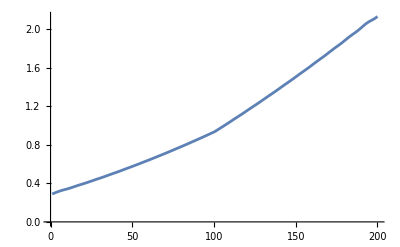

```mathematica
ListPlot[y1,Joined->True,PlotRange->All]
```

## elements except trend

```mathematica
xx=Sum[w[[i,i]]Outer[Times,Transpose[u][[i]],Transpose[v][[i]]],{i,2,3}];
```

```mathematica
y1=sn[xx];
```

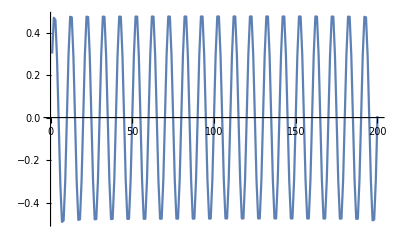

```mathematica
ListPlot[y1,Joined->True]
```

```mathematica
?
```